## Roy equations

The fixed-t and fixed-s dispersion relation for the amplitude is

T(s,t)=(32π)/s_th(s I_2+t C_st+u C_su)(a_00 ,0, a_20)+∫_s_th^∞ g2(s,t,sp)ImT(sp,0)ⅆsp+∫_s_th^∞ g3(s,t,sp)ImT(sp,t)ⅆsp

```mathematica
Off[NIntegrate::slwcon]
```

```mathematica
Off[NIntegrate::ncvb]
```

```mathematica
par=Join[S0par,Ppar,S2par,D0par,D2par,Fpar];
Δpar=Join[ΔS0par,ΔPpar,ΔS2par,ΔD0par,ΔD2par,ΔFpar];
```

### Kinematics

```mathematica
tt[s_,z_]=1/2(sth-s)(1-z);
```

```mathematica
Solve[tt[s,z]==t,z]//FullSimplify
```

{{z→1+(2 t)/(s-sth)}}

```mathematica
zp[s_,sp_,z_]=1+(2 tt[s,z])/(sp-sth);
```

```mathematica
zp[s,s,z]//FullSimplify
```

z

```mathematica
Solve[tt[s,z]==0,z]
```

{{z→1}}

```mathematica
LegendreP[J,1]
```

1

```mathematica
toRK={s-> (4 s)/sth,sp-> (4 sp)/sth,pi-> π,y-> 1/2 Log[(1+(sth-s)/(s+2sp-sth))/(1-(sth-s)/(s+2sp-sth))]};
```

### Crossing matrices

```mathematica
II=IdentityMatrix[3];
```

```mathematica
Cst={{1/3,1,5/3},{1/3,1/2,-5/6},{1/3,-1/2,1/6}};
```

```mathematica
Ctu={{1,0,0},{0,-1,0},{0,0,1}};
```

```mathematica
Csu={{1/3,-1,5/3},{-1/3,1/2,5/6},{1/3,1/2,1/6}};
```

```mathematica
Cst.Cst//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Ctu.Ctu//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Csu.Csu//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Cst.Ctu-Ctu.Csu//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
Cst.Csu-Ctu.Cst
```

{{0,0,0},{0,0,0},{0,0,0}}

### g2 and g3 functions

```mathematica
g2[s_,t_,sp_]=-t/(π sp(sp-sth))((sth-s-t) Cst+s Cst.Ctu).(II/(sp-t)+Csu/(sp-sth+t));
```

```mathematica
g3[s_,t_,sp_]=-(s (sth-s-t))/(π sp(sp-sth+t))(II/(sp-s)+Csu/(sp-sth+s+t));
```

### Partial-wave expansion

First the partial-wave expansion

```mathematica
KT[s_,sp_,z_,Jp_]=(2Jp+1)(g2[s,tt[s,z],sp]+g3[s,tt[s,z],sp]LegendreP[Jp,zp[s,sp,z]]);
```

Contributions to I=0

```mathematica
KT00[s_,sp_,z_,Jp_]=FullSimplify[{1,0,0}.KT[s,sp,z,Jp].{1,0,0}];
```

```mathematica
KT01[s_,sp_,z_,Jp_]=FullSimplify[{1,0,0}.KT[s,sp,z,Jp].{0,1,0}];
```

```mathematica
KT02[s_,sp_,z_,Jp_]=FullSimplify[{1,0,0}.KT[s,sp,z,Jp].{0,0,1}];
```

Contributions to I=1

```mathematica
KT10[s_,sp_,z_,Jp_]=FullSimplify[{0,1,0}.KT[s,sp,z,Jp].{1,0,0}];
```

```mathematica
KT11[s_,sp_,z_,Jp_]=FullSimplify[{0,1,0}.KT[s,sp,z,Jp].{0,1,0}];
```

```mathematica
KT12[s_,sp_,z_,Jp_]=FullSimplify[{0,1,0}.KT[s,sp,z,Jp].{0,0,1}];
```

Contributions to I=2

```mathematica
KT20[s_,sp_,z_,Jp_]=FullSimplify[{0,0,1}.KT[s,sp,z,Jp].{1,0,0}];
```

```mathematica
KT21[s_,sp_,z_,Jp_]=FullSimplify[{0,0,1}.KT[s,sp,z,Jp].{0,1,0}];
```

```mathematica
KT22[s_,sp_,z_,Jp_]=FullSimplify[{0,0,1}.KT[s,sp,z,Jp].{0,0,1}];
```

Second we consider the partial-wave projection. To be done in the next subsections

### Kernels for the S0 wave

#### Contributions from I = 0 partial waves

II’=00

```mathematica
KK00[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT00[s,sp,z,Jp],{z,0,1}]]]
```

00 to 00, S0 to S0

```mathematica
K0000[s_,sp_]=KK00[s,sp,0,0]
```

((-1+(3 s)/(-s+sp)+(2 s+sp)/(-sp+sth))/sp+(2 Log[(s+sp-sth)/sp])/(s-sth))/(3 π)

```mathematica
K0000S[s_,sp_]=1/π 1/(sp-s)-(2s+5sp-4sth)/(3π sp(sp-sth))+2/(3π(s-sth))Log[1+(s-sth)/sp];
```

```mathematica
K0000[s,sp]-K0000S[s,sp]//FullSimplify
```

0

```mathematica
K0000R[s_,sp_]=-4/sth(-((4*(-4*s+sp)+(2*s-sp)*(s+2*sp))/(sp*(-4+sp)*(-s+sp)))+(4*y)/(-4+s))/(3*pi)/.toRK//FullSimplify
```

((-1+(3 s)/(-s+sp)+(2 s+sp)/(-sp+sth))/sp-(2 Log[sp/(s+sp-sth)])/(s-sth))/(3 π)

```mathematica
FullSimplify[K0000[s,sp]-K0000R[s,sp],s>sp>sth>0]
```

0

02 to 00, D0 to S0

```mathematica
K0002[s_,sp_]=Collect[KK00[s,sp,0,2],Log[x_],FullSimplify]
```

-(5 (-3 s^2+2 (sp-sth) (2 sp-sth)+5 s (2 sp+sth)))/(6 π sp (sp-sth)^2)+(20 s (s+sp-sth) Log[2])/(π (s-sth) (sp-sth)^2)-(10 Log[sp])/(3 π s-3 π sth)+(10 (6 s^2+6 s (sp-sth)+(sp-sth)^2) Log[s+sp-sth])/(3 π (s-sth) (sp-sth)^2)-(20 s (s+sp-sth) Log[s+2 sp-sth])/(π (s-sth) (sp-sth)^2)

```mathematica
K0002S[s_,sp_]=-5/(3 π sp)+(5 (s^2-5 s sp))/(2 π sp (-sp+sth)^2)-(5 (5 s-2 sp))/(6 π sp (-sp+sth))+10/(3 π (s- sth)) Log[1+(s-sth)/sp]-(20 s (s+sp-sth))/(π (s-sth) (sp-sth)^2)Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
FullSimplify[K0002S[s,sp]-K0002[s,sp],{sp>s>sth>0}]
```

0

04 to 00, G0 to S0

```mathematica
K0004[s_,sp_]=Collect[KK00[s,sp,0,4],Log[x_],FullSimplify]
```

(21 s^4-12 (sp-sth)^3 (2 sp-sth)-7 s^3 (162 sp+7 sth)+s^2 (-864 sp^2+1266 sp sth+11 sth^2)+s (-228 sp^3+468 sp^2 sth-336 sp sth^2+5 sth^3))/(4 π sp (sp-sth)^4)-(6 Log[sp])/(π s-π sth)+(6 Log[s+sp-sth])/(π s-π sth)+(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^4)+(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[s+2 sp-sth])/(π (sp-sth)^4 (-s+sth))

```mathematica
K0004S[s_,sp_]=-3/(π sp)-(7 (-3 s^4+169 s^3 sp-59 s^2 sp^2+13 s sp^3))/(4 π sp (sp-sth)^4)+(7 (7 s^3-184 s^2 sp+27 s sp^2))/(4 π sp (sp-sth)^3)+(11 s^2-321 s sp)/(4 π sp (sp-sth)^2)-(5 s+12 sp)/(4 π sp (sp-sth))+6/(π (s- sth))Log[1+(s-sth)/sp]-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(π (s-sth)(sp-sth)^4)Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
FullSimplify[K0004S[s,sp]-K0004[s,sp],s>sp>sth>0]
```

0

#### Contributions from I = 1 partial waves

II’=01

```mathematica
KK01[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT01[s,sp,z,Jp],{z,0,1}]]]
```

11 to 00, P to S0

```mathematica
K0011[s_,sp_]=Collect[KK01[s,sp,0,1],Log[x_],FullSimplify]
```

-(3 (3 s^2+2 s (sp+2 ⅈ π sp-2 sth)+2 ⅈ π sp (sp-sth)+sth (-2 sp+sth)))/(π sp (s-sth) (sp-sth))+(6 (2 s+sp-sth) Log[s+sp-sth])/(π (s-sth) (sp-sth))+(6 (2 s+sp-sth) Log[sp (s+2 sp-sth)])/(π (s-sth) (-sp+sth))+(6 (2 s+sp-sth) Log[-s-2 sp+sth])/(π (s-sth) (sp-sth))

```mathematica
K0011S[s_,sp_]=-3/(π sp)+(3 (3 s^2-2 s sp-sp^2))/(π sp (sp-s) (sp-sth))+(6 (2 s+sp-sth))/(π (s-sth) (sp-sth)) Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[K0011S[s,sp]-K0011[s,sp],s>sp>sth>0]
```

0

```mathematica
K0011R[s_,sp_]=-4/sth(3*((4-s)*(4-3*s-2*sp)+4*sp*(-4+2*s+sp)*y))/(pi*(4-s)*(4-sp)*sp)/.toRK//FullSimplify
```

-(3 ((s-sth) (3 s+2 sp-sth)+2 sp (2 s+sp-sth) Log[sp/(s+sp-sth)]))/(π sp (s-sth) (sp-sth))

```mathematica
FullSimplify[K0011R[s,sp]-K0011S[s,sp],s>sp>sth>0]
```

0

31 to 00, F to S0

```mathematica
K0013[s_,sp_]=Collect[KK01[s,sp,0,3],Log[x_],FullSimplify]
```

1/(6 π sp (sp-sth)^3 (-s+sth))7 (10 s^4+15 s^3 (9 sp-sth)+6 s^2 (13 sp^2-41 sp sth+3 sth^2)+s (12 (1+2 ⅈ π) sp^3+12 (-9-4 ⅈ π) sp^2 sth+3 (45+8 ⅈ π) sp sth^2-19 sth^3)+6 (sp-sth)^2 (2 ⅈ π sp (sp-sth)+sth (-2 sp+sth)))+(140 s Log[2])/(π (s-sth) (sp-sth))+(28 s Log[sp])/(π (s-sth) (-sp+sth))+(14 (12 s+sp-sth) Log[s+sp-sth])/(π (s-sth) (sp-sth))-(140 s^2 (2 s+3 sp-3 sth) Log[2 (s+sp-sth)])/(π (s-sth) (-sp+sth)^3)+(28 s (10 s^2+15 s (sp-sth)+6 (sp-sth)^2) Log[s+2 sp-sth])/(π (sp-sth)^3 (-s+sth))-(14 Log[sp (s+2 sp-sth)])/(π s-π sth)+(14 (2 s+sp-sth) Log[-s-2 sp+sth])/(π (s-sth) (sp-sth))

```mathematica
K0013S[s_,sp_]=-7/(π sp)-(35 (s^3+13 s^2 sp-2 s sp^2))/(3 π sp (sp-sth)^3)-(35 (s^2+17 s sp))/(6 π sp (sp-sth)^2)+(7 (13 s^2-7 s sp-6 sp^2))/(6 π sp (sp-s) (sp-sth))+(14 (2 s+sp-sth))/(π (s-sth) (sp-sth)) Log[1+(s-sth)/sp]-(140 s (s+sp-sth) (2 s+sp-sth))/(π (s-sth) (sp-sth)^3)Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
FullSimplify[K0013S[s,sp]-K0013[s,sp],sp>sth>s>0]
```

0

#### Contributions from I = 2 partial waves

II’=02

```mathematica
KK02[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT02[s,sp,z,Jp],{z,0,1}]]]
```

20 to 00, S2 to S0

```mathematica
K0020[s_,sp_]=KK02[s,sp,0,0]
```

(5 ((s-2 sp+sth)/(sp^2-sp sth)+(2 Log[(s+sp-sth)/sp])/(s-sth)))/(3 π)

```mathematica
K0020S[s_,sp_]=-10/(3π sp)+(5(s-sth))/(3π sp(sp- sth))+10/(3π(s-sth))Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[K0020S[s,sp]-K0020[s,sp]]
```

0

```mathematica
K0020R[s_,sp_]=-4/sth(5*((4-s)*(4+s-2*sp)+4*sp*(-4+sp)*y))/(3*pi*(4-s)*(4-sp)*sp)/.toRK//FullSimplify
```

(5 ((s-2 sp+sth)/(sp^2-sp sth)-(2 Log[sp/(s+sp-sth)])/(s-sth)))/(3 π)

```mathematica
FullSimplify[K0020R[s,sp]-K0020[s,sp],sp>s>sth>0]
```

0

22 to 00, D2 to S0

```mathematica
K0022[s_,sp_]=Collect[KK02[s,sp,0,2],Log[x_],FullSimplify]
```

25/6 ((4 ⅈ)/(-s+sth)+(-3 s^2-10 s sp-4 sp^2+s sth+6 sp sth-2 sth^2)/(π sp (sp-sth)^2))-(50 Log[sp])/(3 π s-3 π sth)+(50 Log[s+sp-sth])/(3 π s-3 π sth)+(100 s (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^2)+(50 (6 s^2+6 s (sp-sth)+(sp-sth)^2) Log[s+2 sp-sth])/(3 π (sp-sth)^2 (-s+sth))+(50 Log[-s-2 sp+sth])/(3 π s-3 π sth)

```mathematica
K0022S[s_,sp_]=-25/(3 π sp)-(25 (s^2+3 s sp))/(2 π sp (sp-sth)^2)-(25 (s+2 sp))/(6 π sp (sp-sth))-(100 s (s+sp-sth))/(π (s-sth) (sp-sth)^2)(Log[1-(s-sth)/(2 (s+sp-sth))])+50/(3 π (s-sth))(Log[1+(s-sth)/sp]);
```

```mathematica
FullSimplify[K0022[s,sp]-K0022S[s,sp],sp>s>sth>0]
```

0

24 to 00, G2 to S0

```mathematica
K0024[s_,sp_]=Collect[KK02[s,sp,0,4],Log[x_],FullSimplify]
```

1/(16 π sp (sp-sth)^4 (-s+sth))5 (105 s^5+140 s^4 (30 sp-sth)+30 s^3 (120 sp^2-296 sp sth+sth^2)+12 s^2 (76 sp^3-468 sp^2 sth+498 sp sth^2-sth^3)+s (96 sp^4-1248 sp^3 sth+2448 sp^2 sth^2-1536 sp sth^3+65 sth^4)+48 (sp-sth)^3 (2 ⅈ π sp (sp-sth)+sth (-2 sp+sth)))-(30 Log[sp])/(π s-π sth)+(30 Log[s+sp-sth])/(π s-π sth)+(300 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^4)+(30 (70 s^4+140 s^3 (sp-sth)+90 s^2 (sp-sth)^2+20 s (sp-sth)^3+(sp-sth)^4) Log[s+2 sp-sth])/(π (sp-sth)^4 (-s+sth))+(30 Log[-s-2 sp+sth])/(π s-π sth)

```mathematica
K0024S[s_,sp_]=-15/(π sp)-(175 (3 s^4+119 s^3 sp-31 s^2 sp^2+5 s sp^3))/(16 π sp (sp-sth)^4)-(175 (s^3+134 s^2 sp-15 s sp^2))/(16 π sp (sp-sth)^3)-(25 (-s^2+249 s sp))/(16 π sp (sp-sth)^2)-(5 (17 s+48 sp))/(16 π sp (sp-sth))+30/(π (s- sth)) Log[1+(s-sth)/sp]-(300 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(π (s-sth) (sp-sth)^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
FullSimplify[K0024S[s,sp]-K0024[s,sp],s>sp>sth>0]
```

0

### Kernels for the P wave

#### Contributions from I = 0 partial waves

II’=10

```mathematica
KK10[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT10[s,sp,z,Jp],{z,0,1}]]]
```

00 to 11, S0 to P

```mathematica
K1100[s_,sp_]=Collect[KK10[s,sp,1,0],Log[x_],FullSimplify]
```

-(s^2+12 sp^2-2 (s+6 sp) sth+sth^2)/(9 π sp (s-sth) (sp-sth))-(2 (s+2 sp-sth) Log[sp])/(3 π (s-sth)^2)+(2 (s+2 sp-sth) Log[s+sp-sth])/(3 π (s-sth)^2)

```mathematica
K1100S[s_,sp_]=-1/(9 π sp)-4/(3 π (s-sth))-(s-sp)/(9 π sp (sp-sth))+(2 (s+2 sp-sth))/(3 π (s-sth)^2)Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[K1100S[s,sp]-K1100[s,sp],sp>0]
```

0

```mathematica
K1100R[s_,sp_]=-4/sth((4-s)*(16+s^2+12*sp^2-8*(s+6*sp))-12*(4-s-2*sp)*(4-sp)*sp*y)/(9*pi*(-4+s)^2*(4-sp)*sp)/.toRK//FullSimplify;
```

```mathematica
FullSimplify[K1100S[s,sp]-K1100R[s,sp],s>sp>sth>0]
```

0

02 to 11, D0 to P

```mathematica
K1102[s_,sp_]=Collect[KK10[s,sp,1,2],Log[x_],FullSimplify]
```

1/(18 π sp (s-sth)^2 (sp-sth)^2)5 (3 s^4-7 s^3 (8 sp+sth)+3 s^2 (-24 sp^2+38 sp sth+sth^2)+3 s ((-8-4 ⅈ π) sp^3+8 (5+ⅈ π) sp^2 sth-4 ⅈ (-7 ⅈ+π) sp sth^2+sth^3)+2 (sp-sth) (sth (12 sp^2-12 sp sth+sth^2)-6 ⅈ π sp (2 sp^2-3 sp sth+sth^2)))+(20 s sp (2 sp-3 sth) Log[2])/(π (s-sth)^2 (sp-sth)^2)+(10 s sth^2 Log[64])/(3 π (s-sth)^2 (sp-sth)^2)-(10 s Log[sp])/(3 π (s-sth)^2)+(10 (13 s sp+2 sp^2-7 s sth-3 sp sth+sth^2) Log[s+sp-sth])/(3 π (s-sth)^2 (sp-sth))+(20 s^2 (s+3 sp-2 sth) Log[2 (s+sp-sth)])/(π (s-sth)^2 (sp-sth)^2)-(10 s (6 s^2+6 s (3 sp-2 sth)+(13 sp-7 sth) (sp-sth)) Log[s+2 sp-sth])/(3 π (s-sth)^2 (sp-sth)^2)+(10 (-2 sp+sth) Log[sp (s+2 sp-sth)])/(3 π (s-sth)^2)+(10 (s+2 sp-sth) Log[-s-2 sp+sth])/(3 π (s-sth)^2)

```mathematica
K1102S[s_,sp_]=-5/(9 π sp)-(10 (2 s^2+2 s sp+2 sp^2))/(3 π (s-sp)^2 (s-sth))+(5 (-s^3+20 s^2 sp+5 s sp^2))/(6 π sp (sp-s) (sp-sth)^2)+(5 (s^3+69 s sp^2+2 sp^3))/(18 π sp (sp-s)^2 (sp-sth))+(10 (2 sp+s-sth))/(3 π (s-sth)^2) Log[1+(s-sth)/sp]-(20 s (s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth)^2)Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
FullSimplify[K1102S[s,sp]-K1102[s,sp],s>sp>sth>0]
```

0

04 to 11, G0 to P

```mathematica
K1104[s_,sp_]=Collect[KK10[s,sp,1,4],Log[x_],FullSimplify]
```

1/(16 π sp (s-sth)^2 (sp-sth)^4)(21 s^6-35 s^5 (136 sp+sth)+10 s^4 (-1168 sp^2+1412 sp sth+sth^2)-14 s^3 (584 sp^3-1872 sp^2 sth+1092 sp sth^2+sth^3)+s^2 (-1920 sp^4+13488 sp^3 sth-19344 sp^2 sth^2+7304 sp sth^3+17 sth^4)+s (-96 ⅈ (-2 ⅈ+π) sp^5+384 (7+ⅈ π) sp^4 sth+144 (-45-4 ⅈ π) sp^3 sth^2+128 (44+3 ⅈ π) sp^2 sth^3+16 (-101-6 ⅈ π) sp sth^4+17 sth^5)+16 (sp-sth)^3 (sth (12 sp^2-12 sp sth+sth^2)-6 ⅈ π sp (2 sp^2-3 sp sth+sth^2)))+(120 s (-2 sp+sth) Log[2])/(π (s-sth)^2 (-sp+sth))-(6 s Log[sp])/(π (s-sth)^2)+(6 (sp (41 s+2 sp)-3 (7 s+sp) sth+sth^2) Log[s+sp-sth])/(π (s-sth)^2 (sp-sth))+(60 s^2 (7 s^3+7 s^2 (4 sp-3 sth)+s (37 sp-23 sth) (sp-sth)+(20 sp-11 sth) (sp-sth)^2) Log[2 (s+sp-sth)])/(π (s-sth)^2 (sp-sth)^4)-(6 s (70 s^4+70 s^3 (4 sp-3 sth)+10 s^2 (37 sp-23 sth) (sp-sth)+10 s (20 sp-11 sth) (sp-sth)^2+(41 sp-21 sth) (sp-sth)^3) Log[s+2 sp-sth])/(π (s-sth)^2 (sp-sth)^4)+(6 (-2 sp+sth) Log[sp (s+2 sp-sth)])/(π (s-sth)^2)+(6 (s+2 sp-sth) Log[-s-2 sp+sth])/(π (s-sth)^2)

```mathematica
K1104S[s_,sp_]=-1/(π sp)-12/(π (s-sth))+(21 s^4+7 s^3 sth+3 s^2 sth^2-15 s sth^3)/(16 π sp sth^4)+(21 s^5-14 s^4 sth-4 s^3 sth^2-8194 s^2 sth^3-449 s sth^4)/(16 π (s-sth) (sp-sth)^2 sth^3)+(7 (3 s^5-682 s^4 sth-332 s^3 sth^2+58 s^2 sth^3-7 s sth^4))/(16 π (s-sth) (sp-sth)^4 sth)-(7 (3 s^5-2 s^4 sth+1668 s^3 sth^2+258 s^2 sth^3-7 s sth^4))/(16 π (s-sth) (sp-sth)^3 sth^2)+(-21 s^5+14 s^4 sth+4 s^3 sth^2+18 s^2 sth^3-1919 s sth^4-16 sth^5)/(16 π (s-sth) (sp-sth) sth^4)+(6 (s+2 sp-sth))/(π (s-sth)^2)Log[1+(s-sth)/sp]-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth)^4)Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
FullSimplify[K1104S[s,sp]-K1104[s,sp],s>sp>sth>0]
```

0

#### Contributions from I = 1 partial waves

II’=01

```mathematica
KK11[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT11[s,sp,z,Jp],{z,0,1}]]]
```

11 to 11, P to P

```mathematica
K1111[s_,sp_]=Collect[KK11[s,sp,1,1],Log[x_],FullSimplify]
```

1/(2 π sp (-s+sp) (s-sth)^2 (sp-sth))(3 s^4+s^3 ((23+12 ⅈ π) sp-9 sth)+3 s^2 ((-4+6 ⅈ π) sp^2+(-11-6 ⅈ π) sp sth+3 sth^2)+3 s ((-4-6 ⅈ π) sp^3+8 sp^2 sth+(3+2 ⅈ π) sp sth^2-sth^3)+sp (sth (12 sp^2-12 sp sth+sth^2)-6 ⅈ π sp (2 sp^2-3 sp sth+sth^2)))+(3 (2 s+sp-sth) (s+2 sp-sth) Log[s+sp-sth])/(π (s-sth)^2 (sp-sth))+(3 (2 s+sp-sth) (s+2 sp-sth) Log[sp (s+2 sp-sth)])/(π (s-sth)^2 (-sp+sth))+(3 (2 s+sp-sth) (s+2 sp-sth) Log[-s-2 sp+sth])/(π (s-sth)^2 (sp-sth))

```mathematica
K1111S[s_,sp_]=1/(π (sp-s))-3/(2 π sp)-(6(sp+s))/(π (sp-s) (s-sth))+(3 s^2+20 s sp+sp^2)/(2 π sp(sp-s)  (sp-sth))+(3 (2 s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth)) Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[K1111S[s,sp]-K1111[s,sp],s>sp>sth>0]
```

0

```mathematica
K1111R[s_,sp_]=-4/sth((4-s)*(3*s^3+16*(3*s-sp)+23*s^2*sp-12*s*sp^2-12*sp^3-8*(3*s^2+5*s*sp-6*sp^2))-12*sp*(2*s^3+16*(s-sp)+ 3*s^2*sp-3*s*sp^2-2*sp^3- 12*(s^2-sp^2))*y)/(2*pi*(-4+s)^2*(4-sp)*(s-sp)*sp)/.toRK//FullSimplify;
```

```mathematica
FullSimplify[K1111S[s,sp]-K1111R[s,sp],s>sp>sth>0]
```

0

31 to 11, F to P

```mathematica
K1113[s_,sp_]=Collect[KK11[s,sp,1,3],Log[x_],FullSimplify]
```

-(7 (s^4+s^3 (171 sp-4 sth)+2 (sp-sth)^2 (12 sp^2-12 sp sth+sth^2)+s^2 (332 sp^2-256 sp sth+7 sth^2)+s (168 sp^3-310 sp^2 sth+137 sp sth^2-6 sth^3)))/(12 π sp (s-sth) (sp-sth)^3)+(70 s (7 s sp+2 sp^2-4 s sth-3 sp sth+sth^2) Log[2])/(π (s-sth)^2 (sp-sth)^2)+(7 (2 s+sp-sth) (s+2 sp-sth) Log[sp])/(π (s-sth)^2 (-sp+sth))+(7 (6 s^2 (12 sp-7 sth)+s (25 sp-13 sth) (sp-sth)+(sp-sth)^2 (2 sp-sth)) Log[s+sp-sth])/(π (s-sth)^2 (sp-sth)^2)+(70 s^3 (2 s+7 sp-5 sth) Log[2 (s+sp-sth)])/(π (s-sth)^2 (sp-sth)^3)+(70 s (s+sp-sth) (2 s+sp-sth) (s+2 sp-sth) Log[s+2 sp-sth])/(π (s-sth)^2 (-sp+sth)^3)

```mathematica
K1113S[s_,sp_]=-7/(6 π sp)-(14 (s^3+4 s^2 sp+4 s sp^2+sp^3))/(π (sp-s)^3 (s-sth))+(7 (s^4+167 s^3 sp+83 s^2 sp^2-11 s sp^3))/(12 π sp(sp-s)(sp-sth)^3)-(7 (3 s^4+71 s^3 sp-271 s^2 sp^2-43 s sp^3))/(12 π sp (sp-s)^2(sp-sth)^2)+(7 (2 s^4+17 s^3 sp+21 s^2 sp^2+79 s sp^3+sp^4))/(6 π sp (sp-s)^3 (sp-sth))+(7 (2 s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth))Log[1+(s-sth)/sp]+(70 s (s+sp-sth) (2 s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (-sp+sth)^3)Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
FullSimplify[K1113S[s,sp]-K1113[s,sp],s>sp>sth>0]
```

0

#### Contributions from I = 2 partial waves

II’=02

```mathematica
KK12[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT12[s,sp,z,Jp],{z,0,1}]]]
```

20 to 11, S2 to P

```mathematica
K1120[s_,sp_]=Collect[KK12[s,sp,1,0],Log[x_],FullSimplify]
```

(5 (s^2+12 sp^2-2 (s+6 sp) sth+sth^2))/(18 π sp (s-sth) (sp-sth))+(5 (s+2 sp-sth) Log[sp])/(3 π (s-sth)^2)-(5 (s+2 sp-sth) Log[s+sp-sth])/(3 π (s-sth)^2)

```mathematica
K1120S[s_,sp_]=5/(18 π sp)+10/(3 π (s-sth))-(5 (sp-s))/(18 π sp (sp-sth))-(5 (s+2 sp-sth))/(3 π (s-sth)^2)Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[K1120S[s,sp]-K1120[s,sp],sp>sth>s>0]
```

0

```mathematica
K1120R[s_,sp_]=-4/sth(-5*((4-s)*(16+s^2+12*sp^2-8*(s+6*sp))-12*(4-s-2*sp)*(4-sp)*sp*y))/ (18*pi*(-4+s)^2*(4-sp)*sp)/.toRK//FullSimplify;
```

```mathematica
FullSimplify[K1120S[s,sp]-K1120R[s,sp],sp>sth>s>0]
```

0

22 to 11, D2 to P

```mathematica
K1122[s_,sp_]=Collect[KK12[s,sp,1,2],Log[x_],FullSimplify]
```

(25 (-3 s^3+4 s^2 (14 sp+sth)+s (72 sp^2-58 sp sth+sth^2)+2 (sp-sth) (12 sp^2-12 sp sth+sth^2)))/(36 π sp (s-sth) (sp-sth)^2)-(50 s (-2 sp+sth) Log[2])/(π (s-sth)^2 (-sp+sth))+(25 (s+2 sp-sth) Log[sp])/(3 π (s-sth)^2)+(25 (13 s sp+2 sp^2-7 s sth-3 sp sth+sth^2) Log[s+sp-sth])/(3 π (s-sth)^2 (-sp+sth))-(50 s^2 (s+3 sp-2 sth) Log[2 (s+sp-sth)])/(π (s-sth)^2 (sp-sth)^2)+(50 s (s+sp-sth) (s+2 sp-sth) Log[s+2 sp-sth])/(π (s-sth)^2 (sp-sth)^2)

```mathematica
K1122S[s_,sp_]=25/(18 π sp)+50/(3 π (s-sth))+(50 s sp)/(π (sp-s)^2 (s-sth))+(25 s(s^2-20 s sp-5 sp^2))/(12 π sp (sp-s) (sp-sth)^2)-(25 (s^3+69 s sp^2+2 sp^3))/(36 π sp (sp-s)^2 (sp-sth))-(25 (s+2 sp-sth))/(3 π (s-sth)^2)Log[1+(s-sth)/sp]+(50 s (s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth)^2)Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
FullSimplify[K1122S[s,sp]-K1122[s,sp],sp>s>sth>0]
```

0

24 to 11, G2 to P

```mathematica
K1124[s_,sp_]=Collect[KK12[s,sp,1,4],Log[x_],FullSimplify]
```

1/(32 π sp (s-sth)^2 (sp-sth)^4)5 (-21 s^6+35 s^5 (136 sp+sth)+10 s^4 (1168 sp^2-1412 sp sth-sth^2)+14 s^3 (584 sp^3-1872 sp^2 sth+1092 sp sth^2+sth^3)+s^2 (1920 sp^4-13488 sp^3 sth+19344 sp^2 sth^2-7304 sp sth^3-17 sth^4)+s (96 (2+ⅈ π) sp^5-384 ⅈ (-7 ⅈ+π) sp^4 sth+144 (45+4 ⅈ π) sp^3 sth^2+128 (-44-3 ⅈ π) sp^2 sth^3+16 (101+6 ⅈ π) sp sth^4-17 sth^5)+16 (sp-sth)^3 (-sth (12 sp^2-12 sp sth+sth^2)+6 ⅈ π sp (2 sp^2-3 sp sth+sth^2)))-(300 s (-2 sp+sth) Log[2])/(π (s-sth)^2 (-sp+sth))+(15 s Log[sp])/(π (s-sth)^2)+(15 (sp (41 s+2 sp)-3 (7 s+sp) sth+sth^2) Log[s+sp-sth])/(π (s-sth)^2 (-sp+sth))-(150 s^2 (7 s^3+7 s^2 (4 sp-3 sth)+s (37 sp-23 sth) (sp-sth)+(20 sp-11 sth) (sp-sth)^2) Log[2 (s+sp-sth)])/(π (s-sth)^2 (sp-sth)^4)+(15 s (70 s^4+70 s^3 (4 sp-3 sth)+10 s^2 (37 sp-23 sth) (sp-sth)+10 s (20 sp-11 sth) (sp-sth)^2+(41 sp-21 sth) (sp-sth)^3) Log[s+2 sp-sth])/(π (s-sth)^2 (sp-sth)^4)-(15 (-2 sp+sth) Log[sp (s+2 sp-sth)])/(π (s-sth)^2)-(15 (s+2 sp-sth) Log[-s-2 sp+sth])/(π (s-sth)^2)

```mathematica
K1124S[s_,sp_]=5/(2 π sp)+30/(π (s-sth))+(150 sp (2 s^3+3 s^2 sp+2 s sp^2))/(π (sp-s)^4 (s-sth))+(35 (3 s^5-682 s^4 sp-332 s^3 sp^2+58 s^2 sp^3-7 s sp^4))/(32 π sp (sp-s) (sp-sth)^4)+(35 (s^5+656 s^4 sp-1294 s^3 sp^2-344 s^2 sp^3+21 s sp^4))/(32 π sp (sp-s)^2 (sp-sth)^3)+(5 s(3 s^4-1382 s^3 sp+2208 s^2 sp^2-7002 s sp^3-547 sp^4))/(32 π sp (sp-s)^3 (sp-sth)^2)-(5 (15 s^5-44 s^4 sp+1946 s^3 sp^2+2916 s^2 sp^3+1871 s sp^4+16 sp^5))/(32 π sp (sp-s)^4 (sp-sth))-(15 (s+2 sp-sth))/(π (s-sth)^2)(Log[1+(s-sth)/sp])+(150 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth)^4) Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
FullSimplify[K1124S[s,sp]-K1124S[s,sp],s>sp>sth>0]
```

0

### Kernels for the S2 wave

#### Contributions from I = 0 partial waves

II’=20

```mathematica
KK20[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT20[s,sp,z,Jp],{z,0,1}]]]
```

00 to 20, S0 to S2

```mathematica
K2000[s_,sp_]=KK20[s,sp,0,0]
```

((s-2 sp+sth)/(sp^2-sp sth)+(2 Log[(s+sp-sth)/sp])/(s-sth))/(3 π)

```mathematica
K2000S[s_,sp_]=-1/(3π sp)-(sp-s)/(3π sp (sp-sth))+2/(3π(s-sth))Log[(s+sp-sth)/sp];
```

```mathematica
K2000[s,sp]-K2000S[s,sp]//FullSimplify
```

0

```mathematica
K2000R[s_,sp_]=-4/sth((4+s-2*sp)/(4*sp-sp^2)+(4*y)/(-4+s))/(3*pi)/.toRK//FullSimplify;
```

```mathematica
FullSimplify[K2000[s,sp]-K2000R[s,sp],s>sp>sth>0]
```

0

02 to 20, D0 to S2

```mathematica
K2002[s_,sp_]=Collect[KK20[s,sp,0,2],Log[x_],FullSimplify]
```

5/6 ((4 ⅈ)/(-s+sth)+(-3 s^2-10 s sp-4 sp^2+s sth+6 sp sth-2 sth^2)/(π sp (sp-sth)^2))-(10 Log[sp])/(3 π s-3 π sth)+(10 Log[s+sp-sth])/(3 π s-3 π sth)+(20 s (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^2)+(10 (6 s^2+6 s (sp-sth)+(sp-sth)^2) Log[s+2 sp-sth])/(3 π (sp-sth)^2 (-s+sth))+(10 Log[-s-2 sp+sth])/(3 π s-3 π sth)

```mathematica
K2002S[s_,sp_]=-5/(3 π sp)-(5 s(s+3 sp))/(2 π sp (sp-sth)^2)-(5 (s+2 sp))/(6 π sp (sp-sth))+10/(3 π (s-sth))Log[1+(s-sth)/sp]-(20 s (s+sp-sth))/(π (s-sth) (sp-sth)^2)Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
FullSimplify[K2002S[s,sp]-K2002[s,sp],{sp>sth>s>0}]
```

0

04 to 20, G0 to S2

```mathematica
K2004[s_,sp_]=Collect[KK20[s,sp,0,4],Log[x_],FullSimplify]
```

1/(16 π sp (sp-sth)^4 (-s+sth))(105 s^5+140 s^4 (30 sp-sth)+30 s^3 (120 sp^2-296 sp sth+sth^2)+12 s^2 (76 sp^3-468 sp^2 sth+498 sp sth^2-sth^3)+s (96 sp^4-1248 sp^3 sth+2448 sp^2 sth^2-1536 sp sth^3+65 sth^4)+48 (sp-sth)^3 (2 ⅈ π sp (sp-sth)+sth (-2 sp+sth)))-(6 Log[sp])/(π s-π sth)+(6 Log[s+sp-sth])/(π s-π sth)+(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^4)+(6 (70 s^4+140 s^3 (sp-sth)+90 s^2 (sp-sth)^2+20 s (sp-sth)^3+(sp-sth)^4) Log[s+2 sp-sth])/(π (sp-sth)^4 (-s+sth))+(6 Log[-s-2 sp+sth])/(π s-π sth)

```mathematica
K2004S[s_,sp_]=-3/(π sp)-(35s (3 s^3+119 s^2 sp-31 s sp^2+5 sp^3))/(16 π sp (sp-sth)^4)-(35 s(s^2+134 s sp-15 sp^2))/(16 π sp (sp-sth)^3)+(5 s(s-249 sp))/(16 π sp (sp-sth)^2)-(17 s+48 sp)/(16 π sp (sp-sth))+6/(π (s-sth))Log[1+(s-sth)/sp]-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(π (s-sth) (sp-sth)^4)Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
FullSimplify[K2004S[s,sp]-K2004[s,sp],s>sp>sth>0]
```

0

#### Contributions from I = 1 partial waves

II’=01

```mathematica
KK21[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT21[s,sp,z,Jp],{z,0,1}]]]
```

11 to 20, P to S2

```mathematica
K2011[s_,sp_]=Collect[KK21[s,sp,0,1],Log[x_],FullSimplify]
```

(9 s^2+6 s (sp+2 ⅈ π sp-2 sth)+6 ⅈ π sp (sp-sth)+3 sth (-2 sp+sth))/(2 π sp (s-sth) (sp-sth))+(3 (2 s+sp-sth) Log[s+sp-sth])/(π (s-sth) (-sp+sth))+(3 (2 s+sp-sth) Log[sp (s+2 sp-sth)])/(π (s-sth) (sp-sth))+(3 (2 s+sp-sth) Log[-s-2 sp+sth])/(π (s-sth) (-sp+sth))

```mathematica
K2011S[s_,sp_]=3/(2 π sp)+(3 (3 s+sp))/(2 π sp (sp-sth))-(3 (2 s+sp-sth))/(π (s-sth) (sp-sth))Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[K2011S[s,sp]-K2011[s,sp],s>sp>sth>0]
```

0

```mathematica
K2011R[s_,sp_]=-4/sth(-3*((4-s)*(4-3*s-2*sp)+4*sp*(-4+2*s+sp)*y))/(2*pi*(4-s)*(4-sp)*sp)/.toRK//FullSimplify;
```

```mathematica
FullSimplify[K2011R[s,sp]-K2011S[s,sp],s>sp>sth>0]
```

0

31 to 20, F to S2

```mathematica
K2013[s_,sp_]=Collect[KK21[s,sp,0,3],Log[x_],FullSimplify]
```

1/(12 π sp (sp-sth)^3 (-s+sth))7 (-10 s^4+15 s^3 (-9 sp+sth)+6 (sp-sth)^2 (-2 ⅈ π sp (sp-sth)+(2 sp-sth) sth)-6 s^2 (13 sp^2-41 sp sth+3 sth^2)+s ((-12-24 ⅈ π) sp^3+12 (9+4 ⅈ π) sp^2 sth+3 (-45-8 ⅈ π) sp sth^2+19 sth^3))+(70 s sth (-2 sp+sth) Log[2])/(π (sp-sth)^3 (-s+sth))+(7 s sp^2 Log[1024])/(π (s-sth) (-sp+sth)^3)+(14 s Log[sp])/(π (s-sth) (sp-sth))+(7 (12 s+sp-sth) Log[s+sp-sth])/(π (sp-sth) (-s+sth))+(70 s^2 (2 s+3 sp-3 sth) Log[2 (s+sp-sth)])/(π (s-sth) (-sp+sth)^3)-(14 s (10 s^2+15 s (sp-sth)+6 (sp-sth)^2) Log[s+2 sp-sth])/(π (sp-sth)^3 (-s+sth))+(7 Log[sp (s+2 sp-sth)])/(π s-π sth)+(7 (2 s+sp-sth) Log[-s-2 sp+sth])/(π (sp-sth) (-s+sth))

```mathematica
K2013S[s_,sp_]=7/(2 π sp)+(35s (s^2+13 s sp-2 sp^2))/(6 π sp (sp-sth)^3)+(35 s(s+17 sp))/(12 π sp (sp-sth)^2)+(7 (13 s+6 sp))/(12 π sp (sp-sth))-(7 (2 s+sp-sth))/(π (s-sth) (sp-sth)) Log[1+(s-sth)/sp]-(70 s (s+sp-sth) (2 s+sp-sth))/(π (s-sth) (-sp+sth)^3)Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
FullSimplify[K2013S[s,sp]-K2013[s,sp],sp>sth>s>0]
```

0

#### Contributions from I = 2 partial waves

II’=02

```mathematica
KK22[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT22[s,sp,z,Jp],{z,0,1}]]]
```

20 to 20, S2 to S2

```mathematica
K2020[s_,sp_]=KK22[s,sp,0,0]
```

((-1+(6 s)/(-s+sp)+(5 s+sp)/(-sp+sth))/sp+(2 Log[(s+sp-sth)/sp])/(s-sth))/(6 π)

```mathematica
K2020S[s_,sp_]=1/(π (sp-s))-7/(6 π sp)-(5 s+sp)/(6 π sp (sp-sth))+1/(3 π(s-sth))Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[K2020S[s,sp]-K2020[s,sp]]
```

0

```mathematica
K2020R[s_,sp_]=-4/sth(-((5*s^2+3*s*sp-2*sp^2+4*(-7*s+sp))/ (sp*(-4+sp)*(-s+sp)))+(4*y)/(-4+s))/(6*pi)/.toRK//FullSimplify;
```

```mathematica
FullSimplify[K2020R[s,sp]-K2020[s,sp],sp>s>sth>0]
```

0

22 to 20, D2 to S2

```mathematica
K2022[s_,sp_]=Collect[KK22[s,sp,0,2],Log[x_],FullSimplify]
```

-(5 (-9 s^2+10 s sp+4 sp^2+11 s sth-6 sp sth+2 sth^2))/(12 π sp (sp-sth)^2)+(10 s (s+sp-sth) Log[2])/(π (s-sth) (sp-sth)^2)-(5 Log[sp])/(3 π s-3 π sth)+(5 (6 s^2+6 s (sp-sth)+(sp-sth)^2) Log[s+sp-sth])/(3 π (s-sth) (sp-sth)^2)-(10 s (s+sp-sth) Log[s+2 sp-sth])/(π (s-sth) (sp-sth)^2)

```mathematica
K2022S[s_,sp_]=-5/(6 π sp)+(5 (3 s^2-7 s sp))/(4 π sp (sp-sth)^2)+(5 (11 s-2 sp))/(12 π sp (sp-sth))+5/(3 π (s- sth))Log[1+(s-sth)/sp]-(10 s (s+sp-sth))/(π (s-sth) (sp-sth)^2) Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
FullSimplify[K2022[s,sp]-K2022S[s,sp],sp>s>sth>0]
```

0

24 to 20, G2 to S2

```mathematica
K2024[s_,sp_]=Collect[KK22[s,sp,0,4],Log[x_],FullSimplify]
```

(273 s^4-48 (sp-sth)^3 (2 sp-sth)-7 s^3 (696 sp+61 sth)+s^2 (-3312 sp^2+5448 sp sth+83 sth^2)+s (-912 sp^3+1728 sp^2 sth-1392 sp sth^2+23 sth^3))/(32 π sp (sp-sth)^4)-(3 Log[sp])/(π s-π sth)+(3 Log[s+sp-sth])/(π s-π sth)+(30 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^4)+(30 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[s+2 sp-sth])/(π (sp-sth)^4 (-s+sth))

```mathematica
K2024S[s_,sp_]=-3/(2 π sp)+(7s (39 s^3-757 s^2 sp+317 s sp^2-79 sp^3))/(32 π sp (sp-sth)^4)+(7 s(61 s^2-802 s sp+141 sp^2))/(32 π sp (sp-sth)^3)+(s(83s- 1323 sp))/(32 π sp (sp-sth)^2)-(23 s+48 sp)/(32 π sp (sp-sth))+3/(π s-π sth)Log[1+(s-sth)/sp]-(30 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(π (sp-sth)^4 (s-sth)) Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
FullSimplify[K2024S[s,sp]-K2024[s,sp],s>sp>sth>0]
```

0

### Hard - cored Kernels

Contribution to S0

```mathematica
K0000S[s_,sp_]=1/π 1/(sp-s)-(2s+5sp-4sth)/(3π sp(sp-sth))+2/(3π(s-sth))Log[(s+sp-sth)/sp];
```

```mathematica
K0002S[s_,sp_]=-5/(3 π sp)+(5 (s^2-5 s sp))/(2 π sp (-sp+sth)^2)-(5 (5 s-2 sp))/(6 π sp (-sp+sth))+10/(3 π (s- sth)) Log[1+(s-sth)/sp]-(20 s (s+sp-sth))/(π (s-sth) (sp-sth)^2)Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
K0004S[s_,sp_]=-3/(π sp)-(7 (-3 s^4+169 s^3 sp-59 s^2 sp^2+13 s sp^3))/(4 π sp (sp-sth)^4)+(7 (7 s^3-184 s^2 sp+27 s sp^2))/(4 π sp (sp-sth)^3)+(11 s^2-321 s sp)/(4 π sp (sp-sth)^2)-(5 s+12 sp)/(4 π sp (sp-sth))+6/(π (s- sth))Log[1+(s-sth)/sp]-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(π (s-sth)(sp-sth)^4)Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
K0011S[s_,sp_]=-3/(π sp)+(3 (3 s^2-2 s sp-sp^2))/(π sp (sp-s) (sp-sth))+(6 (2 s+sp-sth))/(π (s-sth) (sp-sth)) Log[1+(s-sth)/sp];
```

```mathematica
K0013S[s_,sp_]=-7/(π sp)-(35 (s^3+13 s^2 sp-2 s sp^2))/(3 π sp (sp-sth)^3)-(35 (s^2+17 s sp))/(6 π sp (sp-sth)^2)+(7 (13 s^2-7 s sp-6 sp^2))/(6 π sp (sp-s) (sp-sth))+(14 (2 s+sp-sth))/(π (s-sth) (sp-sth)) Log[1+(s-sth)/sp]-(140 s (s+sp-sth) (2 s+sp-sth))/(π (s-sth) (sp-sth)^3)Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
K0020S[s_,sp_]=-10/(3π sp)+(5(s-sth))/(3π sp(sp- sth))+10/(3π(s-sth))Log[1+(s-sth)/sp];
```

```mathematica
K0022S[s_,sp_]=-25/(3 π sp)-(25 (s^2+3 s sp))/(2 π sp (sp-sth)^2)-(25 (s+2 sp))/(6 π sp (sp-sth))-(100 s (s+sp-sth))/(π (s-sth) (sp-sth)^2)(Log[1-(s-sth)/(2 (s+sp-sth))])+50/(3 π (s-sth))(Log[1+(s-sth)/sp]);
```

```mathematica
K0024S[s_,sp_]=-15/(π sp)-(175 (3 s^4+119 s^3 sp-31 s^2 sp^2+5 s sp^3))/(16 π sp (sp-sth)^4)-(175 (s^3+134 s^2 sp-15 s sp^2))/(16 π sp (sp-sth)^3)-(25 (-s^2+249 s sp))/(16 π sp (sp-sth)^2)-(5 (17 s+48 sp))/(16 π sp (sp-sth))+30/(π (s- sth)) Log[1+(s-sth)/sp]-(300 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(π (s-sth) (sp-sth)^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

Contribution to P

```mathematica
K1100S[s_,sp_]=-1/(9 π sp)-4/(3 π (s-sth))-(s-sp)/(9 π sp (sp-sth))+(2 (s+2 sp-sth))/(3 π (s-sth)^2)Log[1+(s-sth)/sp];
```

```mathematica
K1102S[s_,sp_]=-5/(9 π sp)-(10 (2 s^2+2 s sp+2 sp^2))/(3 π (s-sp)^2 (s-sth))+(5 (-s^3+20 s^2 sp+5 s sp^2))/(6 π sp (sp-s) (sp-sth)^2)+(5 (s^3+69 s sp^2+2 sp^3))/(18 π sp (sp-s)^2 (sp-sth))+(10 (2 sp+s-sth))/(3 π (s-sth)^2) Log[1+(s-sth)/sp]-(20 s (s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth)^2)Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
K1104S[s_,sp_]=-1/(π sp)-12/(π (s-sth))+(21 s^4+7 s^3 sth+3 s^2 sth^2-15 s sth^3)/(16 π sp sth^4)+(21 s^5-14 s^4 sth-4 s^3 sth^2-8194 s^2 sth^3-449 s sth^4)/(16 π (s-sth) (sp-sth)^2 sth^3)+(7 (3 s^5-682 s^4 sth-332 s^3 sth^2+58 s^2 sth^3-7 s sth^4))/(16 π (s-sth) (sp-sth)^4 sth)-(7 (3 s^5-2 s^4 sth+1668 s^3 sth^2+258 s^2 sth^3-7 s sth^4))/(16 π (s-sth) (sp-sth)^3 sth^2)+(-21 s^5+14 s^4 sth+4 s^3 sth^2+18 s^2 sth^3-1919 s sth^4-16 sth^5)/(16 π (s-sth) (sp-sth) sth^4)+(6 (s+2 sp-sth))/(π (s-sth)^2)Log[1+(s-sth)/sp]-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth)^4)Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
K1111S[s_,sp_]=1/(π (sp-s))-3/(2 π sp)-(6(sp+s))/(π (sp-s) (s-sth))+(3 s^2+20 s sp+sp^2)/(2 π sp(sp-s)  (sp-sth))+(3 (2 s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth)) Log[1+(s-sth)/sp];
```

```mathematica
K1113S[s_,sp_]=-7/(6 π sp)-(14 (s^3+4 s^2 sp+4 s sp^2+sp^3))/(π (sp-s)^3 (s-sth))+(7 (s^4+167 s^3 sp+83 s^2 sp^2-11 s sp^3))/(12 π sp(sp-s)(sp-sth)^3)-(7 (3 s^4+71 s^3 sp-271 s^2 sp^2-43 s sp^3))/(12 π sp (sp-s)^2(sp-sth)^2)+(7 (2 s^4+17 s^3 sp+21 s^2 sp^2+79 s sp^3+sp^4))/(6 π sp (sp-s)^3 (sp-sth))+(7 (2 s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth))Log[1+(s-sth)/sp]+(70 s (s+sp-sth) (2 s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (-sp+sth)^3)Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
K1120S[s_,sp_]=5/(18 π sp)+10/(3 π (s-sth))-(5 (sp-s))/(18 π sp (sp-sth))-(5 (s+2 sp-sth))/(3 π (s-sth)^2)Log[1+(s-sth)/sp];
```

```mathematica
K1122S[s_,sp_]=25/(18 π sp)+50/(3 π (s-sth))+(50 s sp)/(π (sp-s)^2 (s-sth))+(25 s(s^2-20 s sp-5 sp^2))/(12 π sp (sp-s) (sp-sth)^2)-(25 (s^3+69 s sp^2+2 sp^3))/(36 π sp (sp-s)^2 (sp-sth))-(25 (s+2 sp-sth))/(3 π (s-sth)^2)Log[1+(s-sth)/sp]+(50 s (s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth)^2)Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
K1124S[s_,sp_]=5/(2 π sp)+30/(π (s-sth))+(150 sp (2 s^3+3 s^2 sp+2 s sp^2))/(π (sp-s)^4 (s-sth))+(35 (3 s^5-682 s^4 sp-332 s^3 sp^2+58 s^2 sp^3-7 s sp^4))/(32 π sp (sp-s) (sp-sth)^4)+(35 (s^5+656 s^4 sp-1294 s^3 sp^2-344 s^2 sp^3+21 s sp^4))/(32 π sp (sp-s)^2 (sp-sth)^3)+(5 s(3 s^4-1382 s^3 sp+2208 s^2 sp^2-7002 s sp^3-547 sp^4))/(32 π sp (sp-s)^3 (sp-sth)^2)-(5 (15 s^5-44 s^4 sp+1946 s^3 sp^2+2916 s^2 sp^3+1871 s sp^4+16 sp^5))/(32 π sp (sp-s)^4 (sp-sth))-(15 (s+2 sp-sth))/(π (s-sth)^2)(Log[1+(s-sth)/sp])+(150 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s+2 sp-sth))/(π (s-sth)^2 (sp-sth)^4) Log[1-(s-sth)/(2(s+sp-sth))];
```

Contribution to S2

```mathematica
K2000S[s_,sp_]=-1/(3π sp)-(sp-s)/(3π sp (sp-sth))+2/(3π(s-sth))Log[(s+sp-sth)/sp];
```

```mathematica
K2002S[s_,sp_]=-5/(3 π sp)-(5 s(s+3 sp))/(2 π sp (sp-sth)^2)-(5 (s+2 sp))/(6 π sp (sp-sth))+10/(3 π (s-sth))Log[1+(s-sth)/sp]-(20 s (s+sp-sth))/(π (s-sth) (sp-sth)^2)Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
K2004S[s_,sp_]=-3/(π sp)-(35s (3 s^3+119 s^2 sp-31 s sp^2+5 sp^3))/(16 π sp (sp-sth)^4)-(35 s(s^2+134 s sp-15 sp^2))/(16 π sp (sp-sth)^3)+(5 s(s-249 sp))/(16 π sp (sp-sth)^2)-(17 s+48 sp)/(16 π sp (sp-sth))+6/(π (s-sth))Log[1+(s-sth)/sp]-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(π (s-sth) (sp-sth)^4)Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
K2011S[s_,sp_]=3/(2 π sp)+(3 (3 s+sp))/(2 π sp (sp-sth))-(3 (2 s+sp-sth))/(π (s-sth) (sp-sth))Log[1+(s-sth)/sp];
```

```mathematica
K2013S[s_,sp_]=7/(2 π sp)+(35s (s^2+13 s sp-2 sp^2))/(6 π sp (sp-sth)^3)+(35 s(s+17 sp))/(12 π sp (sp-sth)^2)+(7 (13 s+6 sp))/(12 π sp (sp-sth))-(7 (2 s+sp-sth))/(π (s-sth) (sp-sth)) Log[1+(s-sth)/sp]-(70 s (s+sp-sth) (2 s+sp-sth))/(π (s-sth) (-sp+sth)^3)Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
K2020S[s_,sp_]=1/(π (sp-s))-7/(6 π sp)-(5 s+sp)/(6 π sp (sp-sth))+1/(3 π(s-sth))Log[1+(s-sth)/sp];
```

```mathematica
K2022S[s_,sp_]=-5/(6 π sp)+(5 (3 s^2-7 s sp))/(4 π sp (sp-sth)^2)+(5 (11 s-2 sp))/(12 π sp (sp-sth))+5/(3 π (s- sth))Log[1+(s-sth)/sp]-(10 s (s+sp-sth))/(π (s-sth) (sp-sth)^2) Log[1-(s-sth)/(2(s+sp-sth))];
```

```mathematica
K2024S[s_,sp_]=-3/(2 π sp)+(7s (39 s^3-757 s^2 sp+317 s sp^2-79 sp^3))/(32 π sp (sp-sth)^4)+(7 s(61 s^2-802 s sp+141 sp^2))/(32 π sp (sp-sth)^3)+(s(83s- 1323 sp))/(32 π sp (sp-sth)^2)-(23 s+48 sp)/(32 π sp (sp-sth))+3/(π s-π sth)Log[1+(s-sth)/sp]-(30 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(π (sp-sth)^4 (s-sth)) Log[1-(s-sth)/(2 (s+sp-sth))];
```

### Subtraction term contribution

```mathematica
ST[s_,t_]=(32π)/sth(s II+t Cst+(sth-s-t)Csu).{a00,0,a20};
```

#### Calculation of the S0 wave subtraction term

```mathematica
ST00[s_]=Collect[1/(32π)Integrate[ST[s,tt[s,z]][[1]]//FullSimplify,{z,0,1}],{a00,a20},FullSimplify]
```

(5 a20 (-s+sth))/(3 sth)+(a00 (2 s+sth))/(3 sth)

```mathematica
ST00[sth]
```

a00

```mathematica
ST00R[s_]=a00+(2*a00-5*a20)*s4/12/.s4-> 4((s-sth)/sth);
```

```mathematica
ST00R[s]-ST00[s]//FullSimplify
```

0

#### Calculation of the P wave subtraction term

```mathematica
ST11[s_]=FullSimplify[1/(32π)Integrate[z ST[s,tt[s,z]][[2]]//FullSimplify,{z,0,1}]]
```

((2 a00-5 a20) (s-sth))/(18 sth)

```mathematica
ST11[sth]
```

0

```mathematica
ST11R[s_]=(2*a00-5*a20)*s4/72/.s4-> 4((s-sth)/sth);
```

```mathematica
ST11R[s]-ST11[s]//FullSimplify
```

0

#### Calculation of the S2 wave subtraction term

```mathematica
ST20[s_]=Collect[1/(32π)Integrate[ST[s,tt[s,z]][[3]]//FullSimplify,{z,0,1}],{a00,a20},FullSimplify]
```

(a00 (-s+sth))/(3 sth)+(a20 (5 s+sth))/(6 sth)

```mathematica
ST20[sth]
```

a20

```mathematica
ST20R[s_]=a20-(2*a00-5*a20)*s4/24/.s4-> 4((s-sth)/sth);
```

```mathematica
ST20R[s]-ST20[s]//FullSimplify
```

0

#### Numerical values

```mathematica
SL={a00-> as00,a20-> as20};
```

```mathematica
as00/.par/.physval
```

0.220692

```mathematica
as20/.par/.physval
```

-0.0432111

```mathematica
t00ST[s_,param_]:=ST00[s]/.SL/.param/.physval;
```

```mathematica
t11ST[s_,param_]:=ST11[s]/.SL/.param/.physval;
```

```mathematica
t20ST[s_,param_]:=ST20[s]/.SL/.param/.physval;
```

```mathematica
ST00dat=Table[{W,ST00[W^2]/.physval/.a00->as0 M/.a20-> as2 M},{W,2M+10^-3,√(68 M^2),0.01}];
```

```mathematica
ST11dat=Table[{W,ST11[W^2]/.physval/.a00->as0 M/.a20-> as2 M},{W,2M+10^-3,√(68 M^2),0.01}];
```

```mathematica
ST20dat=Table[{W,ST20[W^2]/.physval/.a00->as0 M/.a20-> as2 M},{W,2M+10^-3,√(68 M^2),0.01}];
```

```mathematica
ST00R=Table[{S0Roydes[[i,1]]/1000,S0Roydes[[i,2]]},{i,1,Length[S0Roydes]}];
```

```mathematica
ST11R=Table[{PRoydes[[i,1]]/1000,PRoydes[[i,2]]},{i,1,Length[PRoydes]}];
```

```mathematica
ST20R=Table[{S2Roydes[[i,1]]/1000,S2Roydes[[i,2]]},{i,1,Length[S2Roydes]}];
```

```mathematica
ST00diff=Table[{S0Roydes[[i,1]]/1000,100(S0Roydes[[i,2]]-ST00[(S0Roydes[[i,1]]/1000)^2]/.physval/.a00->as0 M/.a20-> as2 M)/S0Roydes[[i,2]]},{i,1,Length[S0Roydes]}];
```

```mathematica
ST11diff=Table[{PRoydes[[i,1]]/1000,100(PRoydes[[i,2]]-ST11[(PRoydes[[i,1]]/1000)^2]/.physval/.a00->as0 M/.a20-> as2 M)/PRoydes[[i,2]]},{i,1,Length[S0Roydes]}];
```

```mathematica
ST20diff=Table[{S2Roydes[[i,1]]/1000,100(S2Roydes[[i,2]]-ST20[(S2Roydes[[i,1]]/1000)^2]/.physval/.a00->as0 M/.a20-> as2 M)/S2Roydes[[i,2]]},{i,1,Length[S0Roydes]}];
```

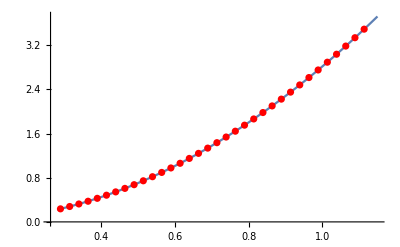

```mathematica
Show[{ListPlot[ST00dat,Joined->True],ListPlot[ST00R,PlotStyle->Red]}]
```

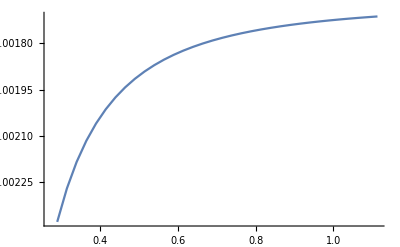

```mathematica
ListPlot[ST00diff,Joined->True]
```

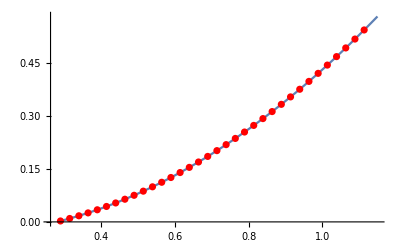

```mathematica
Show[{ListPlot[ST11dat,Joined->True],ListPlot[ST11R,PlotStyle->Red]}]
```

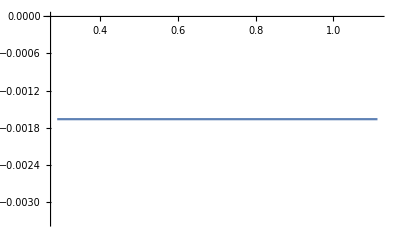

```mathematica
ListPlot[ST11diff,Joined->True]
```

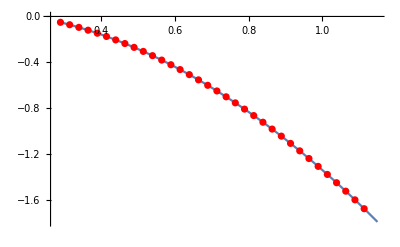

```mathematica
Show[{ListPlot[ST20dat,Joined->True],ListPlot[ST20R,PlotStyle->Red]}]
```

```mathematica
ListPlot[ST00diff,Joined->True]
```

-Graphics-

### Kernel-term contribution

#### Formulas

```mathematica
t00KT[s_,par_]:=NIntegrate[(K0000S[s,sp]imt00[sp]+K0011S[s,sp]imt11[sp]+K0020S[s,sp]imt20[sp])/.par/.physval,{sp,4 M^2,s,1.42^2},Method-> PrincipalValue]
```

```mathematica
t11KT[s_,par_]:=NIntegrate[(K1100S[s,sp]imt00[sp]+K1111S[s,sp]imt11[sp]+K1120S[s,sp]imt20[sp])/.par/.physval,{sp,4 M^2,s,1.42^2},Method-> PrincipalValue]
```

```mathematica
t20KT[s_,par_]:=NIntegrate[(K2000S[s,sp]imt00[sp]+K2011S[s,sp]imt11[sp]+K2020S[s,sp]imt20[sp])/.par/.physval,{sp,4 M^2,s,1.42^2},Method-> PrincipalValue]
```

#### Numerical values

```mathematica
t00KTdat=Monitor[Table[{W,Re[t00KT[W^2,par]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
t11KTdat=Monitor[Table[{W,Re[t11KT[W^2,par]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
t20KTdat=Monitor[Table[{W,Re[t20KT[W^2,par]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
t00KTR=Table[{S0Roydes[[i,1]]/1000,S0Roydes[[i,3]]},{i,1,Length[S0Roydes]}];
```

```mathematica
t11KTR=Table[{PRoydes[[i,1]]/1000,PRoydes[[i,3]]},{i,1,Length[PRoydes]}];
```

```mathematica
t20KTR=Table[{S2Roydes[[i,1]]/1000,S2Roydes[[i,3]]},{i,1,Length[S2Roydes]}];
```

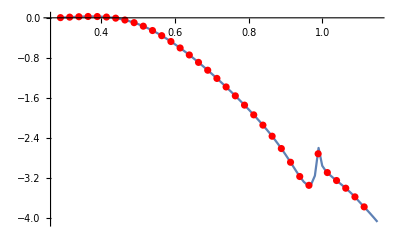

```mathematica
Show[{ListPlot[t00KTdat,Joined->True],ListPlot[t00KTR,PlotStyle->Red]}]
```

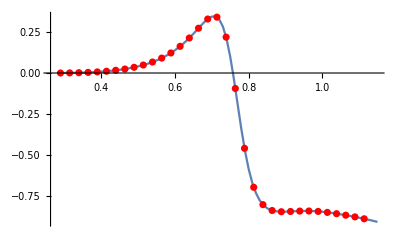

```mathematica
Show[{ListPlot[t11KTdat,Joined->True],ListPlot[t11KTR,PlotStyle->Red]}]
```

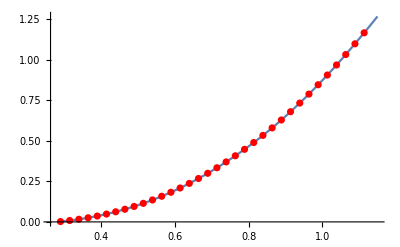

```mathematica
Show[{ListPlot[t20KTdat,Joined->True],ListPlot[t20KTR,PlotStyle->Red]}]
```

### Driving-term contribution

#### Formulas

```mathematica
t00DT[s_,par_]:=NIntegrate[(K0002S[s,sp]imt02[sp]+K0013S[s,sp]imt13[sp]+K0022S[s,sp]imt22[sp])/.par/.physval,{sp,4 M^2,s,1.42^2},Method-> PrincipalValue]
```

```mathematica
t11D0DT[s_,par_]:=NIntegrate[K1102S[s,sp]imt02[sp]/.par/.D2par/.physval,{sp,4 M^2+10^-6,1.42^2}]
```

```mathematica
t11FDT[s_,par_]:=NIntegrate[K1113S[s,sp]imt13[sp]/.par/.physval,{sp,4 M^2+10^-6,1.42^2}]
```

```mathematica
t11D2DT[s_,par_]:=NIntegrate[K1122S[s,sp]imt22[sp]/.par/.physval,{sp,4 M^2+10^-6,1.42^2}]
```

```mathematica
t11DT[s_,par_]:=t11D0DT[s,par]+t11FDT[s,par]+t11D2DT[s,par]
```

```mathematica
t20DT[s_,par_]:=NIntegrate[(K2002S[s,sp]imt02[sp]+K2013S[s,sp]imt13[sp]+K2022S[s,sp]imt22[sp])/.par/.physval,{sp,4 M^2,s,1.42^2},Method-> PrincipalValue]
```

#### Numerical values

```mathematica
t00DTdat=Monitor[Table[{W,Re[t00DT[W^2,par]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
t11DTdat=Monitor[Table[{W,t11DT[W^2,par]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
t20DTdat=Monitor[Table[{W,t20DT[W^2,par]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
t00DTR=Table[{S0Roydes[[i,1]]/1000,S0Roydes[[i,4]]},{i,1,Length[S0Roydes]}];
```

```mathematica
t11DTR=Table[{PRoydes[[i,1]]/1000,PRoydes[[i,4]]},{i,1,Length[PRoydes]}];
```

```mathematica
t20DTR=Table[{S2Roydes[[i,1]]/1000,S2Roydes[[i,4]]},{i,1,Length[S2Roydes]}];
```

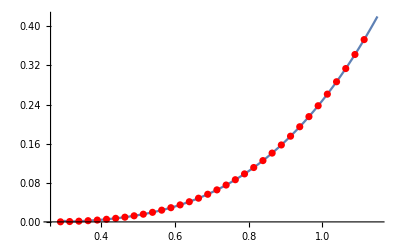

```mathematica
Show[{ListPlot[t00DTdat,Joined->True],ListPlot[t00DTR,PlotStyle->Red]}]
```

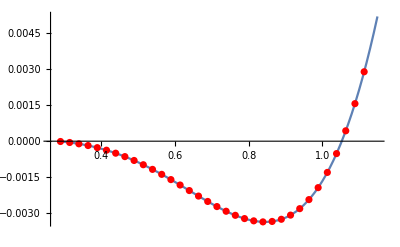

```mathematica
Show[{ListPlot[t11DTdat,Joined->True],ListPlot[t11DTR,PlotStyle->Red]}]
```

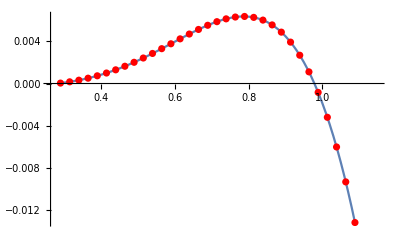

```mathematica
Show[{ListPlot[t20DTdat,Joined->True],ListPlot[t20DTR,PlotStyle->Red]}]
```

### Regge contribution

#### Formulas

The Regge contribution to the amplitude is

T_R(s,t)=∫_s_A^∞ g2(s,t,sp)ImT(sp,0)ⅆsp+∫_s_A^∞ g3(s,t,sp)ImT(sp,t)ⅆsp

but now we have to project in partial wave

(t^R)_J(s)=1/(64π)∫_-1^1 (∫_s_A^∞ g2(s,t,sp)ImT(sp,0)ⅆsp+∫_s_A^∞ g3(s,t,sp)ImT(sp,t)ⅆsp)P_J(z)dz

Is there an analytic calculation?

First we compute the different imaginary part contributions

```mathematica
ImF0R[s_,t_]=4 π^2 Cst[[1]].{ImF0t[s,t],ImF1t[s,t],ImF2t[s,t]}//FullSimplify;
```

```mathematica
ImF1R[s_,t_]=4 π^2 Cst[[2]].{ImF0t[s,t],ImF1t[s,t],ImF2t[s,t]}//FullSimplify;
```

```mathematica
ImF2R[s_,t_]=4 π^2 Cst[[3]].{ImF0t[s,t],ImF1t[s,t],ImF2t[s,t]}//FullSimplify;
```

Second we construct the isospin amplitudes

First contribution

```mathematica
T0RI[s_,t_,sp_]={1,0,0}.g2[s,t,sp].{ImF0R[sp,0],ImF1R[sp,0],ImF2R[sp,0]}//FullSimplify;
```

```mathematica
T1RI[s_,t_,sp_]={0,1,0}.g2[s,t,sp].{ImF0R[sp,0],ImF1R[sp,0],ImF2R[sp,0]}//FullSimplify;
```

```mathematica
T2RI[s_,t_,sp_]={0,0,1}.g2[s,t,sp].{ImF0R[sp,0],ImF1R[sp,0],ImF2R[sp,0]}//FullSimplify;
```

Now we try the analytic integration of the angle dependence

t00RIint[s_,sp_]=FullSimplify[Assuming[sp>sth>0&&s∈Complexes&&(s-2 sp+sth)/(2 s-2 sth)∉ℝ&&(s+2 sp-sth)/(2 s-2 sth)∉ℝ,1/(32π)Integrate[T0RI[s,tt[s,z],sp],{z,0,1}]],sp>s>sth>0]

1/(24 sp^2 (sp-sth) (-s+sth))(10 s sp^(2 α_ρ0) (sth Log[(2 (-sp+sth))/(s-2 sp+sth)]-sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))]) β_2+sp (sp (-3 (s-sth) (-2 sp+sth)+8 s sp Log[2]+6 sp sth Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+4 s sth Log[(s-2 sp+sth)/(2 (-sp+sth))]+6 sp^2 Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]+4 s sp Log[(sp (sp-sth))/(-s^2+4 sp^2-4 sp sth+sth^2)]) β_P+sp^(α_(P^p0)) (-3 (s-sth) (-2 sp+sth)+8 s sp Log[2]+6 sp^2 Log[(sp (-s+2 sp-sth))/((sp-sth) (s+2 sp-sth))]+6 sp sth Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+4 s sth Log[(s-2 sp+sth)/(2 (-sp+sth))]+4 s sp Log[(sp (sp-sth))/(-s^2+4 sp^2-4 sp sth+sth^2)]) β_(P^p)+6 s sp^α_ρ0 (s-sth+sp Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]+sth Log[(2 (-sp+sth))/(s-2 sp+sth)]) β_ρ))

```mathematica
t00RIint[s_,sp_]=1/(24 sp^2 (sp-sth) (-s+sth))(10 s sp^(2 Subscript[α, ρ0]) (sth Log[(2 (-sp+sth))/(s-2 sp+sth)]-sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))]) Subscript[β, 2]+sp (sp (-3 (s-sth) (-2 sp+sth)+8 s sp Log[2]+6 sp sth Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+4 s sth Log[(s-2 sp+sth)/(2 (-sp+sth))]+6 sp^2 Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]+4 s sp Log[(sp (sp-sth))/(-s^2+4 sp^2-4 sp sth+sth^2)]) Subscript[β, P]+sp^Subscript[α, P^p0] (-3 (s-sth) (-2 sp+sth)+8 s sp Log[2]+6 sp^2 Log[(sp (-s+2 sp-sth))/((sp-sth) (s+2 sp-sth))]+6 sp sth Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+4 s sth Log[(s-2 sp+sth)/(2 (-sp+sth))]+4 s sp Log[(sp (sp-sth))/(-s^2+4 sp^2-4 sp sth+sth^2)]) Subscript[β, P^p]+6 s sp^Subscript[α, ρ0] (s-sth+sp Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]+sth Log[(2 (-sp+sth))/(s-2 sp+sth)]) Subscript[β, ρ]));
```

t11RIint[s_,sp_]=FullSimplify[Assuming[sp>sth>0&&s∈Complexes&&(s-2 sp+sth)/(2 s-2 sth)∉ℝ&&(s+2 sp-sth)/(2 s-2 sth)∉ℝ,1/(32π)Integrate[ z T1RI[s,tt[s,z],sp],{z,0,1}]],sp>s>sth>0]

1/(24 sp^2 (s-sth)^2 (sp-sth))(5 s sp^(2 α_ρ0) (-((s-sth) (-2 sp+sth))+2 sp^2 Log[(sp (-s+2 sp-sth))/((sp-sth) (s+2 sp-sth))]+sth (s+sth) Log[(s-2 sp+sth)/(2 (-sp+sth))]+sp sth (Log[(4 (s+2 sp-sth))/sp]+3 Log[(-sp+sth)/(s-2 sp+sth)])+s sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))]) β_2+sp (2 s sp ((s-sth) (-2 sp+sth)+3 sp sth Log[1+(-s+sp)/(sp-sth)]+sp sth Log[sp/(4 s+8 sp-4 sth)]+sth (s+sth) Log[-(2 (sp-sth))/(s-2 sp+sth)]+2 sp^2 Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]-s sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))]) β_P-2 s sp^(α_(P^p0)) (-((s-sth) (-2 sp+sth))-3 sp sth Log[1+(-s+sp)/(sp-sth)]+sp sth Log[(4 (s+2 sp-sth))/sp]-sth (s+sth) Log[-(2 (sp-sth))/(s-2 sp+sth)]-2 sp^2 Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+s sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))]) β_(P^p)+sp^α_ρ0 (-s^3-12 s sp^2+12 s sp sth+12 sp^2 sth-12 sp sth^2+sth^3+12 s sp sth Log[4]-s sth (s+sth) Log[8]+3 s sth (s+sth) Log[1+(-s+sp)/(sp-sth)]+9 s sp sth Log[sp/(s+2 sp-sth)]+3 sp ((s^2+4 sp^2+2 sth^2) Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+6 sp sth Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]+5 s sth Log[(-sp+sth)/(s-2 sp+sth)]-4 s sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))])) β_ρ))

```mathematica
t11RIint[s_,sp_]=1/(24 sp^2 (s-sth)^2 (sp-sth))(5 s sp^(2 Subscript[α, ρ0]) (-((s-sth) (-2 sp+sth))+2 sp^2 Log[(sp (-s+2 sp-sth))/((sp-sth) (s+2 sp-sth))]+sth (s+sth) Log[(s-2 sp+sth)/(2 (-sp+sth))]+sp sth (Log[(4 (s+2 sp-sth))/sp]+3 Log[(-sp+sth)/(s-2 sp+sth)])+s sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))]) Subscript[β, 2]+sp (2 s sp ((s-sth) (-2 sp+sth)+3 sp sth Log[1+(-s+sp)/(sp-sth)]+sp sth Log[sp/(4 s+8 sp-4 sth)]+sth (s+sth) Log[-(2 (sp-sth))/(s-2 sp+sth)]+2 sp^2 Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]-s sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))]) Subscript[β, P]-2 s sp^Subscript[α, P^p0] (-((s-sth) (-2 sp+sth))-3 sp sth Log[1+(-s+sp)/(sp-sth)]+sp sth Log[(4 (s+2 sp-sth))/sp]-sth (s+sth) Log[-(2 (sp-sth))/(s-2 sp+sth)]-2 sp^2 Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+s sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))]) Subscript[β, P^p]+sp^Subscript[α, ρ0] (-s^3-12 s sp^2+12 s sp sth+12 sp^2 sth-12 sp sth^2+sth^3+12 s sp sth Log[4]-s sth (s+sth) Log[8]+3 s sth (s+sth) Log[1+(-s+sp)/(sp-sth)]+9 s sp sth Log[sp/(s+2 sp-sth)]+3 sp ((s^2+4 sp^2+2 sth^2) Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+6 sp sth Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]+5 s sth Log[(-sp+sth)/(s-2 sp+sth)]-4 s sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))])) Subscript[β, ρ]))
```

t20RIint[s_,sp_]=FullSimplify[Assuming[sp>sth>0&&s∈Complexes&&(s-2 sp+sth)/(2 s-2 sth)∉ℝ&&(s+2 sp-sth)/(2 s-2 sth)∉ℝ,1/(32π)Integrate[T2RI[s,tt[s,z],sp],{z,0,1}]],sp>s>sth>0]

1/(24 sp^2 (sp-sth) (-s+sth))(sp^(2 α_ρ0) (-3 (s-sth) (-2 sp+sth)+10 s sp Log[2]+6 sp sth Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+6 sp^2 Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]+5 s (sth Log[(s-2 sp+sth)/(2 (-sp+sth))]+sp Log[(sp (sp-sth))/(-s^2+4 sp^2-4 sp sth+sth^2)])) β_2+s sp (2 (sth Log[(2 (-sp+sth))/(s-2 sp+sth)]-sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))]) (sp β_P+sp^(α_(P^p0)) β_(P^p))-3 sp^α_ρ0 (s-sth-sp Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+sth Log[(2 (-sp+sth))/(s-2 sp+sth)]) β_ρ))

```mathematica
t20RIint[s_,sp_]=1/(24 sp^2 (sp-sth) (-s+sth))(sp^(2 Subscript[α, ρ0]) (-3 (s-sth) (-2 sp+sth)+10 s sp Log[2]+6 sp sth Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+6 sp^2 Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]+5 s (sth Log[(s-2 sp+sth)/(2 (-sp+sth))]+sp Log[(sp (sp-sth))/(-s^2+4 sp^2-4 sp sth+sth^2)])) Subscript[β, 2]+s sp (2 (sth Log[(2 (-sp+sth))/(s-2 sp+sth)]-sp Log[(4 sp (-sp+sth))/((s+2 sp-sth) (s-2 sp+sth))]) (sp Subscript[β, P]+sp^Subscript[α, P^p0] Subscript[β, P^p])-3 sp^Subscript[α, ρ0] (s-sth-sp Log[-((sp-sth) (s+2 sp-sth))/(sp (s-2 sp+sth))]+sth Log[(2 (-sp+sth))/(s-2 sp+sth)]) Subscript[β, ρ]));
```

```mathematica
t00RI[s_,par_]:=NIntegrate[t00RIint[s,sp]/.par/.physval,{sp,1.42^2,100^2}]
```

```mathematica
t11RI[s_,par_]:=1/(32π)NIntegrate[z T1RI[s,tt[s,z],sp]/.par/.physval,{z,0,1},{sp,1.421^2,100^2}]
```

```mathematica
t20RI[s_,par_]:=NIntegrate[t20RIint[s,sp]/.par/.physval,{sp,1.42^2,100^2}]
```

Second contribution

```mathematica
T0RII[s_,t_,sp_]={1,0,0}.g3[s,t,sp].{ImF0R[sp,t],ImF1R[sp,t],ImF2R[sp,t]}//FullSimplify;
```

```mathematica
T1RII[s_,t_,sp_]={0,1,0}.g3[s,t,sp].{ImF0R[sp,t],ImF1R[sp,t],ImF2R[sp,t]}//FullSimplify;
```

```mathematica
T2RII[s_,t_,sp_]={0,0,1}.g3[s,t,sp].{ImF0R[sp,t],ImF1R[sp,t],ImF2R[sp,t]}//FullSimplify;
```

```mathematica
t00RII[s_,par_]:=NIntegrate[1/(32π)T0RII[s,tt[s,z],sp]/.par/.physval,{z,0,1},{sp,1.42^2,100^2}]
```

```mathematica
t11RII[s_,par_]:=NIntegrate[1/(32π)z T1RII[s,tt[s,z],sp]/.par/.physval,{z,0,1},{sp,1.42^2,100^2}]
```

```mathematica
t20RII[s_,par_]:=NIntegrate[1/(32π)T2RII[s,tt[s,z],sp]/.par/.physval,{z,0,1},{sp,1.42^2,100^2}]
```

Total contribution

```mathematica
t00RT[s_,par_]:=t00RI[s,par]+t00RII[s,par]
```

```mathematica
t11RT[s_,par_]:=t11RI[s,par]+t11RII[s,par]
```

```mathematica
t20RT[s_,par_]:=t20RI[s,par]+t20RII[s,par]
```

#### Numerical values

```mathematica
t00RTdat=Monitor[Table[{W,1/(4 π^2)Re[t00RT[W^2,reggepar]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
t11RTdat=Monitor[Table[{W,1/(4 π^2)Re[t11RT[W^2,reggepar]]},{W,2M+ 10^-3,√(68 M^2),0.01}],W];
```

```mathematica
t20RTdat=Monitor[Table[{W,1/(4 π^2)Re[t20RT[W^2,reggepar]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
t00RTR=Table[{S0Roydes[[i,1]]/1000,S0Roydes[[i,5]]},{i,1,Length[S0Roydes]}];
```

```mathematica
t11RTR=Table[{PRoydes[[i,1]]/1000,PRoydes[[i,5]]},{i,1,Length[PRoydes]}];
```

```mathematica
t20RTR=Table[{S2Roydes[[i,1]]/1000,S2Roydes[[i,5]]},{i,1,Length[S2Roydes]}];
```

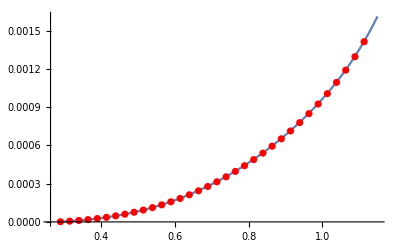

```mathematica
Show[{ListPlot[t00RTdat,Joined->True],ListPlot[t00RTR,PlotStyle->Red]}]
```

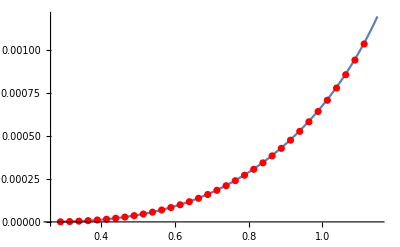

```mathematica
Show[{ListPlot[t11RTdat,Joined->True],ListPlot[t11RTR,PlotStyle->Red]}]
```

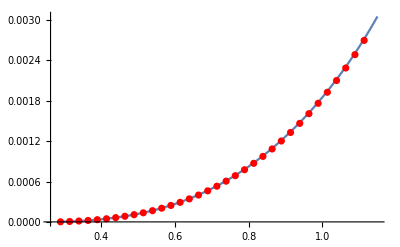

```mathematica
Show[{ListPlot[t20RTdat,Joined->True],ListPlot[t20RTR,PlotStyle->Red]}]
```

#### Checking with Kaminski

Comparing with Kaminski

1. We check that the Regge amplitudes coincide.

2. We check the integration kernels

```mathematica
g200=4/sth(2 t (8-sc*sp+(sc+sp)*t-2*(2*sp+t)))/ (3π*sp*(-4+sp)*(sp-t)*(-4+sp+t))/.sc-> 4s/sth/.t->4t/sth/.sp-> 4sp/sth//FullSimplify
```

(t (-((2 sp-sth) (sth-t))+2 s (-sp+t)))/(3 π sp (sp-sth) (sp-t) (sp-sth+t))

```mathematica
{1,0,0}.g2[s,t,sp].{1,0,0}//FullSimplify
```

(t (-((2 sp-sth) (sth-t))+2 s (-sp+t)))/(3 π sp (sp-sth) (sp-t) (sp-sth+t))

```mathematica
g201=4/sth(t (16+2 sp t+sc (3 sp+t)-4 (2*(sc+sp)+t)))/ (π sp*(-4+sp)*(sp-t) (-4+sp+t))/.sc-> 4s/sth/.t->4t/sth/.sp-> 4sp/sth//FullSimplify
```

(t (-((2 sp-sth) (sth-t))+s (3 sp-2 sth+t)))/(π sp (sp-sth) (sp-t) (sp-sth+t))

```mathematica
{1,0,0}.g2[s,t,sp].{0,1,0}//FullSimplify
```

(t (-((2 sp-sth) (sth-t))+s (3 sp-2 sth+t)))/(π sp (sp-sth) (sp-t) (sp-sth+t))

```mathematica
g202=4/sth(5t (16+sc (sp-t)+2 sp t-4 (2 sp+t)))/ (3 π sp (-4+sp) (sp-t) (-4+sp+t))/.sc-> 4s/sth/.t->4t/sth/.sp-> 4sp/sth//FullSimplify
```

(5 t (s sp-2 sp sth+sth^2-(s-2 sp+sth) t))/(3 π sp (sp-sth) (sp-t) (sp-sth+t))

```mathematica
{1,0,0}.g2[s,t,sp].{0,0,1}//FullSimplify
```

(5 t (s sp-2 sp sth+sth^2-(s-2 sp+sth) t))/(3 π sp (sp-sth) (sp-t) (sp-sth+t))

```mathematica
g300=-4/sth((sc*(1/(-sc+sp)+1/(3(-4+sc+sp+t)))*u)/(π*sp*(-4+sp+t)))/.sc-> 4s/sth/.t->4t/sth/.sp-> 4sp/sth/.u-> 4u/sth/.u-> sth-s-t//FullSimplify
```

-(s (s-sth+t) (2 s+4 sp-3 sth+3 t))/(3 π (s-sp) sp (sp-sth+t) (s+sp-sth+t))

```mathematica
{1,0,0}.g3[s,t,sp].{1,0,0}//FullSimplify//Together
```

-(s (s-sth+t) (2 s+4 sp-3 sth+3 t))/(3 π (s-sp) sp (sp-sth+t) (s+sp-sth+t))

```mathematica
g301=4/sth(sc*u)/(Pi*sp*(-4+sp+t)*(-4+sc+sp+t))/.sc-> 4s/sth/.t->4t/sth/.sp-> 4sp/sth/.u-> 4u/sth/.u-> sth-s-t//FullSimplify
```

-(s (s-sth+t))/(π sp (sp-sth+t) (s+sp-sth+t))

```mathematica
{1,0,0}.g3[s,t,sp].{0,1,0}//FullSimplify
```

-(s (s-sth+t))/(π sp (sp-sth+t) (s+sp-sth+t))

```mathematica
g302=4/sth(-5*sc*u)/(3 π*sp*(-4+sp+t)*(-4+sc+sp+t))/.sc-> 4s/sth/.t->4t/sth/.sp-> 4sp/sth/.u-> 4u/sth/.u-> sth-s-t//FullSimplify
```

(5 s (s-sth+t))/(3 π sp (sp-sth+t) (s+sp-sth+t))

```mathematica
{1,0,0}.g3[s,t,sp].{0,0,1}//FullSimplify
```

(5 s (s-sth+t))/(3 π sp (sp-sth+t) (s+sp-sth+t))

All kernels agree

3. Integration: Kaminski divides by 32 π but integrates from 0 to 1. Agrees with our -1 to 1 integration and 64π normalization factor.

### Total contribution

```mathematica
t00Roy[s_,parpwa_,parregge_]:=t00ST[s,parpwa]+t00KT[s,parpwa]+t00DT[s,parpwa]+t00RT[s,parregge]
```

```mathematica
t11Roy[s_,parpwa_,parregge_]:=t11ST[s,parpwa]+t11KT[s,parpwa]+t11DT[s,parpwa]+t11RT[s,parregge]
```

```mathematica
t20Roy[s_,parpwa_,parregge_]:=t20ST[s,parpwa]+t20KT[s,parpwa]+t20DT[s,parpwa]+t20RT[s,parregge]
```

```mathematica
t00RoyPWA[s_,parpwa_]:=t00ST[s,parpwa]+t00KT[s,parpwa]+t00DT[s,parpwa]
```

```mathematica
t11RoyPWA[s_,parpwa_]:=t11ST[s,parpwa]+t11KT[s,parpwa]+t11DT[s,parpwa]
```

```mathematica
t20RoyPWA[s_,parpwa_]:=t20ST[s,parpwa]+t20KT[s,parpwa]+t20DT[s,parpwa]
```

```mathematica
t00CFDRK=Table[{S0Roy[[i,1]]/1000,S0Roy[[i,2]]},{i,1,Length[S0Roy]}];
```

```mathematica
t00RoyRK=Table[{S0Roy[[i,1]]/1000,Around[S0Roy[[i,3]],{S0Roy[[i,3]]-S0Roy[[i,5]],S0Roy[[i,4]]-S0Roy[[i,3]]}]},{i,1,Length[S0Roy]}];
```

```mathematica
t11CFDRK=Table[{PRoy[[i,1]]/1000,PRoy[[i,2]]},{i,1,Length[PRoy]}];
```

```mathematica
t11RoyRK=Table[{PRoy[[i,1]]/1000,Around[PRoy[[i,3]],{PRoy[[i,3]]-PRoy[[i,5]],PRoy[[i,4]]-PRoy[[i,3]]}]},{i,1,Length[PRoy]}];
```

```mathematica
t20CFDRK=Table[{S2Roy[[i,1]]/1000,S2Roy[[i,2]]},{i,1,Length[S2Roy]}];
```

```mathematica
t20RoyRK=Table[{S2Roy[[i,1]]/1000,Around[S2Roy[[i,3]],{S2Roy[[i,3]]-S2Roy[[i,5]],S2Roy[[i,4]]-S2Roy[[i,3]]}]},{i,1,Length[S2Roy]}];
```

```mathematica
t00Roydat=Table[{t00KTdat[[i,1]],ST00dat[[i,2]]+t00KTdat[[i,2]]+t00DTdat[[i,2]]+t00RTdat[[i,2]]},{i,1,Length[t00KTdat]}];
```

```mathematica
t11Roydat=Table[{t11KTdat[[i,1]],ST11dat[[i,2]]+t11KTdat[[i,2]]+t11DTdat[[i,2]]+t11RTdat[[i,2]]},{i,1,Length[t11KTdat]}];
```

```mathematica
t20Roydat=Table[{t20KTdat[[i,1]],ST20dat[[i,2]]+t20KTdat[[i,2]]+t20DTdat[[i,2]]+t20RTdat[[i,2]]},{i,1,Length[t20KTdat]}];
```

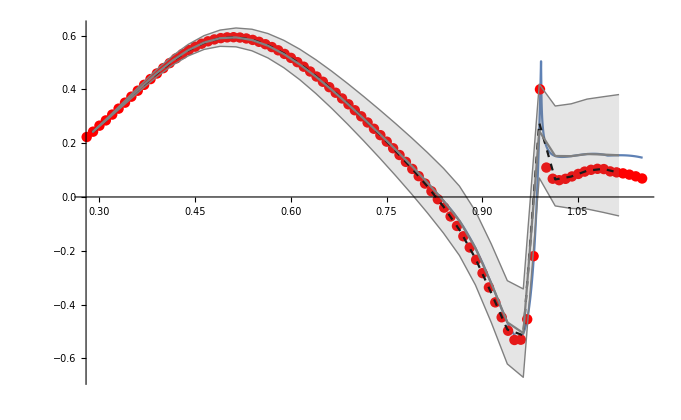

```mathematica
Show[Plot[Re[t00[W^2]/.S0par/.physval],{W,2M,√68 M}],ListPlot[t00Roydat,PlotStyle->Red],ListPlot[t00CFDRK,Joined->True,PlotStyle->{Dashed,Black}],ListLinePlot[t00RoyRK,IntervalMarkers->"Bands",PlotStyle->Gray],PlotRange->{0.65,-0.7}]
```

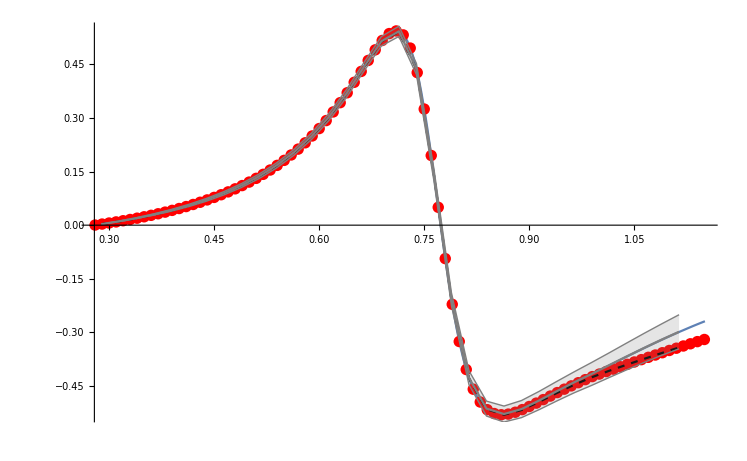

```mathematica
Show[Plot[Re[t11[W^2]/.Ppar/.physval],{W,2M,√68 M}],ListPlot[t11Roydat,PlotStyle->Red],ListPlot[t11CFDRK,Joined->True,PlotStyle->{Dashed,Black}],ListLinePlot[t11RoyRK,IntervalMarkers->"Bands",PlotStyle->Gray]]
```

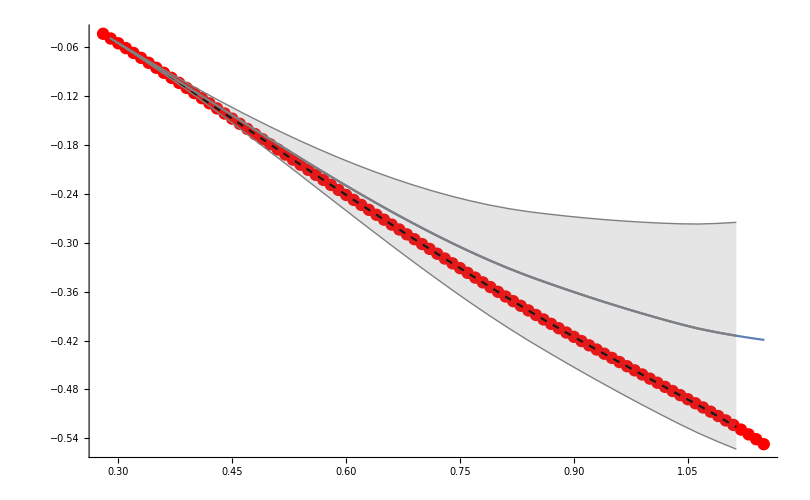

```mathematica
Show[Plot[Re[t20[W^2]/.S2par/.physval],{W,2M,√68 M}],ListPlot[t20Roydat,PlotStyle->Red],ListPlot[t20CFDRK,Joined->True,PlotStyle->{Dashed,Black}],ListLinePlot[t20RoyRK,IntervalMarkers->"Bands",PlotStyle->Gray],PlotRange-> All]
```

### Error calculation

#### Computing Roy for each parameter variation

```mathematica
nparRoyPWA=0;
nparRoyRegge=0;
For[k=1,k<=Length[par],k++,If[Δpar[[k,2]]>0,nparRoyPWA++]];
For[k=1,k<=Length[reggepar],k++,If[Δreggepar[[k,2]]>0,nparRoyRegge++]];
```

```mathematica
nparRoy=nparRoyPWA+nparRoyRegge;
```

```mathematica
{nparRoyPWA,nparRoyRegge,nparRoy}
```

{37,12,49}

```mathematica
t00RoyAll=Table[0,{i,1,2nparRoy+1}];
t11RoyAll=Table[0,{i,1,2nparRoy+1}];
t20RoyAll=Table[0,{i,1,2nparRoy+1}];
```

```mathematica
t00RoyAll[[1]]=Monitor[Table[{W,Re[t00Roy[W^2,par,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",W}];
t11RoyAll[[1]]=Monitor[Table[{W,Re[t11Roy[W^2,par,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"11",W}];
t20RoyAll[[1]]=Monitor[Table[{W,Re[t20Roy[W^2,par,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"20",W}];
```

```mathematica
t00RoyPWA0=Monitor[Table[{W,Re[t00RoyPWA[W^2,par]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",W}];
t11RoyPWA0=Monitor[Table[{W,Re[t11RoyPWA[W^2,par]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",W}];
t20RoyPWA0=Monitor[Table[{W,Re[t20RoyPWA[W^2,par]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",W}];
```

```mathematica
For[k=1;j=1,k<=Length[par],k++,par2=par;
If[Δpar[[k,2]]>0,j++;par2[[k,2]]=par[[k,2]]+Δpar[[k,2]];t00RoyAll[[j]]=Monitor[Table[{W,Re[t00Roy[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",k,j,W}];
t11RoyAll[[j]]=Monitor[Table[{W,Re[t11Roy[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"11",k,j,W}];t20RoyAll[[j]]=Monitor[Table[{W,Re[t20Roy[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"20",k,j,W}];]]
```

```mathematica
For[k=1;j=nparRoyPWA+1,k<=Length[reggepar],k++,reggepar2=reggepar;
If[Δreggepar[[k,2]]>0,j++;reggepar2[[k,2]]=reggepar[[k,2]]+Δreggepar[[k,2]];
t00Regge=Monitor[Table[{W,Re[t00RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",k,j,W}];
t00RoyAll[[j]]=Table[{t00RoyPWA0[[i,1]],t00RoyPWA0[[i,2]]+t00Regge[[i,2]]},{i,1,Length[t00RoyPWA0]}];
t11Regge=Monitor[Table[{W,Re[t11RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"11",k,j,W}];
t11RoyAll[[j]]=Table[{t11RoyPWA0[[i,1]],t11RoyPWA0[[i,2]]+t11Regge[[i,2]]},{i,1,Length[t11RoyPWA0]}];
t20Regge=Monitor[Table[{W,Re[t20RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"20",k,j,W}];t20RoyAll[[j]]=Table[{t20RoyPWA0[[i,1]],t20RoyPWA0[[i,2]]+t20Regge[[i,2]]},{i,1,Length[t20RoyPWA0]}];]]
```

```mathematica
For[k=1;j=nparRoy+1,k<=Length[par],k++,par2=par;
If[Δpar[[k,2]]>0,j++;par2[[k,2]]=par[[k,2]]-Δpar[[k,2]];t00RoyAll[[j]]=Monitor[Table[{W,Re[t00Roy[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",k,j,W}];
t11RoyAll[[j]]=Monitor[Table[{W,Re[t11Roy[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"11",k,j,W}];t20RoyAll[[j]]=Monitor[Table[{W,Re[t20Roy[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"20",k,j,W}];]]
```

```mathematica
For[k=1;j=nparRoy+nparRoyPWA+1,k<=Length[reggepar],k++,reggepar2=reggepar;
If[Δreggepar[[k,2]]>0,j++;reggepar2[[k,2]]=reggepar[[k,2]]-Δreggepar[[k,2]];
t00Regge=Monitor[Table[{W,Re[t00RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",k,j,W}];
t00RoyAll[[j]]=Table[{t00RoyPWA0[[i,1]],t00RoyPWA0[[i,2]]+t00Regge[[i,2]]},{i,1,Length[t00RoyPWA0]}];
t11Regge=Monitor[Table[{W,Re[t11RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"11",k,j,W}];
t11RoyAll[[j]]=Table[{t11RoyPWA0[[i,1]],t11RoyPWA0[[i,2]]+t11Regge[[i,2]]},{i,1,Length[t11RoyPWA0]}];
t20Regge=Monitor[Table[{W,Re[t20RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"20",k,j,W}];t20RoyAll[[j]]=Table[{t20RoyPWA0[[i,1]],t20RoyPWA0[[i,2]]+t20Regge[[i,2]]},{i,1,Length[t20RoyPWA0]}];]]
```

Export["t00RoyAll.dat", t00RoyAll, "xLS"];

Export["t11RoyAll.dat", t11RoyAll, "xLS"];

Export["t20RoyAll.dat", t20RoyAll, "xLS"];

#### Checking with Kaminski : looking for the error

```mathematica
par2=par;
```

```mathematica
par2[[3,2]]=par[[3,2]]+Δpar[[3,2]];
```

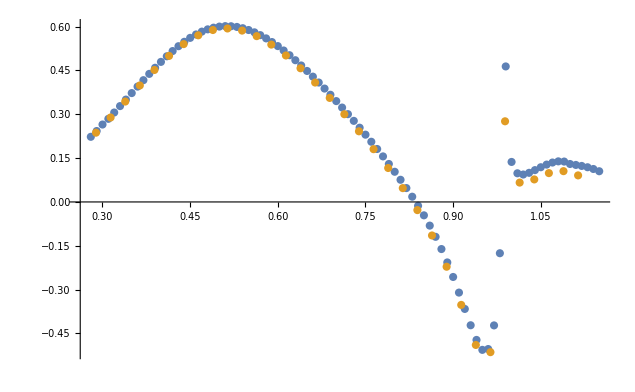

```mathematica
ListPlot[{t00RoyAll[[2]],Table[{S0Royerr[[i,1]]/1000,S0Royerr[[i,6]]},{i,1,Length[S0Royerr]}]}]
```

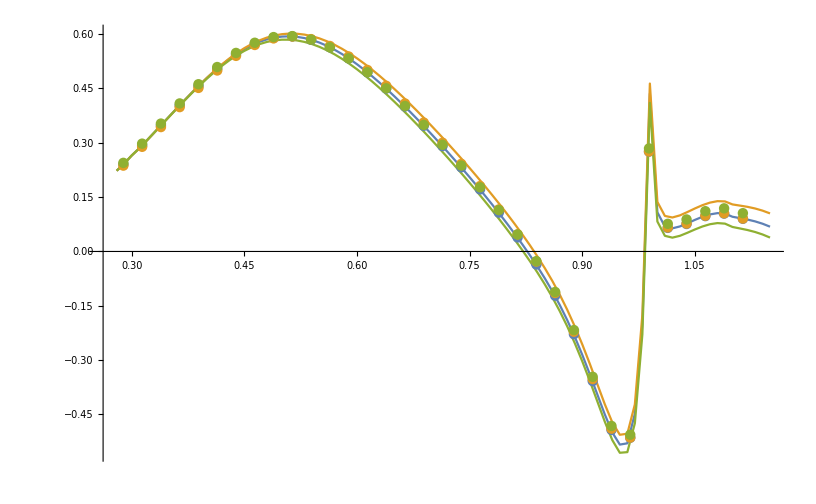

```mathematica
Show[ListPlot[{t00RoyAll[[1]],t00RoyAll[[2]],t00RoyAll[[3]]},Joined->True],ListPlot[{Table[{S0Royerr[[i,1]]/1000,S0Royerr[[i,2]]},{i,1,Length[S0Royerr]}],Table[{S0Royerr[[i,1]]/1000,S0Royerr[[i,6]]},{i,1,Length[S0Royerr]}],Table[{S0Royerr[[i,1]]/1000,S0Royerr[[i,7]]},{i,1,Length[S0Royerr]}]}]]
```

#### Computing CFD for each parameter variation

```mathematica
t00CFDAll=Table[0,{i,1,2nparRoy+1}];
t11CFDAll=Table[0,{i,1,2nparRoy+1}];
t20CFDAll=Table[0,{i,1,2nparRoy+1}];
```

```mathematica
t00CFDAll[[1]]=Monitor[Table[{W,Re[t00[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",W}];
t11CFDAll[[1]]=Monitor[Table[{W,Re[t11[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"11",W}];
t20CFDAll[[1]]=Monitor[Table[{W,Re[t20[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"20",W}];
```

```mathematica
For[k=1;j=1,k<=Length[par],k++,par2=par;
If[Δpar[[k,2]]>0,j++;par2[[k,2]]=par[[k,2]]+Δpar[[k,2]];
t00CFDAll[[j]]=Monitor[Table[{W,Re[t00[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",k,j,W}];
t11CFDAll[[j]]=Monitor[Table[{W,Re[t11[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"11",k,j,W}];t20CFDAll[[j]]=Monitor[Table[{W,Re[t20[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"20",k,j,W}];]]
```

```mathematica
For[k=1;j=nparRoyPWA+1,k<=Length[reggepar],k++,reggepar2=reggepar;
If[Δreggepar[[k,2]]>0,j++;reggepar2[[k,2]]=reggepar[[k,2]]+Δreggepar[[k,2]];
t00CFDAll[[j]]=Monitor[Table[{W,Re[t00[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",k,j,W}];
t11CFDAll[[j]]=Monitor[Table[{W,Re[t11[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"11",k,j,W}];t20CFDAll[[j]]=Monitor[Table[{W,Re[t20[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"20",k,j,W}];]]
```

```mathematica
For[k=1;j=nparRoy+1,k<=Length[par],k++,par2=par;
If[Δpar[[k,2]]>0,j++;par2[[k,2]]=par[[k,2]]-Δpar[[k,2]];
t00CFDAll[[j]]=Monitor[Table[{W,Re[t00[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",k,j,W}];
t11CFDAll[[j]]=Monitor[Table[{W,Re[t11[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"11",k,j,W}];t20CFDAll[[j]]=Monitor[Table[{W,Re[t20[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"20",k,j,W}];]]
```

```mathematica
For[k=1;j=nparRoy+nparRoyPWA+1,k<=Length[reggepar],k++,reggepar2=reggepar;
If[Δreggepar[[k,2]]>0,j++;reggepar2[[k,2]]=reggepar[[k,2]]-Δreggepar[[k,2]];
t00CFDAll[[j]]=Monitor[Table[{W,Re[t00[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"00",k,j,W}];
t11CFDAll[[j]]=Monitor[Table[{W,Re[t11[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"11",k,j,W}];t20CFDAll[[j]]=Monitor[Table[{W,Re[t20[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.01}],{"20",k,j,W}];]]
```

#### Importing Data

```mathematica
t00RoyAll = Import["RoyAll/t00RoyAll.dat", "xLS"];
```

```mathematica
t11RoyAll = Import["RoyAll/t11RoyAll.dat", "xLS"];
```

```mathematica
t20RoyAll = Import["RoyAll/t20RoyAll.dat", "xLS"];
```

#### Error bands Roy

```mathematica
t00RoyΔ=Table[√Sum[If[(t00RoyAll[[k,i,2]]-t00RoyAll[[1,i,2]])^2>(t00RoyAll[[k+nparRoy,i,2]]-t00RoyAll[[1,i,2]])^2,(t00RoyAll[[k,i,2]]-t00RoyAll[[1,i,2]])^2,(t00RoyAll[[k+nparRoy,i,2]]-t00RoyAll[[1,i,2]])^2],{k,2,nparRoy+1}],{i,1,Length[t00RoyAll[[1]]]}];
```

```mathematica
t11RoyΔ=Table[√Sum[If[(t11RoyAll[[k,i,2]]-t11RoyAll[[1,i,2]])^2>(t11RoyAll[[k+nparRoy,i,2]]-t11RoyAll[[1,i,2]])^2,(t11RoyAll[[k,i,2]]-t11RoyAll[[1,i,2]])^2,(t11RoyAll[[k+nparRoy,i,2]]-t11RoyAll[[1,i,2]])^2],{k,2,nparRoy+1}],{i,1,Length[t11RoyAll[[1]]]}];
```

```mathematica
t20RoyΔ=Table[√Sum[If[(t20RoyAll[[k,i,2]]-t20RoyAll[[1,i,2]])^2>(t20RoyAll[[k+nparRoy,i,2]]-t20RoyAll[[1,i,2]])^2,(t20RoyAll[[k,i,2]]-t20RoyAll[[1,i,2]])^2,(t20RoyAll[[k+nparRoy,i,2]]-t20RoyAll[[1,i,2]])^2],{k,2,nparRoy+1}],{i,1,Length[t20RoyAll[[1]]]}];
```

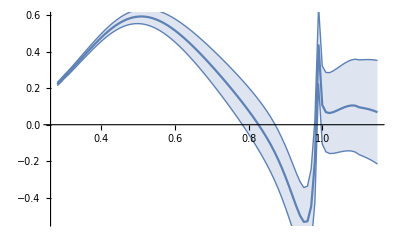

```mathematica
t00RoyPlot=ListLinePlot[Table[{t00RoyAll[[1,i,1]],t00RoyAll[[1,i,2]]±t00RoyΔ[[i]]},{i,1,Length[t00RoyAll[[1]]]}],IntervalMarkers->"Bands"]
```

```mathematica
t00RoyPlotRK=ListLinePlot[Table[{S0Royerr[[i,1]]/1000,S0Royerr[[i,2]]±S0Royerr[[i,3]]},{i,1,Length[S0Royerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

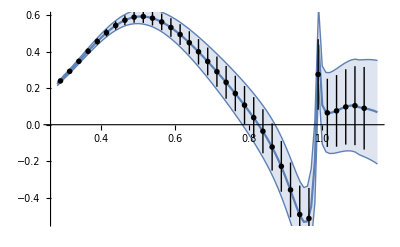

```mathematica
Show[t00RoyPlot,t00RoyPlotRK]
```

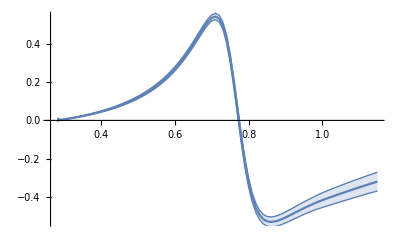

```mathematica
t11RoyPlot=ListLinePlot[Table[{t11RoyAll[[1,i,1]],t11RoyAll[[1,i,2]]±t11RoyΔ[[i]]},{i,1,Length[t11RoyAll[[1]]]}],IntervalMarkers->"Bands"]
```

```mathematica
t11RoyPlotRK=ListLinePlot[Table[{PRoyerr[[i,1]]/1000,PRoyerr[[i,2]]±PRoyerr[[i,3]]},{i,1,Length[PRoyerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

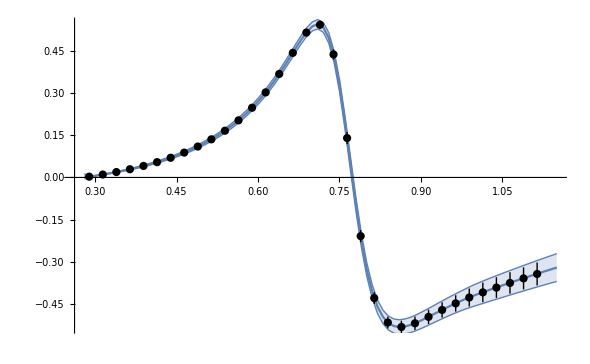

```mathematica
Show[t11RoyPlot,t11RoyPlotRK]
```

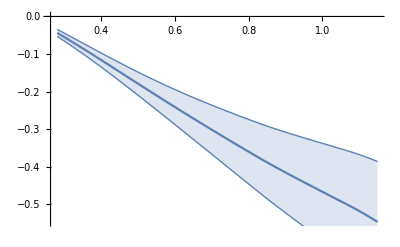

```mathematica
t20RoyPlot=ListLinePlot[Table[{t20RoyAll[[1,i,1]],t20RoyAll[[1,i,2]]±t20RoyΔ[[i]]},{i,1,Length[t20RoyAll[[1]]]}],IntervalMarkers->"Bands"]
```

```mathematica
t20RoyPlotRK=ListLinePlot[Table[{S2Royerr[[i,1]]/1000,S2Royerr[[i,2]]±S2Royerr[[i,3]]},{i,1,Length[S2Royerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

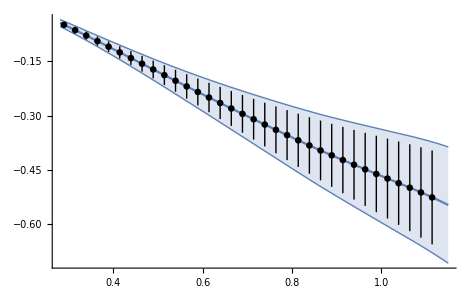

```mathematica
Show[t20RoyPlot,t20RoyPlotRK,PlotRange-> All]
```

#### Error bands CFD

```mathematica
Δerr[f_,r_,Δr_,n_]:=√(∑_(i=1)^n (D[f, r[[i,1]]])^2 Δr[[i,2]]^2);
```

```mathematica
ΔRet00[s_]:=Re[Δerr[t00[s],S0par,ΔS0par,Length[S0par]]/.par/.physval];
ΔRet11[s_]:=Re[Δerr[t11[s],Ppar,ΔPpar,Length[Ppar]]/.par/.physval];
ΔRet20[s_]:=Re[Δerr[t20[s],S2par,ΔS2par,Length[S2par]]/.par/.physval];
```

```mathematica
t00CFDΔ=Table[√Sum[If[(t00CFDAll[[k,i,2]]-t00CFDAll[[1,i,2]])^2>(t00CFDAll[[k+nparRoy,i,2]]-t00CFDAll[[1,i,2]])^2,(t00CFDAll[[k,i,2]]-t00CFDAll[[1,i,2]])^2,(t00CFDAll[[k+nparRoy,i,2]]-t00CFDAll[[1,i,2]])^2],{k,2,nparRoy+1}],{i,1,Length[t00RoyAll[[1]]]}];
```

```mathematica
t11CFDΔ=Table[√Sum[If[(t11CFDAll[[k,i,2]]-t11CFDAll[[1,i,2]])^2>(t11CFDAll[[k+nparRoy,i,2]]-t11CFDAll[[1,i,2]])^2,(t11CFDAll[[k,i,2]]-t11CFDAll[[1,i,2]])^2,(t11CFDAll[[k+nparRoy,i,2]]-t11CFDAll[[1,i,2]])^2],{k,2,nparRoy+1}],{i,1,Length[t11RoyAll[[1]]]}];
```

```mathematica
t20CFDΔ=Table[√Sum[If[(t20CFDAll[[k,i,2]]-t20CFDAll[[1,i,2]])^2>(t20CFDAll[[k+nparRoy,i,2]]-t20CFDAll[[1,i,2]])^2,(t20CFDAll[[k,i,2]]-t20CFDAll[[1,i,2]])^2,(t20CFDAll[[k+nparRoy,i,2]]-t20CFDAll[[1,i,2]])^2],{k,2,nparRoy+1}],{i,1,Length[t20RoyAll[[1]]]}];
```

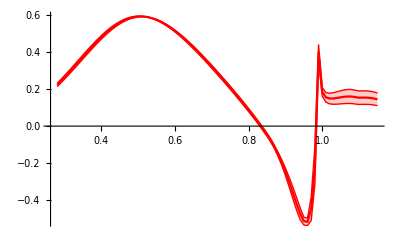

```mathematica
t00CFDPlot=ListLinePlot[Table[{t00CFDAll[[1,i,1]],t00CFDAll[[1,i,2]]±t00CFDΔ[[i]]},{i,1,Length[t00CFDAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Red]
```

```mathematica
t00CFDPlotRK=ListLinePlot[Table[{S0Royerr[[i,1]]/1000,S0Royerr[[i,4]]±S0Royerr[[i,5]]},{i,1,Length[S0Royerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

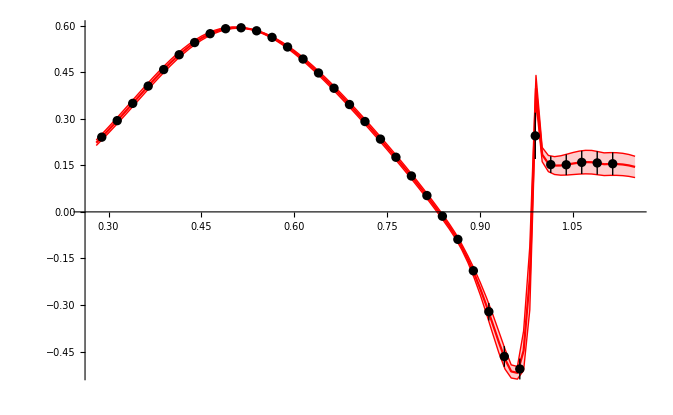

```mathematica
Show[t00CFDPlot,t00CFDPlotRK]
```

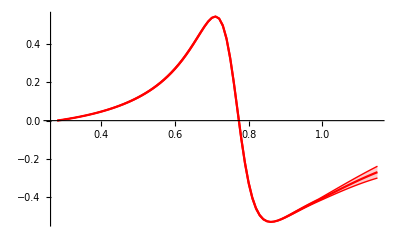

```mathematica
t11CFDPlot=ListLinePlot[Table[{t11CFDAll[[1,i,1]],t11CFDAll[[1,i,2]]±t11CFDΔ[[i]]},{i,1,Length[t11CFDAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Red]
```

```mathematica
t11CFDPlotRK=ListLinePlot[Table[{PRoyerr[[i,1]]/1000,PRoyerr[[i,4]]±PRoyerr[[i,5]]},{i,1,Length[PRoyerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

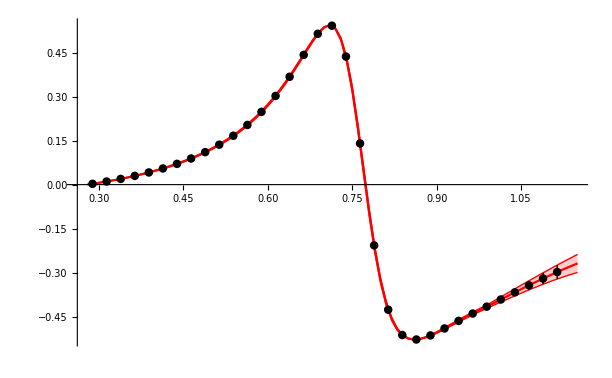

```mathematica
Show[t11CFDPlot,t11CFDPlotRK]
```

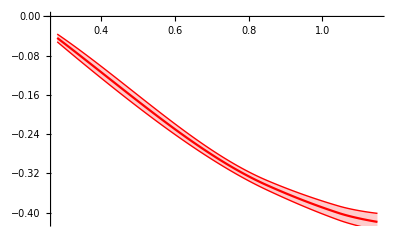

```mathematica
t20CFDPlot=ListLinePlot[Table[{t20CFDAll[[1,i,1]],t20CFDAll[[1,i,2]]±t20CFDΔ[[i]]},{i,1,Length[t20CFDAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Red]
```

```mathematica
t20CFDPlotRK=ListLinePlot[Table[{S2Royerr[[i,1]]/1000,S2Royerr[[i,4]]±S2Royerr[[i,5]]},{i,1,Length[S2Royerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

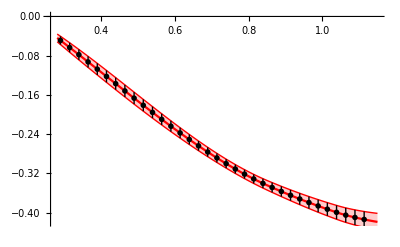

```mathematica
Show[t20CFDPlot,t20CFDPlotRK]
```

```mathematica
t00CFDPlot2=ListLinePlot[Table[{t00RoyAll[[1,i,1]],Re[t00[t00RoyAll[[1,i,1]]^2]/.par/.physval]±ΔRet00[t00RoyAll[[1,i,1]]^2]},{i,1,Length[t00RoyAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Green];t11CFDPlot2=ListLinePlot[Table[{t11RoyAll[[1,i,1]],Re[t11[t11RoyAll[[1,i,1]]^2]/.par/.physval]±ΔRet11[t11RoyAll[[1,i,1]]^2]},{i,1,Length[t11RoyAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Green];
t20CFDPlot2=ListLinePlot[Table[{t20RoyAll[[1,i,1]],Re[t20[t20RoyAll[[1,i,1]]^2]/.par/.physval]±ΔRet20[t20RoyAll[[1,i,1]]^2]},{i,1,Length[t20RoyAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Green];
```

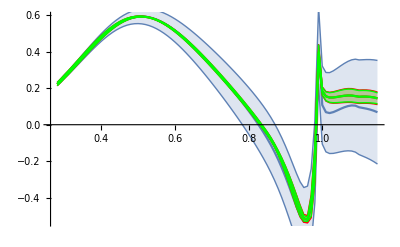

```mathematica
Show[t00RoyPlot,t00CFDPlot,t00CFDPlot2]
```

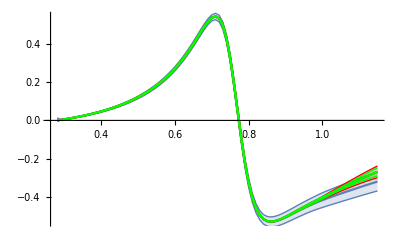

```mathematica
Show[t11RoyPlot,t11CFDPlot,t11CFDPlot2]
```

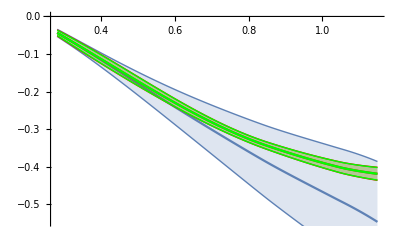

```mathematica
Show[t20RoyPlot,t20CFDPlot,t20CFDPlot2]
```

#### Error for the difference

```mathematica
t00RoyDiff=Table[Table[{t00RoyAll[[k,i,1]],t00RoyAll[[k,i,2]]-t00CFDAll[[k,i,2]]},{i,1,Length[t00RoyAll[[k]]]}],{k,1,Length[t00RoyAll]}];
t11RoyDiff=Table[Table[{t11RoyAll[[k,i,1]],t11RoyAll[[k,i,2]]-t11CFDAll[[k,i,2]]},{i,1,Length[t11RoyAll[[k]]]}],{k,1,Length[t11RoyAll]}];
t20RoyDiff=Table[Table[{t20RoyAll[[k,i,1]],t20RoyAll[[k,i,2]]-t20CFDAll[[k,i,2]]},{i,1,Length[t20RoyAll[[k]]]}],{k,1,Length[t20RoyAll]}];
```

```mathematica
t00RoyDiffΔ=Table[√Sum[If[(t00RoyDiff[[k,i,2]]-t00RoyDiff[[1,i,2]])^2>(t00RoyDiff[[k+nparRoy,i,2]]-t00RoyDiff[[1,i,2]])^2,(t00RoyDiff[[k,i,2]]-t00RoyDiff[[1,i,2]])^2,(t00RoyDiff[[k+nparRoy,i,2]]-t00RoyDiff[[1,i,2]])^2],{k,2,nparRoy+1}],{i,1,Length[t00RoyDiff[[1]]]}];
```

```mathematica
t11RoyDiffΔ=Table[√Sum[If[(t11RoyDiff[[k,i,2]]-t11RoyDiff[[1,i,2]])^2>(t11RoyDiff[[k+nparRoy,i,2]]-t11RoyDiff[[1,i,2]])^2,(t11RoyDiff[[k,i,2]]-t11RoyDiff[[1,i,2]])^2,(t11RoyDiff[[k+nparRoy,i,2]]-t11RoyDiff[[1,i,2]])^2],{k,2,nparRoy+1}],{i,1,Length[t11RoyDiff[[1]]]}];
```

```mathematica
t20RoyDiffΔ=Table[√Sum[If[(t20RoyDiff[[k,i,2]]-t20RoyDiff[[1,i,2]])^2>(t20RoyDiff[[k+nparRoy,i,2]]-t20RoyDiff[[1,i,2]])^2,(t20RoyDiff[[k,i,2]]-t20RoyDiff[[1,i,2]])^2,(t20RoyDiff[[k+nparRoy,i,2]]-t20RoyDiff[[1,i,2]])^2],{k,2,nparRoy+1}],{i,1,Length[t20RoyDiff[[1]]]}];
```

```mathematica
t00RoyDiffPlot=ListLinePlot[Table[{t00RoyDiff[[1,i,1]],t00CFDAll[[1,i,2]]±t00RoyDiffΔ[[i]]},{i,1,Length[t00RoyAll[[1]]]}],IntervalMarkers->"Bands"];
```

```mathematica
t11RoyDiffPlot=ListLinePlot[Table[{t11RoyDiff[[1,i,1]],t11CFDAll[[1,i,2]]±t11RoyDiffΔ[[i]]},{i,1,Length[t11RoyAll[[1]]]}],IntervalMarkers->"Bands"];
```

```mathematica
t20RoyDiffPlot=ListLinePlot[Table[{t20RoyDiff[[1,i,1]],t20CFDAll[[1,i,2]]±t20RoyDiffΔ[[i]]},{i,1,Length[t20RoyAll[[1]]]}],IntervalMarkers->"Bands",PlotRange-> {0,-0.6}];
```

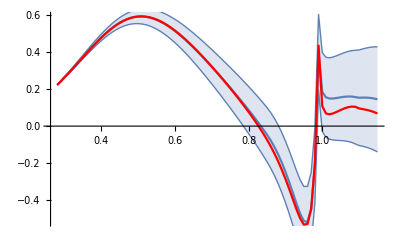

```mathematica
Show[t00RoyDiffPlot,ListLinePlot[Table[{t00RoyAll[[1,i,1]],t00RoyAll[[1,i,2]]},{i,1,Length[t00RoyAll[[1]]]}],PlotStyle->Red]]
```

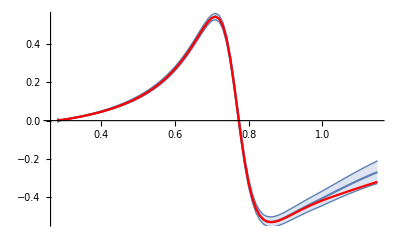

```mathematica
Show[t11RoyDiffPlot,ListLinePlot[Table[{t11RoyAll[[1,i,1]],t11RoyAll[[1,i,2]]},{i,1,Length[t11RoyAll[[1]]]}],PlotStyle->Red]]
```

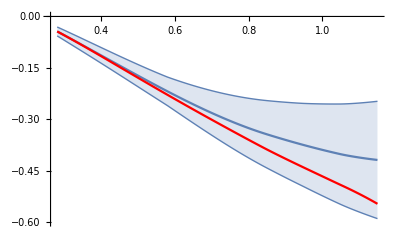

```mathematica
Show[t20RoyDiffPlot,ListLinePlot[Table[{t20RoyAll[[1,i,1]],t20RoyAll[[1,i,2]]},{i,1,Length[t20RoyAll[[1]]]}],PlotStyle->Red]]
```

## GKPY equations

The fixed-t and fixed-s dispersion relation for the three ππ amplitudes is

T(s,t)=32πC_st (a_00 ,0, a_20)+∫_s_th^∞ g_4(s,t,sp)ImT(sp,0)ⅆsp+∫_s_th^∞ g_5(s,t,sp)ImT(sp,t)ⅆsp

```mathematica
Off[NIntegrate::slwcon]
```

```mathematica
Off[NIntegrate::ncvb]
```

```mathematica
par=Join[S0par,Ppar,S2par,D0par,D2par,Fpar];
Δpar=Join[ΔS0par,ΔPpar,ΔS2par,ΔD0par,ΔD2par,ΔFpar];
```

### Kinematics

```mathematica
tt[s_,z_]=1/2(sth-s)(1-z);
```

```mathematica
Solve[tt[s,z]==t,z]//FullSimplify
```

{{z→1+(2 t)/(s-sth)}}

```mathematica
zp[s_,sp_,z_]=1+(2 tt[s,z])/(sp-sth);
```

```mathematica
Solve[tt[s,z]==0,z]
```

{{z→1}}

```mathematica
toRK1={pi-> π,y1->(1/2)*Log[((-4+s+2*sp)/(4+s-2*sp))],y2->1/2*Log[(-((-4+s+sp)/(-4+sp)))],var->((4+s-2*sp)/(8-2*sp)),var0->(-4-s+2*sp),var1->((-4+s+2*sp)/(4+s-2*sp)),var2->(-((-4+s+sp)/(-4+sp))),var3->(-s^2+4*(-2+sp)^2),CDLOG->Log,Log2->Log[2],Log4->Log[4],Log16->Log[16],Log256->Log[256]};
```

```mathematica
toRK2={s-> (4 s)/sth,sp-> (4 sp)/sth};
```

### Crossing matrices

```mathematica
II=IdentityMatrix[3];
```

```mathematica
Cst={{1/3,1,5/3},{1/3,1/2,-5/6},{1/3,-1/2,1/6}};
```

```mathematica
Ctu={{1,0,0},{0,-1,0},{0,0,1}};
```

```mathematica
Csu={{1/3,-1,5/3},{-1/3,1/2,5/6},{1/3,1/2,1/6}};
```

```mathematica
Cst.Cst//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Ctu.Ctu//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Csu.Csu//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Cst.Ctu-Ctu.Csu//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
Cst.Csu-Ctu.Cst
```

{{0,0,0},{0,0,0},{0,0,0}}

### g4 and g5 functions

```mathematica
g4[s_,t_,sp_]=(t-sth)/π Cst.(II/((sp-t)(sp-sth))-Csu/(sp(sp-sth+t)));
```

```mathematica
g5[s_,t_,sp_]=s/π(II/(sp(sp-s))-Csu/((sp-sth+t)(sp-sth+s+t)));
```

### Partial-wave expansion

First the partial-wave expansion

```mathematica
KRY[s_,sp_,z_,Jp_]=(2Jp+1)(g4[s,tt[s,z],sp]+g5[s,tt[s,z],sp]LegendreP[Jp,zp[s,sp,z]]);
```

Contributions to I=0

```mathematica
KRY00[s_,sp_,z_,Jp_]=FullSimplify[{1,0,0}.KRY[s,sp,z,Jp].{1,0,0}];
```

```mathematica
KRY01[s_,sp_,z_,Jp_]=FullSimplify[{1,0,0}.KRY[s,sp,z,Jp].{0,1,0}];
```

```mathematica
KRY02[s_,sp_,z_,Jp_]=FullSimplify[{1,0,0}.KRY[s,sp,z,Jp].{0,0,1}];
```

Contributions to I=1

```mathematica
KRY10[s_,sp_,z_,Jp_]=FullSimplify[{0,1,0}.KRY[s,sp,z,Jp].{1,0,0}];
```

```mathematica
KRY11[s_,sp_,z_,Jp_]=FullSimplify[{0,1,0}.KRY[s,sp,z,Jp].{0,1,0}];
```

```mathematica
KRY12[s_,sp_,z_,Jp_]=FullSimplify[{0,1,0}.KRY[s,sp,z,Jp].{0,0,1}];
```

Contributions to I=2

```mathematica
KRY20[s_,sp_,z_,Jp_]=FullSimplify[{0,0,1}.KRY[s,sp,z,Jp].{1,0,0}];
```

```mathematica
KRY21[s_,sp_,z_,Jp_]=FullSimplify[{0,0,1}.KRY[s,sp,z,Jp].{0,1,0}];
```

```mathematica
KRY22[s_,sp_,z_,Jp_]=FullSimplify[{0,0,1}.KRY[s,sp,z,Jp].{0,0,1}];
```

Second we consider the partial-wave projection. To be done in the next subsections

### Kernels for the S0 wave

#### Contributions from I = 0 partial waves

II’=00

```mathematica
KKRY00[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KRY00[s,sp,z,Jp],{z,0,1}]]]
```

00 to 00, S0 to S0

```mathematica
KRY0000[s_,sp_]=KKRY00[s,sp,0,0]
```

(-4/sp+3/(-s+sp)+1/(-sp+sth)+(2 (Log[s+2 sp-sth]-Log[sp (-s-2 sp+sth)]+Log[-s-sp+sth]))/(s-sth))/(3 π)

```mathematica
KRY0000S[s_,sp_]=1/π 1/(sp-s)-(5sp-4sth)/(3π sp(sp-sth))+2/(3 π (s-sth))Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[KRY0000[s,sp]-KRY0000S[s,sp],s>sp>sth>0]
```

0

```mathematica
KRY0000R[s_,sp_]=4/sth((-6 s)/(pi*s*sp-pi*sp^2)- (2*(-4+s+sp*Log4-Log256- 2*(-4+sp)*CDLOG[(-4+s+2*sp)/sp]))/(pi*(-4+s)*(-4+sp))- (2*(-4+s+2*sp*CDLOG[var]))/(pi*(-4+s)*sp)-(4*(Log[-4+sp]-CDLOG[-4+s+sp]+CDLOG[-4+s+2*sp]- CDLOG[var0]))/(pi(-4+s)))/6/.toRK1/.toRK2//FullSimplify
```

-(1/sp+(3 s)/((s-sp) sp)+(-s+sth+(-sp+sth) Log[4]+2 (sp-sth) Log[(s+2 sp-sth)/sp])/((s-sth) (-sp+sth))+(2 Log[-(s-2 sp+sth)/(2 sp-2 sth)])/(s-sth)+(2 (Log[-4+(4 sp)/sth]-Log[-1+(s+sp)/sth]+Log[-1+(s+2 sp)/sth]-Log[-(4 (s-2 sp+sth))/sth]))/(s-sth))/(3 π)

```mathematica
FullSimplify[KRY0000S[s,sp]-KRY0000R[s,sp],sp>s>sth>0]
```

0

02 to 00, D0 to S0

```mathematica
KRY0002[s_,sp_]=Collect[KKRY00[s,sp,0,2]//TrigToExp,Log[x_],FullSimplify]
```

-(5 (3 s^2+6 s sp+4 sp^2+3 s sth-6 sp sth+2 sth^2))/(6 π sp (sp-sth)^2)-(10 Log[sp])/(3 π s-3 π sth)+(10 Log[1-s/(2 sp-sth)])/(3 π s-3 π sth)-(10 Log[1+s/(2 sp-sth)])/(3 π s-3 π sth)+(10 Log[s+sp-sth])/(3 π s-3 π sth)+(20 s (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^2)-(10 Log[1/(s+2 sp-sth)])/(3 π s-3 π sth)-(20 s (s+sp-sth) Log[s+2 sp-sth])/(π (s-sth) (sp-sth)^2)+(10 Log[-1/(s-2 sp+sth)])/(3 π s-3 π sth)

```mathematica
KRY0002S[s_,sp_]=-5/(3 π sp)-(5 s (s+3 sp))/(2 π sp (sp-sth)^2)+(5 (3 s-2 sp))/(6 π sp (sp-sth))+10/(3π(s- sth))(Log[1+(s-sth)/sp]+(6s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+ 2sp-sth)]);
```

```mathematica
FullSimplify[KRY0002S[s,sp]-KRY0002[s,sp],{sp>s>sth>0}]
```

0

04 to 00, G0 to S0

```mathematica
KRY0004[s_,sp_]=Collect[KKRY00[s,sp,0,4]//TrigToExp,Log[x_],FullSimplify]
```

(-63 s^4-24 (sp-sth)^3 (2 sp-sth)-7 s^3 (284 sp+9 sth)+s^2 (-1968 sp^2+2452 sp sth+27 sth^2)+s (-408 sp^3+1032 sp^2 sth-728 sp sth^2+27 sth^3))/(8 π sp (sp-sth)^4)+(6 Log[1-s/(2 sp-sth)])/(π s-π sth)-(6 Log[1+s/(2 sp-sth)])/(π s-π sth)+(6 Log[s+sp-sth])/(π s-π sth)+(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^4)-(6 Log[sp/(s+2 sp-sth)])/(π s-π sth)+(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[s+2 sp-sth])/(π (sp-sth)^4 (-s+sth))+(6 Log[-1/(s-2 sp+sth)])/(π s-π sth)

```mathematica
KRY0004S[s_,sp_]=-3/(π sp)-(7 s (9 s^3+293 s^2 sp-73 s sp^2+11 sp^3))/(8 π sp (sp-sth)^4)+(7 s (9 s^2-358 s sp+49 sp^2))/(8 π sp (sp-sth)^3)+(s (27 s-647 sp))/(8 π sp (sp-sth)^2)-(27 s+24 sp)/(8 π sp (sp-sth))+6/(π(s-sth))( Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+ 2sp-sth)] );
```

```mathematica
FullSimplify[KRY0004S[s,sp]-KRY0004[s,sp],sp>s>sth>0]
```

0

#### Contributions from I = 1 partial waves

II’=01

```mathematica
KKRY01[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KRY01[s,sp,z,Jp],{z,0,1}]]]
```

11 to 00, P to S0

```mathematica
KRY0011[s_,sp_]=Collect[KKRY01[s,sp,0,1],Log[x_],FullSimplify]
```

(3 (-2 sp+sth))/(π sp (sp-sth))+(3 s Log[16])/(π (s-sth) (sp-sth))+(6 Log[s+2 sp-sth])/(π s-π sth)+(12 s Log[-s-2 sp+sth])/(π (s-sth) (-sp+sth))-(6 Log[sp (-s-2 sp+sth)])/(π s-π sth)+(6 (2 s+sp-sth) Log[-s-sp+sth])/(π (s-sth) (sp-sth))

```mathematica
KRY0011S[s_,sp_]=-3/(π sp)-3/(π (sp-sth))+6/(π(s-sth))( Log[1+(s-sth)/sp]+(2 s)/(sp-sth)Log[1+(s-sth)/(s+2 sp-sth)]);
```

```mathematica
FullSimplify[KRY0011S[s,sp]-KRY0011[s,sp],s>sp>sth>0]
```

0

```mathematica
KRY0011R[s_,sp_]=-4/sth(18*(16-4*s-8*sp+2*s*sp-16*sp*y1+4*s*sp*y1+ 4*sp^2*y1+16*sp*y2-4*s*sp*y2-4*sp^2*y2+sp^2*Log4- sp*Log256-2*(-4+sp)*sp*CDLOG[(-4+s+2*sp)/sp]+ 2*(-4+sp)*sp*CDLOG[var]+ 2*s*sp*CDLOG[var3/(4*(-4+sp)*(-4+s+sp))]))/(pi*(-4+s)*(-4+sp)*sp)/6/.toRK1/.toRK2//FullSimplify
```

1/(π sp (sp-sth) (-s+sth))(-3 (s-sth) (-2 sp+sth)+6 sp ((-sp+sth) Log[(s+2 sp-sth)/sp]+(sp-sth) Log[-(s-2 sp+sth)/(2 sp-2 sth)]+s (Log[(-s^2+(-2 sp+sth)^2)/(4 (sp-sth) (s+sp-sth))]+Log[-1+(2 s)/(s-2 sp+sth)])+(sp-sth) Log[-2+(4 s)/(s-2 sp+sth)]-(s+sp-sth) Log[-1+s/(-sp+sth)]))

```mathematica
FullSimplify[KRY0011R[s,sp]-KRY0011S[s,sp],sp>s>sth>0]
```

0

31 to 00, F to S0

```mathematica
KRY0013[s_,sp_]=Collect[KKRY01[s,sp,0,3],Log[x_],FullSimplify]
```

7 ((2 ⅈ)/(-s+sth)+(-25 s^2 sp-(sp-sth)^2 (2 sp-sth)+5 s sp (-2 sp+3 sth))/(π sp (sp-sth)^3))-(14 Log[sp])/(π s-π sth)+(14 Log[s+sp-sth])/(π s-π sth)-(28 s (10 s^2+15 s (sp-sth)+6 (sp-sth)^2) Log[2 (s+sp-sth)])/(π (sp-sth)^3 (-s+sth))+(14 (10 s^2+10 s (sp-sth)+(sp-sth)^2) (2 s+sp-sth) Log[s+2 sp-sth])/(π (s-sth) (-sp+sth)^3)+(14 Log[-s-2 sp+sth])/(π s-π sth)

```mathematica
KRY0013S[s_,sp_]=-7/(π sp)+(35 s (-5 s+sp))/(π (sp-sth)^3)-(105 s)/(π (sp-sth)^2)-7/(π (sp-sth))+14/(π(s-sth))(Log[1+(s-sth)/sp]+(2 s (10 s^2+15 s (sp-sth)+6 (sp-sth)^2))/(sp-sth)^3 Log[1+(s-sth)/(s+2 sp-sth)]);
```

```mathematica
FullSimplify[KRY0013S[s,sp]-KRY0013[s,sp],sp>sth>s>0]
```

0

#### Contributions from I = 2 partial waves

II’=02

```mathematica
KKRY02[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KRY02[s,sp,z,Jp],{z,0,1}]]]
```

20 to 00, S2 to S0

```mathematica
KRY0020[s_,sp_]=KKRY02[s,sp,0,0]
```

(5 (-((s-sth) (-2 sp+sth))+2 sp (sp-sth) (Log[sp]-Log[s+sp-sth])))/(3 π sp (sp-sth) (-s+sth))

```mathematica
KRY0020S[s_,sp_]=-5/(3 π sp)-5/(3 π (sp-sth))+10/(3 π  (s-sth)) Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[KRY0020S[s,sp]-KRY0020[s,sp],sp>s>sth>0]
```

0

```mathematica
KRY0020R[s_,sp_]=4/sth(10((4-s-sp*Log4+Log256+ 2*(-4+sp)*CDLOG[(-4+s+2*sp)/sp])/(-4+sp)-(-4+s+2*sp*CDLOG[var])/sp-2*(Log[-4+sp]-CDLOG[-4+s+sp]+CDLOG[-4+s+2*sp]-CDLOG[var0])))/(pi*(-4+s))/6/.toRK1/.toRK2//FullSimplify
```

(5 (-1/sp+1/(-sp+sth)+(2 (-Log[1+(-s+sp)/(sp-sth)]-Log[-1+sp/sth]+Log[-1+(s+sp)/sth]-Log[-1+(s+2 sp)/sth]+Log[(s+2 sp-sth)/sp]+Log[-(s-2 sp+sth)/sth]))/(s-sth)))/(3 π)

```mathematica
FullSimplify[KRY0020R[s,sp]-KRY0020[s,sp],sp>s>sth>0]
```

0

22 to 00, D2 to S0

```mathematica
KRY0022[s_,sp_]=Collect[KKRY02[s,sp,0,2],Log[x_],FullSimplify]
```

25/3 ((2 ⅈ)/(-s+sth)+(-1/sp+(-6 s-sp+sth)/(sp-sth)^2)/π)-(50 Log[sp])/(3 π s-3 π sth)+(50 Log[s+sp-sth])/(3 π s-3 π sth)+(100 s (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^2)+(50 (6 s^2+6 s (sp-sth)+(sp-sth)^2) Log[s+2 sp-sth])/(3 π (sp-sth)^2 (-s+sth))+(50 Log[-s-2 sp+sth])/(3 π s-3 π sth)

```mathematica
KRY0022S[s_,sp_]=-25/(3 π sp)-(25 (6 s+sp-sth))/(3 π (sp-sth)^2)+50/(3π(s-sth))( Log[1+(s-sth)/sp]+(6 s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+2 sp-sth)]);
```

```mathematica
FullSimplify[KRY0022[s,sp]-KRY0022S[s,sp],sp>s>sth>0]
```

0

24 to 00, G2 to S0

```mathematica
KRY0024[s_,sp_]=Collect[KKRY02[s,sp,0,4],Log[x_],FullSimplify]
```

5/2 ((12 ⅈ)/(-s+sth)-6/(π sp-π sth)+(-560 s^3 sp-6 (sp-sth)^4+35 s^2 sp (-12 sp+17 sth)-5 s sp (24 sp^2-48 sp sth+31 sth^2))/(π sp (sp-sth)^4))-(30 Log[sp])/(π s-π sth)+(30 Log[s+sp-sth])/(π s-π sth)+(300 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^4)+(30 (70 s^4+140 s^3 (sp-sth)+90 s^2 (sp-sth)^2+20 s (sp-sth)^3+(sp-sth)^4) Log[s+2 sp-sth])/(π (sp-sth)^4 (-s+sth))+(30 Log[-s-2 sp+sth])/(π s-π sth)

```mathematica
KRY0024S[s_,sp_]=-15/(π sp)-(175 s (16 s^2-5 s sp+sp^2))/(2 π (sp-sth)^4)+(175 s (-17 s+2 sp))/(2 π (sp-sth)^3)-(775 s)/(2 π (sp-sth)^2)-15/(π (sp-sth))+30/((s-sth)π)(Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+2 sp-sth)]);
```

```mathematica
FullSimplify[KRY0024S[s,sp]-KRY0024[s,sp],s>sp>sth>0]
```

0

### Kernels for the P wave

#### Contributions from I = 0 partial waves

II’=10

```mathematica
KKRY10[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KRY10[s,sp,z,Jp],{z,0,1}]]]
```

00 to 11, S0 to P

```mathematica
KRY1100[s_,sp_]=Collect[KKRY10[s,sp,1,0],Log[x_],FullSimplify]
```

(1/sp+8/(-s+sth)+1/(-sp+sth))/(6 π)+(2 (s+2 sp-sth) Log[(s+sp-sth)/sp])/(3 π (s-sth)^2)

```mathematica
KRY1100S[s_,sp_]=1/(6 π sp)-4/(3 π(s-sth))-1/(6 π(sp-sth))+(2 (s+2 sp-sth))/(3 π (s-sth)^2)Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[KRY1100S[s,sp]-KRY1100[s,sp],sp>0]
```

0

```mathematica
KRY1100R[s_,sp_]=4/sth(4*(-(((-4+s)*(s+4*(-5+sp))+ (-4+sp)*(-4+s+2*sp)*Log16- 4*(-4+sp)*(-4+s+2*sp)*CDLOG[(-4+s+2*sp)/sp])/ (-4+sp))+((-4+s)*(s-4*(1+sp))+ 4*(4+s-2*sp)*sp*CDLOG[var])/sp- 4*(4*(-2+sp)*(y1-y2)+ s*CDLOG[var3/(4*(-4+sp)*(-4+s+sp))])))/(-4+s)^2/24/π/.toRK1/.toRK2//FullSimplify;
```

```mathematica
FullSimplify[KRY1100S[s,sp]-KRY1100R[s,sp],sp>s>sth>0]
```

0

02 to 11, D0 to P

```mathematica
KRY1102[s_,sp_]=Collect[KKRY10[s,sp,1,2],Log[x_],FullSimplify]
```

1/(6 π sp (s-sth)^2 (sp-sth)^2)5 (-18 s^3 sp+s^2 (-24 sp^2+35 sp sth+sth^2)+s ((-8-4 ⅈ π) sp^3+8 (5+ⅈ π) sp^2 sth-4 ⅈ (-6 ⅈ+π) sp sth^2-2 sth^3)+(sp-sth) (-4 ⅈ π sp (2 sp^2-3 sp sth+sth^2)-sth (-8 sp^2+8 sp sth+sth^2)))+(20 s sp (2 sp-3 sth) Log[2])/(π (s-sth)^2 (sp-sth)^2)+(10 s sth^2 Log[64])/(3 π (s-sth)^2 (sp-sth)^2)-(10 s Log[sp])/(3 π (s-sth)^2)+(10 (13 s sp+2 sp^2-7 s sth-3 sp sth+sth^2) Log[s+sp-sth])/(3 π (s-sth)^2 (sp-sth))+(20 s^2 (s+3 sp-2 sth) Log[2 (s+sp-sth)])/(π (s-sth)^2 (sp-sth)^2)-(10 s (6 s^2+6 s (3 sp-2 sth)+(13 sp-7 sth) (sp-sth)) Log[s+2 sp-sth])/(3 π (s-sth)^2 (sp-sth)^2)+(10 (-2 sp+sth) Log[sp (s+2 sp-sth)])/(3 π (s-sth)^2)+(10 (s+2 sp-sth) Log[-s-2 sp+sth])/(3 π (s-sth)^2)

```mathematica
KRY1102S[s_,sp_]=5/(6 π sp)-(20 (s^2+s sp+sp^2))/(3 π (-s+sp)^2 (s-sth))+(5 (3 s^2+s sp))/(π (-s+sp) (sp-sth)^2)-(5 (s^2-26 s sp+sp^2))/(6 π (-s+sp)^2 (sp-sth))+(10 (2 sp+s-sth))/(3 π (s-sth)^2) (Log[1+(s-sth)/sp]+(6 s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
FullSimplify[KRY1102S[s,sp]-KRY1102[s,sp],s>sp>sth>0]
```

0

04 to 11, G0 to P

```mathematica
KRY1104[s_,sp_]=Collect[KKRY10[s,sp,1,4],Log[x_],FullSimplify]
```

1/(8 π sp (s-sth)^2 (sp-sth)^4)(-2345 s^5 sp+280 s^4 sp (-21 sp+25 sth)-30 s^3 sp (136 sp^2-440 sp sth+255 sth^2)+4 s^2 (-240 sp^4+1677 sp^3 sth-2421 sp^2 sth^2+911 sp sth^3+3 sth^4)+s (-48 ⅈ (-2 ⅈ+π) sp^5+192 (7+ⅈ π) sp^4 sth+24 (-133-12 ⅈ π) sp^3 sth^2+24 (113+8 ⅈ π) sp^2 sth^3+(-709-48 ⅈ π) sp sth^4-24 sth^5)+12 (sp-sth)^3 (-4 ⅈ π sp (2 sp^2-3 sp sth+sth^2)-sth (-8 sp^2+8 sp sth+sth^2)))+(120 s (-2 sp+sth) Log[2])/(π (s-sth)^2 (-sp+sth))-(6 s Log[sp])/(π (s-sth)^2)+(6 (sp (41 s+2 sp)-3 (7 s+sp) sth+sth^2) Log[s+sp-sth])/(π (s-sth)^2 (sp-sth))+(60 s^2 (7 s^3+7 s^2 (4 sp-3 sth)+s (37 sp-23 sth) (sp-sth)+(20 sp-11 sth) (sp-sth)^2) Log[2 (s+sp-sth)])/(π (s-sth)^2 (sp-sth)^4)-(6 s (70 s^4+70 s^3 (4 sp-3 sth)+10 s^2 (37 sp-23 sth) (sp-sth)+10 s (20 sp-11 sth) (sp-sth)^2+(41 sp-21 sth) (sp-sth)^3) Log[s+2 sp-sth])/(π (s-sth)^2 (sp-sth)^4)+(6 (-2 sp+sth) Log[sp (s+2 sp-sth)])/(π (s-sth)^2)+(6 (s+2 sp-sth) Log[-s-2 sp+sth])/(π (s-sth)^2)

```mathematica
KRY1104S[s_,sp_]=3/(2 π sp)-27/(2 π (s-sth))-(35 s (67 s^3+35 s^2 sp-7 s sp^2+sp^3))/(8 π (s-sth) (sp-sth)^4)-(35 s (133 s^2+38 s sp-3 sp^2))/(8 π (s-sth) (sp-sth)^3)-(5 s (599 s+69 sp))/(8 π (s-sth) (sp-sth)^2)+(-697 s+12 sp)/(8 π (s-sth) (sp-sth))+(6 (s+2 sp-sth))/(π (s-sth)^2)(Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
FullSimplify[KRY1104S[s,sp]-KRY1104[s,sp],s>sp>sth>0]
```

0

#### Contributions from I = 1 partial waves

II’=01

```mathematica
KKRY11[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KRY11[s,sp,z,Jp],{z,0,1}]]]
```

11 to 11, P to P

```mathematica
KRY1111[s_,sp_]=Collect[KKRY11[s,sp,1,1],Log[x_],FullSimplify]
```

(2 s^3+s (33 sp-sth) sth-s^2 (30 sp+sth)+3 sp (8 sp^2-8 sp sth-sth^2))/(4 π (s-sp) sp (s-sth) (sp-sth))+(3 s (s+2 sp-sth) Log[4])/(π (s-sth)^2 (sp-sth))-(3 (s+2 sp-sth) Log[sp])/(π (s-sth)^2)+(3 (s+2 sp-sth) Log[s+2 sp-sth])/(π (s-sth)^2)+(3 (2 s+sp-sth) (s+2 sp-sth) Log[-s-2 sp+sth])/(π (s-sth)^2 (-sp+sth))+(3 (2 s+sp-sth) (s+2 sp-sth) Log[-s-sp+sth])/(π (s-sth)^2 (sp-sth))

```mathematica
KRY1111S[s_,sp_]=1/(π(sp-s))+1/(4 π sp)-(27 sp-2sth)/(4 π sp (s-sth))+(2 s^2-29 s sp+3 sp^2)/(4 π sp (sp-sth) (s-sth))+(3 (s+2 sp-sth))/(π (s-sth)^2)(Log[1+(s-sth)/sp]+(2s)/(sp-sth)Log[1+(s-sth)/(s+ 2sp-sth)]);
```

```mathematica
FullSimplify[KRY1111S[s,sp]-KRY1111[s,sp],s>sp>sth>0]
```

0

```mathematica
KRY1111R[s_,sp_]=4/sth(6*((2*s*(8+s-3*sp))/((s-sp)*(-4+sp)*sp)-(3*((-4+s)*(s+4*(-5+sp))+(-4+sp)*(-4+s+2*sp)*Log16- 4*(-4+sp)*(-4+s+2*sp)*CDLOG[(-4+s+2*sp)/sp]))/ ((-4+s)^2*(-4+sp))+ (3*((-4+s)*(s-4*(1+sp))+4*(4+s-2*sp)*sp*CDLOG[var]))/ ((-4+s)^2*sp)-(12*(2*(2*(8-6*sp+sp^2)*(y1-y2)+s^2*(1+y1-y2)+ 2*s*(-2+(-2+sp)*y1+2*y2-sp*y2))- s*(-8+s+3*sp)*CDLOG[4*(-4+sp)*(-4+s+sp)]+s*(-8+s+3*sp)*CDLOG[var3]))/((-4+s)^2*(-4+sp))))/(24*pi)/.toRK1/.toRK2//FullSimplify;
```

```mathematica
FullSimplify[KRY1111S[s,sp]-KRY1111R[s,sp],sp>s>sth>0]
```

0

31 to 11, F to P

```mathematica
KRY1113[s_,sp_]=Collect[KKRY11[s,sp,1,3],Log[x_],FullSimplify]
```

1/(24 π sp (s-sth) (sp-sth)^3)7 (3 s^4+s^3 (-352 sp+3 sth)+s^2 (-648 sp^2+500 sp sth-3 sth^2)-6 (sp-sth)^2 (8 sp^2-8 sp sth-sth^2)-s (288 sp^3-498 sp^2 sth+184 sp sth^2+9 sth^3))-(7 (s+2 sp-sth) Log[2 sp])/(π (s-sth)^2)+(7 (10 s^2+10 s (sp-sth)+(sp-sth)^2) (2 s+sp-sth) (s+2 sp-sth) Log[-2 (s+sp-sth)])/(π (s-sth)^2 (sp-sth)^3)+(7 (s+2 sp-sth) Log[s+2 sp-sth])/(π (s-sth)^2)+(7 (10 s^2+10 s (sp-sth)+(sp-sth)^2) (2 s+sp-sth) (s+2 sp-sth) Log[-s-2 sp+sth])/(π (s-sth)^2 (-sp+sth)^3)

```mathematica
KRY1113S[s_,sp_]=7/(4 π sp)+(7 (s-18 sp))/(8 π sp (s-sth))+(7 s (3 s^3-349 s^2 sp-151 s sp^2+17 sp^3))/(24 π sp (s-sth) (sp-sth)^3)-(7 s (3 s^2+494 s sp+103 sp^2))/(24 π sp (s-sth) (sp-sth)^2)-(7 (3 s^2+211 s sp-6 sp^2))/(24 π sp (s-sth) (sp-sth))+(7 (s+2 sp-sth))/(π (s-sth)^2)(Log[1+(s-sth)/sp]+(2s (10 s^2+15 s (sp-sth)+6 (sp-sth)^2))/(sp-sth)^3 Log[1+(s-sth)/(s+2 sp-sth)]);
```

```mathematica
FullSimplify[KRY1113S[s,sp]-KRY1113[s,sp],s>sp>sth>0]
```

0

#### Contributions from I = 2 partial waves

II’=02

```mathematica
KKRY12[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KRY12[s,sp,z,Jp],{z,0,1}]]]
```

20 to 11, S2 to P

```mathematica
KRY1120[s_,sp_]=Collect[KKRY12[s,sp,1,0],Log[x_],FullSimplify]
```

(5 (8 sp^2-8 sp sth+(s-sth) sth))/(12 π sp (s-sth) (sp-sth))+(5 (s+2 sp-sth) Log[sp])/(3 π (s-sth)^2)-(5 (s+2 sp-sth) Log[s+sp-sth])/(3 π (s-sth)^2)

```mathematica
KRY1120S[s_,sp_]=-5/(12 π sp)+10/(3 π (s-sth))+5/(12 π (sp-sth))-(5 (s+2 sp-sth))/(3 π (s-sth)^2)Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[KRY1120S[s,sp]-KRY1120[s,sp],sp>sth>s>0]
```

0

```mathematica
KRY1120R[s_,sp_]=4/sth((10*(((-4+s)*(s+4*(-5+sp))+ (-4+sp)*(-4+s+2*sp)*Log16- 4*(-4+sp)*(-4+s+2*sp)*CDLOG[(-4+s+2*sp)/sp])/(-4+sp)-((-4+s)*(s-4*(1+sp))+4*(4+s-2*sp)*sp*CDLOG[var])/sp+ 4*(4*(-2+sp)*(y1-y2)+ s*CDLOG[var3/(4*(-4+sp)*(-4+s+sp))])))/(-4+s)^2)/ (24*pi)/.toRK1/.toRK2//FullSimplify;
```

```mathematica
FullSimplify[KRY1120S[s,sp]-KRY1120R[s,sp],sp>sth>s>0]
```

0

22 to 11, D2 to P

```mathematica
KRY1122[s_,sp_]=Collect[KKRY12[s,sp,1,2],Log[x_],FullSimplify]
```

1/(12 π sp (s-sth)^2 (sp-sth)^2)25 (18 s^3 sp+s^2 (24 sp^2-35 sp sth-sth^2)+2 s ((4+2 ⅈ π) sp^3-4 ⅈ (-5 ⅈ+π) sp^2 sth+2 (6+ⅈ π) sp sth^2+sth^3)+(sp-sth) (4 ⅈ π sp (2 sp^2-3 sp sth+sth^2)+sth (-8 sp^2+8 sp sth+sth^2)))-(50 s (2 sp^2+sth^2) Log[2])/(π (s-sth)^2 (sp-sth)^2)+(50 s sp sth Log[512])/(3 π (s-sth)^2 (sp-sth)^2)+(25 s Log[sp])/(3 π (s-sth)^2)+(25 (13 s sp+2 sp^2-7 s sth-3 sp sth+sth^2) Log[s+sp-sth])/(3 π (s-sth)^2 (-sp+sth))-(50 s^2 (s+3 sp-2 sth) Log[2 (s+sp-sth)])/(π (s-sth)^2 (sp-sth)^2)+(25 s (6 s^2+6 s (3 sp-2 sth)+(13 sp-7 sth) (sp-sth)) Log[s+2 sp-sth])/(3 π (s-sth)^2 (sp-sth)^2)-(25 (-2 sp+sth) Log[sp (s+2 sp-sth)])/(3 π (s-sth)^2)-(25 (s+2 sp-sth) Log[-s-2 sp+sth])/(3 π (s-sth)^2)

```mathematica
KRY1122S[s_,sp_]=-25/(12 π sp)+75/(4 π (s-sth))+(25 s (3 s+sp))/(2 π (s-sth) (sp-sth)^2)+(25 (19 s-sp))/(12 π (s-sth) (sp-sth))-(25 (s+2 sp-sth))/(3 π (s-sth)^2)(Log[1+(s-sth)/sp]+(6 s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
FullSimplify[KRY1122S[s,sp]-KRY1122[s,sp],s>sp>sth>0]
```

0

24 to 11, G2 to P

```mathematica
KRY1124[s_,sp_]=Collect[KKRY12[s,sp,1,4],Log[x_],FullSimplify]
```

1/(16 π sp (s-sth)^2 (sp-sth)^4)5 (2345 s^5 sp+280 s^4 sp (21 sp-25 sth)+30 s^3 sp (136 sp^2-440 sp sth+255 sth^2)+4 s^2 (240 sp^4-1677 sp^3 sth+2421 sp^2 sth^2-911 sp sth^3-3 sth^4)+s (48 (2+ⅈ π) sp^5-192 ⅈ (-7 ⅈ+π) sp^4 sth+24 (133+12 ⅈ π) sp^3 sth^2+24 (-113-8 ⅈ π) sp^2 sth^3+(709+48 ⅈ π) sp sth^4+24 sth^5)+12 (sp-sth)^3 (4 ⅈ π sp (2 sp^2-3 sp sth+sth^2)+sth (-8 sp^2+8 sp sth+sth^2)))-(300 s (-2 sp+sth) Log[2])/(π (s-sth)^2 (-sp+sth))+(15 s Log[sp])/(π (s-sth)^2)+(15 (sp (41 s+2 sp)-3 (7 s+sp) sth+sth^2) Log[s+sp-sth])/(π (s-sth)^2 (-sp+sth))-(150 s^2 (7 s^3+7 s^2 (4 sp-3 sth)+s (37 sp-23 sth) (sp-sth)+(20 sp-11 sth) (sp-sth)^2) Log[2 (s+sp-sth)])/(π (s-sth)^2 (sp-sth)^4)+(15 s (70 s^4+70 s^3 (4 sp-3 sth)+10 s^2 (37 sp-23 sth) (sp-sth)+10 s (20 sp-11 sth) (sp-sth)^2+(41 sp-21 sth) (sp-sth)^3) Log[s+2 sp-sth])/(π (s-sth)^2 (sp-sth)^4)-(15 (-2 sp+sth) Log[sp (s+2 sp-sth)])/(π (s-sth)^2)-(15 (s+2 sp-sth) Log[-s-2 sp+sth])/(π (s-sth)^2)

```mathematica
KRY1124S[s_,sp_]=5/(2 π sp)+30/(π (s-sth))-(75 s+80 sp)/(32 π sp (s-sth))-(35 s (3 s^4-682 s^3 sp-332 s^2 sp^2+58 s sp^3-7 sp^4))/(32 π sp (s-sth) (sp-sth)^4)-(35 s (s^3-668 s^2 sp-187 s sp^2+14 sp^3))/(16 π sp (s-sth) (sp-sth)^3)+(5 s (2 s^2+2991 s sp+347 sp^2))/(16 π sp (s-sth) (sp-sth)^2)+(5 (-9 s^2+686 s sp+8 sp^2))/(16 π sp (s-sth) (sp-sth))-(15 (s+2 sp-sth))/(π (s-sth)^2)(Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
FullSimplify[KRY1124S[s,sp]-KRY1124S[s,sp],s>sp>sth>0]
```

0

### Kernels for the S2 wave

#### Contributions from I = 0 partial waves

II’=20

```mathematica
KKRY20[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KRY20[s,sp,z,Jp],{z,0,1}]]]
```

00 to 20, S0 to S2

```mathematica
KRY2000[s_,sp_]=KKRY20[s,sp,0,0]
```

(-((s-sth) (-2 sp+sth))+2 sp (sp-sth) (Log[sp]-Log[s+sp-sth]))/(3 π sp (sp-sth) (-s+sth))

```mathematica
KRY2000S[s_,sp_]=-1/(3π sp)-1/(3π (sp-sth))+2/(3π(s-sth))Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[KRY2000[s,sp]-KRY2000S[s,sp],s>sp>sth>0]
```

0

```mathematica
KRY2000R[s_,sp_]=4/sth 2*((4-s-sp*Log4+Log256+ 2*(-4+sp)*CDLOG[(-4+s+2*sp)/sp])/(-4+sp)- (-4+s+2*sp*CDLOG[var])/sp- 2*(Log[-4+sp]-CDLOG[-4+s+sp]+CDLOG[-4+s+2*sp]- CDLOG[var0]))/(pi*(-4+s))/6/.toRK1/.toRK2//FullSimplify
```

(-1/sp+1/(-sp+sth)+(2 (-Log[1+(-s+sp)/(sp-sth)]-Log[-1+sp/sth]+Log[-1+(s+sp)/sth]-Log[-1+(s+2 sp)/sth]+Log[(s+2 sp-sth)/sp]+Log[-(s-2 sp+sth)/sth]))/(s-sth))/(3 π)

```mathematica
FullSimplify[KRY2000[s,sp]-KRY2000R[s,sp],sp>s>sth>0]
```

0

02 to 20, D0 to S2

```mathematica
KRY2002[s_,sp_]=Collect[KKRY20[s,sp,0,2],Log[x_],FullSimplify]
```

5/3 ((2 ⅈ)/(-s+sth)+(-1/sp+(-6 s-sp+sth)/(sp-sth)^2)/π)-(10 Log[sp])/(3 π s-3 π sth)+(10 Log[s+sp-sth])/(3 π s-3 π sth)+(20 s (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^2)+(10 (6 s^2+6 s (sp-sth)+(sp-sth)^2) Log[s+2 sp-sth])/(3 π (sp-sth)^2 (-s+sth))+(10 Log[-s-2 sp+sth])/(3 π s-3 π sth)

```mathematica
KRY2002S[s_,sp_]=-5/(3 π sp)-5/(3 π (sp-sth))-(10 s)/(π (sp-sth)^2)+10/(3 π (s-sth))(Log[1+(s-sth)/sp]+(6 s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
FullSimplify[KRY2002S[s,sp]-KRY2002[s,sp],{sp>sth>s>0}]
```

0

04 to 20, G0 to S2

```mathematica
KRY2004[s_,sp_]=Collect[KKRY20[s,sp,0,4],Log[x_],FullSimplify]
```

(6 ⅈ)/(-s+sth)-3/(π sp-π sth)-(560 s^3 sp+35 s^2 sp (12 sp-17 sth)+6 (sp-sth)^4+5 s sp (24 sp^2-48 sp sth+31 sth^2))/(2 π sp (sp-sth)^4)-(6 Log[sp])/(π s-π sth)+(6 Log[s+sp-sth])/(π s-π sth)+(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^4)+(6 (70 s^4+140 s^3 (sp-sth)+90 s^2 (sp-sth)^2+20 s (sp-sth)^3+(sp-sth)^4) Log[s+2 sp-sth])/(π (sp-sth)^4 (-s+sth))+(6 Log[-s-2 sp+sth])/(π s-π sth)

```mathematica
KRY2004S[s_,sp_]=-3/(π sp)-3/(π( sp-sth))-(155 s)/(2 π (sp-sth)^2)-(35 s(17 s-2  sp))/(2 π (sp-sth)^3)-(35 s(16 s^2-5 s sp+sp^2))/(2 π (sp-sth)^4)+6/(π (s-sth))(Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
FullSimplify[KRY2004S[s,sp]-KRY2004[s,sp],s>sp>sth>0]
```

0

#### Contributions from I = 1 partial waves

II’=01

```mathematica
KKRY21[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KRY21[s,sp,z,Jp],{z,0,1}]]]
```

11 to 20, P to S2

```mathematica
KRY2011[s_,sp_]=Collect[KKRY21[s,sp,0,1],Log[x_],FullSimplify]
```

(6 sp-3 sth)/(2 π sp^2-2 π sp sth)+(3 s Log[16])/(2 π (s-sth) (-sp+sth))-(3 Log[s+2 sp-sth])/(π s-π sth)+(6 s Log[-s-2 sp+sth])/(π (s-sth) (sp-sth))+(3 Log[sp (-s-2 sp+sth)])/(π s-π sth)+(3 (2 s+sp-sth) Log[-s-sp+sth])/(π (sp-sth) (-s+sth))

```mathematica
KRY2011S[s_,sp_]=3/(2 π sp)+3/(2 π (sp-sth))-3/(π(s-sth))(Log[1+(s-sth)/sp]+(2 s)/(sp-sth)Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
FullSimplify[KRY2011S[s,sp]-KRY2011[s,sp],sp>s>sth>0]
```

0

```mathematica
KRY2011R[s_,sp_]=4/sth 9*(16-4*s-8*sp+2*s*sp-16*sp*y1+4*s*sp*y1+ 4*sp^2*y1+16*sp*y2-4*s*sp*y2-4*sp^2*y2+sp^2*Log4- sp*Log256-2*(-4+sp)*sp*CDLOG[(-4+s+2*sp)/sp]+ 2*(-4+sp)*sp*CDLOG[var]+ 2*s*sp*CDLOG[var3/(4*(-4+sp)*(-4+s+sp))])/ (pi*(-4+s)*(-4+sp)*sp)/6/.toRK1/.toRK2//FullSimplify;
```

```mathematica
FullSimplify[KRY2011R[s,sp]-KRY2011S[s,sp],sp>s>sth>0]
```

0

31 to 20, F to S2

```mathematica
KRY2013[s_,sp_]=Collect[KKRY21[s,sp,0,3],Log[x_],FullSimplify]
```

7/2 ((2 ⅈ)/(s-sth)+(25 s^2 sp+5 s sp (2 sp-3 sth)+(sp-sth)^3)/(π sp (sp-sth)^3)+1/(π sp-π sth))+(7 Log[sp])/(π s-π sth)-(7 Log[s+sp-sth])/(π s-π sth)+(14 s (10 s^2+15 s (sp-sth)+6 (sp-sth)^2) Log[2 (s+sp-sth)])/(π (sp-sth)^3 (-s+sth))-(7 (10 s^2+10 s (sp-sth)+(sp-sth)^2) (2 s+sp-sth) Log[s+2 sp-sth])/(π (s-sth) (-sp+sth)^3)-(7 Log[-s-2 sp+sth])/(π s-π sth)

```mathematica
KRY2013S[s_,sp_]=7/(2 π sp)+7/(2π (sp-sth))+(105 s)/(2 π (sp-sth)^2)+(35 s(5 s- sp))/(2 π (sp-sth)^3)+7/(π(s-sth))(- Log[1+(s-sth)/sp]-(2 s (10 s^2+15 s (sp-sth)+6 (sp-sth)^2))/(sp-sth)^3 Log[1+(s-sth)/(s+2 sp-sth)]);
```

```mathematica
FullSimplify[KRY2013S[s,sp]-KRY2013[s,sp],sp>sth>s>0]
```

0

#### Contributions from I = 2 partial waves

II’=02

```mathematica
KKRY22[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KRY22[s,sp,z,Jp],{z,0,1}]]]
```

20 to 20, S2 to S2

```mathematica
KRY2020[s_,sp_]=KKRY22[s,sp,0,0]
```

(-7/sp+6/(-s+sp)+1/(-sp+sth)+(2 (Log[s+2 sp-sth]-Log[sp (-s-2 sp+sth)]+Log[-s-sp+sth]))/(s-sth))/(6 π)

```mathematica
KRY2020S[s_,sp_]=1/(π (sp-s))-7/(6 π sp)-1/(6 π (sp-sth))+1/(3 π(s-sth))Log[1+(s-sth)/sp];
```

```mathematica
FullSimplify[KRY2020S[s,sp]-KRY2020[s,sp],sp>s>sth>0]
```

0

```mathematica
KRY2020R[s_,sp_]=4/sth((-6*s)/(pi*s*sp-pi*sp^2)+(4-s-sp*Log4+Log256+2*(-4+sp)*CDLOG[(-4+s+2*sp)/sp])/(pi*(-4+s)*(-4+sp))-(-4+s+2*sp*CDLOG[var])/(pi*(-4+s)*sp)-(2*(Log[-4+sp]-CDLOG[-4+s+sp]+CDLOG[-4+s+2*sp]-CDLOG[var0]))/(pi*(-4+s)))/6/.toRK1/.toRK2//FullSimplify
```

-(1/sp+(6 s)/((s-sp) sp)+(-s+sth+(-sp+sth) Log[4]+2 (sp-sth) Log[(s+2 sp-sth)/sp])/((s-sth) (-sp+sth))+(2 Log[-(s-2 sp+sth)/(2 sp-2 sth)])/(s-sth)+(2 (Log[-4+(4 sp)/sth]-Log[-1+(s+sp)/sth]+Log[-1+(s+2 sp)/sth]-Log[-(4 (s-2 sp+sth))/sth]))/(s-sth))/(6 π)

```mathematica
FullSimplify[KRY2020R[s,sp]-KRY2020[s,sp],sp>s>sth>0]
```

0

22 to 20, D2 to S2

```mathematica
KRY2022[s_,sp_]=Collect[KKRY22[s,sp,0,2]//TrigToExp,Log[x_],FullSimplify]
```

-(5 (3 s^2+2 sp^2+3 s sth-3 sp sth+sth^2))/(6 π sp (sp-sth)^2)-(5 Log[sp])/(3 π s-3 π sth)+(5 Log[1-s/(2 sp-sth)])/(3 π s-3 π sth)-(5 Log[1+s/(2 sp-sth)])/(3 π s-3 π sth)+(5 Log[s+sp-sth])/(3 π s-3 π sth)+(10 s (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^2)-(5 Log[1/(s+2 sp-sth)])/(3 π s-3 π sth)-(10 s (s+sp-sth) Log[s+2 sp-sth])/(π (s-sth) (sp-sth)^2)+(5 Log[-1/(s-2 sp+sth)])/(3 π s-3 π sth)

```mathematica
KRY2022S[s_,sp_]=-5/(6 π sp)-(5s (s+sp))/(2 π sp (sp-sth)^2)+(5 (3 s-sp))/(6 π sp (sp-sth))+5/(3 π (s- sth))(Log[1+(s-sth)/sp]+(6 s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
FullSimplify[KRY2022[s,sp]-KRY2022S[s,sp],sp>s>sth>0]
```

0

24 to 20, G2 to S2

```mathematica
KRY2024[s_,sp_]=Collect[KKRY22[s,sp,0,4]//TrigToExp,Log[x_],FullSimplify]
```

(-63 s^4-12 (sp-sth)^3 (2 sp-sth)-7 s^3 (124 sp+9 sth)+s^2 (-1128 sp^2+1262 sp sth+27 sth^2)+s (-168 sp^3+552 sp^2 sth-418 sp sth^2+27 sth^3))/(8 π sp (sp-sth)^4)+(3 Log[1-s/(2 sp-sth)])/(π s-π sth)-(3 Log[1+s/(2 sp-sth)])/(π s-π sth)+(3 Log[s+sp-sth])/(π s-π sth)+(30 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[2 (s+sp-sth)])/(π (s-sth) (sp-sth)^4)-(3 Log[sp/(s+2 sp-sth)])/(π s-π sth)+(30 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[s+2 sp-sth])/(π (sp-sth)^4 (-s+sth))+(3 Log[-1/(s-2 sp+sth)])/(π s-π sth)

```mathematica
KRY2024S[s_,sp_]=-3/(2 π sp)-(3 (9 s+4 sp))/(8 π sp (sp-sth))+(s(27 s-337 sp))/(8 π sp (sp-sth)^2)+(7 s(9 s^2-188 s sp+29  sp^2))/(8 π sp (sp-sth)^3)-(7 s(9 s^3+133 s^2 sp-23 s sp^2+ sp^3))/(8 π sp (sp-sth)^4)+3/(π (s- sth))(Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
FullSimplify[KRY2024S[s,sp]-KRY2024[s,sp],sp>s>sth>0]
```

0

### Hard - cored Kernels

Contribution to S0

```mathematica
KRY0000S[s_,sp_]=1/π 1/(sp-s)-(5sp-4sth)/(3π sp(sp-sth))+2/(3 π (s-sth))Log[1+(s-sth)/sp];
```

```mathematica
KRY0002S[s_,sp_]=-5/(3 π sp)-(5 s (s+3 sp))/(2 π sp (sp-sth)^2)+(5 (3 s-2 sp))/(6 π sp (sp-sth))+10/(3π(s- sth))(Log[1+(s-sth)/sp]+(6s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+ 2sp-sth)]);
```

```mathematica
KRY0004S[s_,sp_]=-3/(π sp)-(7 s (9 s^3+293 s^2 sp-73 s sp^2+11 sp^3))/(8 π sp (sp-sth)^4)+(7 s (9 s^2-358 s sp+49 sp^2))/(8 π sp (sp-sth)^3)+(s (27 s-647 sp))/(8 π sp (sp-sth)^2)-(27 s+24 sp)/(8 π sp (sp-sth))+6/(π(s-sth))( Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+ 2sp-sth)] );
```

```mathematica
KRY0011S[s_,sp_]=-3/(π sp)-3/(π (sp-sth))+6/(π(s-sth))( Log[1+(s-sth)/sp]+(2 s)/(sp-sth)Log[1+(s-sth)/(s+2 sp-sth)]);
```

```mathematica
KRY0013S[s_,sp_]=-7/(π sp)+(35 s (-5 s+sp))/(π (sp-sth)^3)-(105 s)/(π (sp-sth)^2)-7/(π (sp-sth))+14/(π(s-sth))(Log[1+(s-sth)/sp]+(2 s (10 s^2+15 s (sp-sth)+6 (sp-sth)^2))/(sp-sth)^3 Log[1+(s-sth)/(s+2 sp-sth)]);
```

```mathematica
KRY0020S[s_,sp_]=-5/(3 π sp)-5/(3 π (sp-sth))+10/(3 π  (s-sth)) Log[1+(s-sth)/sp];
```

```mathematica
KRY0022S[s_,sp_]=-25/(3 π sp)-(25 (6 s+sp-sth))/(3 π (sp-sth)^2)+50/(3π(s-sth))( Log[1+(s-sth)/sp]+(6 s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+2 sp-sth)]);
```

```mathematica
KRY0024S[s_,sp_]=-15/(π sp)-(175 s (16 s^2-5 s sp+sp^2))/(2 π (sp-sth)^4)+(175 s (-17 s+2 sp))/(2 π (sp-sth)^3)-(775 s)/(2 π (sp-sth)^2)-15/(π (sp-sth))+30/((s-sth)π)(Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+2 sp-sth)]);
```

Contribution to P

```mathematica
KRY1100S[s_,sp_]=1/(6 π sp)-4/(3 π(s-sth))-1/(6 π(sp-sth))+(2 (s+2 sp-sth))/(3 π (s-sth)^2)Log[1+(s-sth)/sp];
```

```mathematica
KRY1102S[s_,sp_]=5/(6 π sp)-(20 (s^2+s sp+sp^2))/(3 π (-s+sp)^2 (s-sth))+(5 (3 s^2+s sp))/(π (-s+sp) (sp-sth)^2)-(5 (s^2-26 s sp+sp^2))/(6 π (-s+sp)^2 (sp-sth))+(10 (2 sp+s-sth))/(3 π (s-sth)^2) (Log[1+(s-sth)/sp]+(6 s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
KRY1104S[s_,sp_]=3/(2 π sp)-27/(2 π (s-sth))-(35 s (67 s^3+35 s^2 sp-7 s sp^2+sp^3))/(8 π (s-sth) (sp-sth)^4)-(35 s (133 s^2+38 s sp-3 sp^2))/(8 π (s-sth) (sp-sth)^3)-(5 s (599 s+69 sp))/(8 π (s-sth) (sp-sth)^2)+(-697 s+12 sp)/(8 π (s-sth) (sp-sth))+(6 (s+2 sp-sth))/(π (s-sth)^2)(Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
KRY1111S[s_,sp_]=1/(π(sp-s))+1/(4 π sp)-(27 sp-2sth)/(4 π sp (s-sth))+(2 s^2-29 s sp+3 sp^2)/(4 π sp (sp-sth) (s-sth))+(3 (s+2 sp-sth))/(π (s-sth)^2)(Log[1+(s-sth)/sp]+(2s)/(sp-sth)Log[1+(s-sth)/(s+ 2sp-sth)]);
```

```mathematica
KRY1113S[s_,sp_]=7/(4 π sp)+(7 (s-18 sp))/(8 π sp (s-sth))+(7 s (3 s^3-349 s^2 sp-151 s sp^2+17 sp^3))/(24 π sp (s-sth) (sp-sth)^3)-(7 s (3 s^2+494 s sp+103 sp^2))/(24 π sp (s-sth) (sp-sth)^2)-(7 (3 s^2+211 s sp-6 sp^2))/(24 π sp (s-sth) (sp-sth))+(7 (s+2 sp-sth))/(π (s-sth)^2)(Log[1+(s-sth)/sp]+(2s (10 s^2+15 s (sp-sth)+6 (sp-sth)^2))/(sp-sth)^3 Log[1+(s-sth)/(s+2 sp-sth)]);
```

```mathematica
KRY1120S[s_,sp_]=-5/(12 π sp)+10/(3 π (s-sth))+5/(12 π (sp-sth))-(5 (s+2 sp-sth))/(3 π (s-sth)^2)Log[1+(s-sth)/sp];
```

```mathematica
KRY1122S[s_,sp_]=-25/(12 π sp)+75/(4 π (s-sth))+(25 s (3 s+sp))/(2 π (s-sth) (sp-sth)^2)+(25 (19 s-sp))/(12 π (s-sth) (sp-sth))-(25 (s+2 sp-sth))/(3 π (s-sth)^2)(Log[1+(s-sth)/sp]+(6 s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
KRY1124S[s_,sp_]=5/(2 π sp)+30/(π (s-sth))-(75 s+80 sp)/(32 π sp (s-sth))-(35 s (3 s^4-682 s^3 sp-332 s^2 sp^2+58 s sp^3-7 sp^4))/(32 π sp (s-sth) (sp-sth)^4)-(35 s (s^3-668 s^2 sp-187 s sp^2+14 sp^3))/(16 π sp (s-sth) (sp-sth)^3)+(5 s (2 s^2+2991 s sp+347 sp^2))/(16 π sp (s-sth) (sp-sth)^2)+(5 (-9 s^2+686 s sp+8 sp^2))/(16 π sp (s-sth) (sp-sth))-(15 (s+2 sp-sth))/(π (s-sth)^2)(Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+2sp-sth)]);
```

Contribution to S2

```mathematica
KRY2000S[s_,sp_]=-1/(3π sp)-1/(3π (sp-sth))+2/(3π(s-sth))Log[1+(s-sth)/sp];
```

```mathematica
KRY2002S[s_,sp_]=-5/(3 π sp)-5/(3 π (sp-sth))-(10 s)/(π (sp-sth)^2)+10/(3 π (s-sth))(Log[1+(s-sth)/sp]+(6 s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
KRY2004S[s_,sp_]=-3/(π sp)-3/(π( sp-sth))-(155 s)/(2 π (sp-sth)^2)-(35 s(17 s-2  sp))/(2 π (sp-sth)^3)-(35 s(16 s^2-5 s sp+sp^2))/(2 π (sp-sth)^4)+6/(π (s-sth))(Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
KRY2011S[s_,sp_]=3/(2 π sp)+3/(2 π (sp-sth))-3/(π(s-sth))(Log[1+(s-sth)/sp]+(2 s)/(sp-sth)Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
KRY2013S[s_,sp_]=7/(2 π sp)+7/(2π (sp-sth))+(105 s)/(2 π (sp-sth)^2)+(35 s(5 s- sp))/(2 π (sp-sth)^3)+7/(π(s-sth))(- Log[1+(s-sth)/sp]-(2 s (10 s^2+15 s (sp-sth)+6 (sp-sth)^2))/(sp-sth)^3 Log[1+(s-sth)/(s+2 sp-sth)]);
```

```mathematica
KRY2020S[s_,sp_]=1/(π (sp-s))-7/(6 π sp)-1/(6 π (sp-sth))+1/(3 π(s-sth))Log[1+(s-sth)/sp];
```

```mathematica
KRY2022S[s_,sp_]=-5/(6 π sp)-(5s (s+sp))/(2 π sp (sp-sth)^2)+(5 (3 s-sp))/(6 π sp (sp-sth))+5/(3 π (s- sth))(Log[1+(s-sth)/sp]+(6 s (s+sp-sth))/(sp-sth)^2 Log[1+(s-sth)/(s+2sp-sth)]);
```

```mathematica
KRY2024S[s_,sp_]=-3/(2 π sp)-(3 (9 s+4 sp))/(8 π sp (sp-sth))+(s(27 s-337 sp))/(8 π sp (sp-sth)^2)+(7 s(9 s^2-188 s sp+29  sp^2))/(8 π sp (sp-sth)^3)-(7 s(9 s^3+133 s^2 sp-23 s sp^2+ sp^3))/(8 π sp (sp-sth)^4)+3/(π (s- sth))(Log[1+(s-sth)/sp]+(10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(sp-sth)^4 Log[1+(s-sth)/(s+2sp-sth)]);
```

### Subtraction term contribution

```mathematica
STRY[s_,t_]=32π Cst.{a00,0,a20};
```

#### Calculation of the S0 wave subtraction term

```mathematica
STRY00[s_]=Collect[1/(32π)Integrate[STRY[s,tt[s,z]][[1]]//FullSimplify,{z,0,1}],{a00,a20},FullSimplify]
```

a00/3+(5 a20)/3

```mathematica
STRY00R[s_]=(a00+5a20)/3
```

1/3 (a00+5 a20)

```mathematica
STRY00R[s]-STRY00[s]//FullSimplify
```

0

#### Calculation of the P wave subtraction term

```mathematica
STRY11[s_]=FullSimplify[1/(32π)Integrate[z STRY[s,tt[s,z]][[2]]//FullSimplify,{z,0,1}]]
```

1/12 (2 a00-5 a20)

```mathematica
STRY11R[s_]=a00/6-a20*5/12;
```

```mathematica
STRY11R[s]-STRY11[s]//FullSimplify
```

0

#### Calculation of the S2 wave subtraction term

```mathematica
STRY20[s_]=Collect[1/(32π)Integrate[STRY[s,tt[s,z]][[3]]//FullSimplify,{z,0,1}],{a00,a20},FullSimplify]
```

a00/3+a20/6

```mathematica
STRY20R[s_]=(2*a00+a20)/6
```

1/6 (2 a00+a20)

```mathematica
STRY20R[s]-STRY20[s]//FullSimplify
```

0

#### Numerical values

```mathematica
SL={a00-> as00,a20-> as20};
```

```mathematica
as00/.par/.physval
```

0.220732

```mathematica
as20/.par/.physval
```

-0.0432111

```mathematica
tRY00ST[s_,param_]:=STRY00[s]/.SL/.param/.physval;
```

```mathematica
tRY11ST[s_,param_]:=STRY11[s]/.SL/.param/.physval;
```

```mathematica
tRY20ST[s_,param_]:=STRY20[s]/.SL/.param/.physval;
```

```mathematica
{tRY00ST[1,par],tRY11ST[1,par],tRY20ST[1,par]}
```

{0.0015589,0.0547933,0.0663755}

```mathematica
STRY00R=Table[{S0RYdes[[i,1]]/1000,S0RYdes[[i,2]]},{i,1,Length[S0RYdes]}];
```

```mathematica
STRY11R=Table[{PRYdes[[i,1]]/1000,PRYdes[[i,2]]},{i,1,Length[PRYdes]}];
```

```mathematica
STRY20R=Table[{S2RYdes[[i,1]]/1000,S2RYdes[[i,2]]},{i,1,Length[S2RYdes]}];
```

```mathematica
{STRY00R[[1,2]],STRY11R[[1,2]],STRY20R[[1,2]]}
```

{-0.000129804,0.0539489,0.0646868}

### Kernel-term contribution

#### Formulas

```mathematica
tRY00KT[s_,par_]:=NIntegrate[(KRY0000S[s,sp]imt00[sp]+KRY0011S[s,sp]imt11[sp]+KRY0020S[s,sp]imt20[sp])/.par/.physval,{sp,4 M^2,s,1.42^2},Method-> PrincipalValue]
```

```mathematica
tRY11KT[s_,par_]:=NIntegrate[(KRY1100S[s,sp]imt00[sp]+KRY1111S[s,sp]imt11[sp]+KRY1120S[s,sp]imt20[sp])/.par/.physval,{sp,4 M^2,s,1.42^2},Method-> PrincipalValue]
```

```mathematica
tRY20KT[s_,par_]:=NIntegrate[(KRY2000S[s,sp]imt00[sp]+KRY2011S[s,sp]imt11[sp]+KRY2020S[s,sp]imt20[sp])/.par/.physval,{sp,4 M^2,s,1.42^2},Method-> PrincipalValue]
```

#### Numerical values

```mathematica
tRY00KTdat=Monitor[Table[{W,Re[tRY00KT[W^2,par]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY11KTdat=Monitor[Table[{W,Re[tRY11KT[W^2,par]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY20KTdat=Monitor[Table[{W,Re[tRY20KT[W^2,par]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY00KTR=Table[{S0RYdes[[i,1]]/1000,S0RYdes[[i,3]]},{i,1,Length[S0RYdes]}];
```

```mathematica
tRY11KTR=Table[{PRYdes[[i,1]]/1000,PRYdes[[i,3]]},{i,1,Length[PRYdes]}];
```

```mathematica
tRY20KTR=Table[{S2RYdes[[i,1]]/1000,S2RYdes[[i,3]]},{i,1,Length[S2RYdes]}];
```

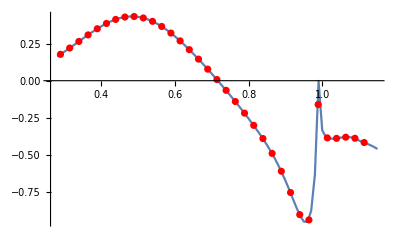

```mathematica
Show[{ListPlot[tRY00KTdat,Joined->True],ListPlot[tRY00KTR,PlotStyle->Red]}]
```

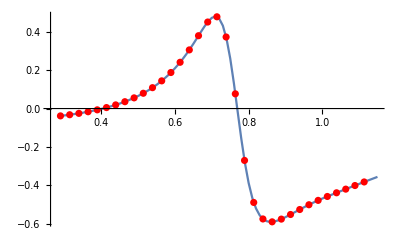

```mathematica
Show[{ListPlot[tRY11KTdat,Joined->True],ListPlot[tRY11KTR,PlotStyle->Red]}]
```

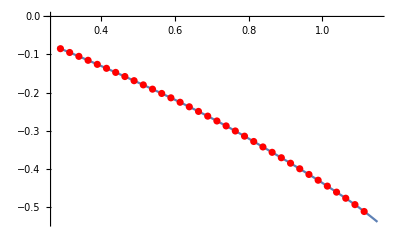

```mathematica
Show[{ListPlot[tRY20KTdat,Joined->True],ListPlot[tRY20KTR,PlotStyle->Red]}]
```

### Driving-term contribution

#### Formulas

```mathematica
tRY00DT[s_,par_]:=NIntegrate[(KRY0002S[s,sp]imt02[sp]+KRY0013S[s,sp]imt13[sp]+KRY0022S[s,sp]imt22[sp])/.par/.physval,{sp,4 M^2,s,1.42^2},Method-> PrincipalValue]
```

```mathematica
tRY11D0DT[s_,par_]:=NIntegrate[KRY1102S[s,sp]imt02[sp]/.par/.D2par/.physval,{sp,4 M^2+10^-6,1.42^2}]
```

```mathematica
tRY11FDT[s_,par_]:=NIntegrate[KRY1113S[s,sp]imt13[sp]/.par/.physval,{sp,4 M^2+10^-6,1.42^2}]
```

```mathematica
tRY11D2DT[s_,par_]:=NIntegrate[KRY1122S[s,sp]imt22[sp]/.par/.physval,{sp,4 M^2+10^-6,1.42^2}]
```

```mathematica
tRY11DT[s_,par_]:=tRY11D0DT[s,par]+tRY11FDT[s,par]+tRY11D2DT[s,par]
```

```mathematica
tRY20DT[s_,par_]:=NIntegrate[(KRY2002S[s,sp]imt02[sp]+KRY2013S[s,sp]imt13[sp]+KRY2022S[s,sp]imt22[sp])/.par/.physval,{sp,4 M^2,s,1.42^2},Method-> PrincipalValue]
```

#### Numerical values

```mathematica
tRY00DTdat=Monitor[Table[{W,Re[tRY00DT[W^2,par]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY11DTdat=Monitor[Table[{W,tRY11DT[W^2,par]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY20DTdat=Monitor[Table[{W,tRY20DT[W^2,par]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY00DTR=Table[{S0Roydes[[i,1]]/1000,S0RYdes[[i,4]]},{i,1,Length[S0RYdes]}];
```

```mathematica
tRY11DTR=Table[{PRYdes[[i,1]]/1000,PRYdes[[i,4]]},{i,1,Length[PRYdes]}];
```

```mathematica
tRY20DTR=Table[{S2RYdes[[i,1]]/1000,S2RYdes[[i,4]]},{i,1,Length[S2RYdes]}];
```

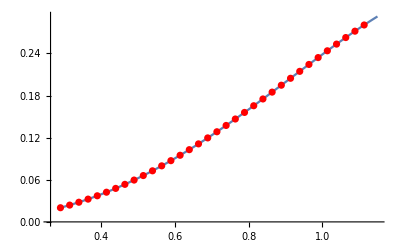

```mathematica
Show[{ListPlot[tRY00DTdat,Joined->True],ListPlot[tRY00DTR,PlotStyle->Red]}]
```

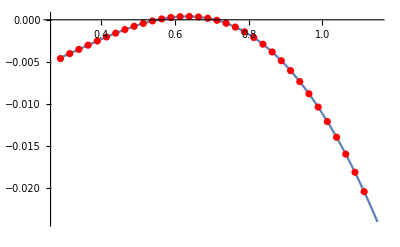

```mathematica
Show[{ListPlot[tRY11DTdat,Joined->True],ListPlot[tRY11DTR,PlotStyle->Red]}]
```

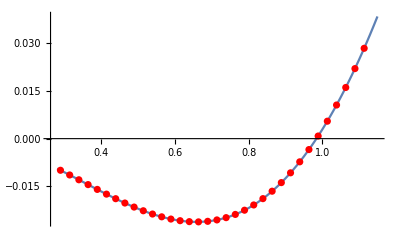

```mathematica
Show[{ListPlot[tRY20DTdat,Joined->True],ListPlot[tRY20DTR,PlotStyle->Red]}]
```

### Regge contribution

#### Formulas

The Regge contribution to the amplitude is

T_R(s,t)=∫_s_A^∞ g4(s,t,sp)ImT(sp,0)ⅆsp+∫_s_A^∞ g5(s,t,sp)ImT(sp,t)ⅆsp

but now we have to project in partial wave

(t^R)_J(s)=1/(64π)∫_-1^1 (∫_s_A^∞ g4(s,t,sp)ImT(sp,0)ⅆsp+∫_s_A^∞ g5(s,t,sp)ImT(sp,t)ⅆsp)P_J(z)dz

Is there an analytic calculation?

First we compute the different imaginary part contributions

```mathematica
ImF0R[s_,t_]=4 π^2 Cst[[1]].{ImF0t[s,t],ImF1t[s,t],ImF2t[s,t]}//FullSimplify;
```

```mathematica
ImF1R[s_,t_]=4 π^2 Cst[[2]].{ImF0t[s,t],ImF1t[s,t],ImF2t[s,t]}//FullSimplify;
```

```mathematica
ImF2R[s_,t_]=4 π^2 Cst[[3]].{ImF0t[s,t],ImF1t[s,t],ImF2t[s,t]}//FullSimplify;
```

Second we construct the isospin amplitudes

First contribution

```mathematica
TRY0RI[s_,t_,sp_]={1,0,0}.g4[s,t,sp].{ImF0R[sp,0],ImF1R[sp,0],ImF2R[sp,0]}//FullSimplify;
```

```mathematica
TRY1RI[s_,t_,sp_]={0,1,0}.g4[s,t,sp].{ImF0R[sp,0],ImF1R[sp,0],ImF2R[sp,0]}//FullSimplify;
```

```mathematica
TRY2RI[s_,t_,sp_]={0,0,1}.g4[s,t,sp].{ImF0R[sp,0],ImF1R[sp,0],ImF2R[sp,0]}//FullSimplify;
```

Now we try the analytic integration of the angle dependence

tRY00RIint[s_,sp_]=FullSimplify[Assuming[sp>sth>0&&s∈Complexes&&(s-2 sp+sth)/(2 s-2 sth)∉ℝ&&(s+2 sp-sth)/(2 s-2 sth)∉ℝ,1/(32π)Integrate[TRY0RI[s,tt[s,z],sp],{z,0,1}]],sp>s>sth>0]

((-((s-sth) (-2 sp+sth))+2 sp (sp-sth) Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]) (sp β_P+sp^(α_(P^p0)) β_(P^p)))/(8 sp (sp-sth) (-s+sth))

```mathematica
tRY00RIint[s_,sp_]=((-((s-sth) (-2 sp+sth))+2 sp (sp-sth) Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]) (sp Subscript[β, P]+sp^Subscript[α, P^p0] Subscript[β, P^p]))/(8 sp (sp-sth) (-s+sth));
```

tRY11RIint[s_,sp_]=FullSimplify[Assuming[sp>sth>0&&s∈Complexes&&(s-2 sp+sth)/(2 s-2 sth)∉ℝ&&(s+2 sp-sth)/(2 s-2 sth)∉ℝ,1/(32π)Integrate[ z TRY1RI[s,tt[s,z],sp],{z,0,1}]],sp>s>sth>0]

-1/(16 (s-sth)^2 (sp-sth))sp^(-1+α_ρ0) (s^2 sth+sth (-8 sp^2+8 sp sth+sth^2)+s (-2 sth^2+8 sp^2 (1+Log[2])-8 sp sth (1+Log[2]))+4 sp ((2 sp^2-3 sp sth+sth^2) (Log[sp (-s+2 sp-sth)]-Log[(sp-sth) (s+2 sp-sth)])+s (sp-sth) Log[(sp (sp-sth))/(-s^2+4 sp^2-4 sp sth+sth^2)])) β_ρ

```mathematica
tRY11RIint[s_,sp_]=1/(16 (s-sth)^2 (sp-sth))sp^(-1+Subscript[α, ρ0]) (s^2 sth+sth (-8 sp^2+8 sp sth+sth^2)+s (-2 sth^2+8 sp^2 (1+Log[2])-8 sp sth (1+Log[2]))+4 sp ((2 sp^2-3 sp sth+sth^2) (Log[sp (-s+2 sp-sth)]-Log[(sp-sth) (s+2 sp-sth)])+s (sp-sth) Log[(sp (sp-sth))/(-s^2+4 sp^2-4 sp sth+sth^2)])) Subscript[β, ρ];
```

tRY20RIint[s_,sp_]=FullSimplify[Assuming[sp>sth>0&&s∈Complexes&&(s-2 sp+sth)/(2 s-2 sth)∉ℝ&&(s+2 sp-sth)/(2 s-2 sth)∉ℝ,1/(32π)Integrate[TRY2RI[s,tt[s,z],sp],{z,0,1}]],sp>s>sth>0]

(sp^(-2+2 α_ρ0) (-((s-sth) (-2 sp+sth))+2 sp (sp-sth) Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]) β_2)/(8 (sp-sth) (-s+sth))

```mathematica
tRY20RIint[s_,sp_]=(sp^(-2+2 Subscript[α, ρ0]) (-((s-sth) (-2 sp+sth))+2 sp (sp-sth) Log[(sp (s-2 sp+sth))/((s+2 sp-sth) (-sp+sth))]) Subscript[β, 2])/(8 (sp-sth) (-s+sth));
```

Assuming[sp>sth>0&&sA>sth>0&&s∈Complexes&&(s-2 sp+sth)/(2 s-2 sth)∉ℝ&&(s+2 sp-sth)/(2 s-2 sth)∉ℝ,Integrate[tRY00RIint[s,sp],{sp,sA,∞}]]

```mathematica
tRY00RI[s_,par_]:=1/(32π)NIntegrate[ TRY0RI[s,tt[s,z],sp]/.par/.physval,{z,0,1},{sp,1.42^2,1000^2}]
```

```mathematica
tRY11RI[s_,par_]:=1/(32π)NIntegrate[z TRY1RI[s,tt[s,z],sp]/.par/.physval,{z,0,1},{sp,1.421^2,1000^2}]
```

```mathematica
tRY20RI[s_,par_]:=NIntegrate[tRY20RIint[s,sp]/.par/.physval,{sp,1.42^2,1000^2}]
```

Second contribution

```mathematica
TRY0RII[s_,t_,sp_]={1,0,0}.g5[s,t,sp].{ImF0R[sp,t],ImF1R[sp,t],ImF2R[sp,t]}//FullSimplify;
```

```mathematica
TRY1RII[s_,t_,sp_]={0,1,0}.g5[s,t,sp].{ImF0R[sp,t],ImF1R[sp,t],ImF2R[sp,t]}//FullSimplify;
```

```mathematica
TRY2RII[s_,t_,sp_]={0,0,1}.g5[s,t,sp].{ImF0R[sp,t],ImF1R[sp,t],ImF2R[sp,t]}//FullSimplify;
```

```mathematica
tRY00RII[s_,par_]:=NIntegrate[1/(32π)TRY0RII[s,tt[s,z],sp]/.par/.physval,{z,0,1},{sp,1.42^2,1000^2}]
```

```mathematica
tRY11RII[s_,par_]:=NIntegrate[1/(32π)z TRY1RII[s,tt[s,z],sp]/.par/.physval,{z,0,1},{sp,1.42^2,1000^2}]
```

```mathematica
tRY20RII[s_,par_]:=NIntegrate[1/(32π)TRY2RII[s,tt[s,z],sp]/.par/.physval,{z,0,1},{sp,1.42^2,1000^2}]
```

Total contribution

```mathematica
tRY00RT[s_,par_]:=tRY00RI[s,par]+tRY00RII[s,par]
```

```mathematica
tRY11RT[s_,par_]:=tRY11RI[s,par]+tRY11RII[s,par]
```

```mathematica
tRY20RT[s_,par_]:=tRY20RI[s,par]+tRY20RII[s,par]
```

#### Numerical values

```mathematica
tRY00RTdat=Monitor[Table[{W,Re[tRY00RT[W^2,reggepar]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY11RTdat=Monitor[Table[{W,Re[tRY11RT[W^2,reggepar]]},{W,2M+ 10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY20RTdat=Monitor[Table[{W,Re[tRY20RT[W^2,reggepar]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY00RTR=Table[{S0RYdes[[i,1]]/1000,S0RYdes[[i,5]]},{i,1,Length[S0Roydes]}];
```

```mathematica
tRY11RTR=Table[{PRYdes[[i,1]]/1000,PRYdes[[i,5]]},{i,1,Length[PRoydes]}];
```

```mathematica
tRY20RTR=Table[{S2RYdes[[i,1]]/1000,S2RYdes[[i,5]]},{i,1,Length[S2Roydes]}];
```

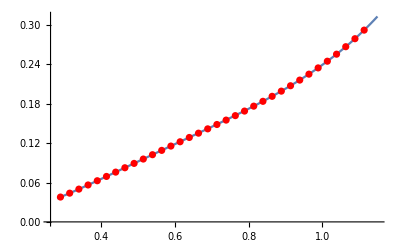

```mathematica
Show[{ListPlot[tRY00RTdat,Joined->True],ListPlot[tRY00RTR,PlotStyle->Red]}]
```

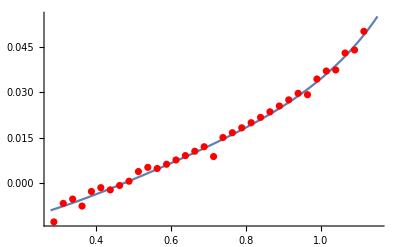

```mathematica
Show[{ListPlot[tRY11RTdat,Joined->True],ListPlot[tRY11RTR,PlotStyle->Red]},PlotRange-> All]
```

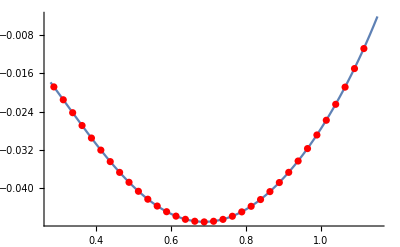

```mathematica
Show[{ListPlot[tRY20RTdat,Joined->True],ListPlot[tRY20RTR,PlotStyle->Red]},PlotRange-> All]
```

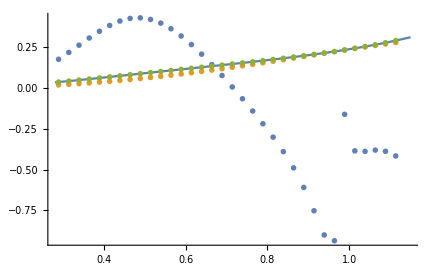

```mathematica
Show[{ListPlot[tRY00RTdat,Joined->True],ListPlot[{tRY00KTR,tRY00DTR,tRY00RTR}]},PlotRange-> All]
```

#### Checking the differences : Regge decomposition comparison

Analytic comparison

Second term

```mathematica
{1,0,0}.g5[s,t,sp].{imf0,imf1,imf2}//FullSimplify//Apart
```

-(imf0 s)/(π (s-sp) sp)+(-imf0+3 imf1-5 imf2)/(3 π (sp-sth+t))+(imf0-3 imf1+5 imf2)/(3 π (s+sp-sth+t))

```mathematica
(32π 4)/sth(imR0t/(sp*(sp-s))-(imR0t-3imR1t+5imR2t)/(3*(sp-4+t)*(sp+s-4+t)))*s/(32*pi^2)/.t->(4t)/sth/.toRK1/.toRK2//FullSimplify//Apart
```

-(imR0t s)/(π (s-sp) sp)+(-imR0t+3 imR1t-5 imR2t)/(3 π (sp-sth+t))+(imR0t-3 imR1t+5 imR2t)/(3 π (s+sp-sth+t))

```mathematica
{0,0,1}.g5[s,t,sp].{imf0,imf1,imf2}//FullSimplify//Apart
```

-(imf2 s)/(π (s-sp) sp)+(-2 imf0-3 imf1-imf2)/(6 π (sp-sth+t))+(2 imf0+3 imf1+imf2)/(6 π (s+sp-sth+t))

```mathematica
ryk20h1=32π 4/sth(imR2t/(sp*(sp-s))--(imR0t/3+imR1t/2+imR2t/6)/-((sp-4+t)*(sp+s-4+t)))*s/(32*pi^2)/.t->(4t)/sth/.toRK1/.toRK2//FullSimplify//Apart
```

-(imR2t s)/(π (s-sp) sp)+(-2 imR0t-3 imR1t-imR2t)/(6 π (sp-sth+t))+(2 imR0t+3 imR1t+imR2t)/(6 π (s+sp-sth+t))

Decomposition: numerical check

```mathematica
tRY00RT1dat=Monitor[Table[{W,Re[tRY00RI[W^2,reggepar]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY00RT2dat=Monitor[Table[{W,Re[tRY00RII[W^2,reggepar]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY11RT1dat=Monitor[Table[{W,Re[tRY11RI[W^2,reggepar]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY11RT2dat=Monitor[Table[{W,Re[tRY11RII[W^2,reggepar]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY20RT1dat=Monitor[Table[{W,Re[tRY20RI[W^2,reggepar]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY20RT2dat=Monitor[Table[{W,Re[tRY20RII[W^2,reggepar]]},{W,2M+10^-3,√(68 M^2),0.01}],W];
```

```mathematica
tRY00RT1R=Table[{RYreggedes[[i,1]]/1000,RYreggedes[[i,3]]},{i,1,Length[RYreggedes]}];
tRY00RT2R=Table[{RYreggedes[[i,1]]/1000,RYreggedes[[i,2]]},{i,1,Length[RYreggedes]}];
tRY11RT1R=Table[{RYreggedes[[i,1]]/1000,RYreggedes[[i,5]]},{i,1,Length[RYreggedes]}];
tRY11RT2R=Table[{RYreggedes[[i,1]]/1000,RYreggedes[[i,4]]},{i,1,Length[RYreggedes]}];
tRY20RT1R=Table[{RYreggedes[[i,1]]/1000,RYreggedes[[i,7]]},{i,1,Length[RYreggedes]}];
tRY20RT2R=Table[{RYreggedes[[i,1]]/1000,RYreggedes[[i,6]]},{i,1,Length[RYreggedes]}];
```

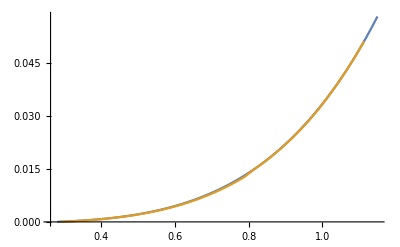

```mathematica
ListPlot[{tRY00RT1dat,tRY00RT1R},Joined->True]
```

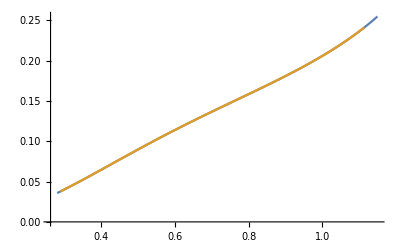

```mathematica
ListPlot[{tRY00RT2dat,tRY00RT2R},Joined->True]
```

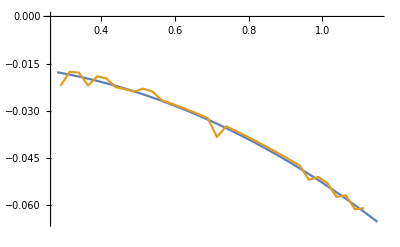

```mathematica
ListPlot[{tRY11RT1dat,tRY11RT1R},Joined->True,PlotRange->All]
```

```mathematica
ListPlot[{tRY00RT2dat,tRY00RT2R},Joined->True,PlotRange->All]
```

-Graphics-

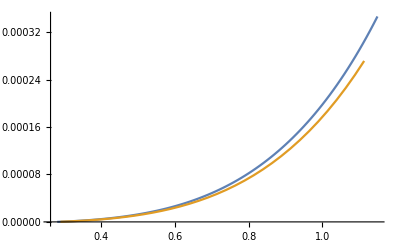

```mathematica
ListPlot[{tRY20RT1dat,tRY20RT1R},Joined->True]
```

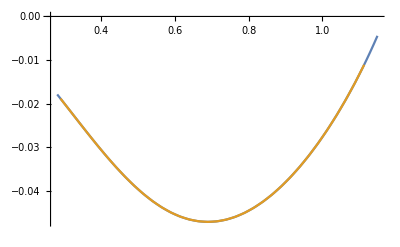

```mathematica
ListPlot[{tRY20RT2dat,tRY20RT2R},Joined->True]
```

### Total contribution

```mathematica
t00RY[s_,parpwa_,parregge_]:=tRY00ST[s,parpwa]+tRY00KT[s,parpwa]+tRY00DT[s,parpwa]+tRY00RT[s,parregge]
```

```mathematica
t11RY[s_,parpwa_,parregge_]:=tRY11ST[s,parpwa]+tRY11KT[s,parpwa]+tRY11DT[s,parpwa]+tRY11RT[s,parregge]
```

```mathematica
t20RY[s_,parpwa_,parregge_]:=tRY20ST[s,parpwa]+tRY20KT[s,parpwa]+tRY20DT[s,parpwa]+tRY20RT[s,parregge]
```

```mathematica
t00RYPWA[s_,parpwa_]:=tRY00ST[s,parpwa]+tRY00KT[s,parpwa]+tRY00DT[s,parpwa]
```

```mathematica
t11RYPWA[s_,parpwa_]:=tRY11ST[s,parpwa]+tRY11KT[s,parpwa]+tRY11DT[s,parpwa]
```

```mathematica
t20RYPWA[s_,parpwa_]:=tRY20ST[s,parpwa]+tRY20KT[s,parpwa]+tRY20DT[s,parpwa]
```

```mathematica
t00RYRK=Table[{S0RY[[i,1]]/1000,S0RY[[i,2]]},{i,1,Length[S0RY]}];
```

```mathematica
t00CFDRK=Table[{S0RY[[i,1]]/1000,Around[S0RY[[i,3]],{S0RY[[i,3]]-S0RY[[i,5]],S0RY[[i,4]]-S0RY[[i,3]]}]},{i,1,Length[S0RY]}];
```

```mathematica
t11RYRK=Table[{PRY[[i,1]]/1000,PRY[[i,2]]},{i,1,Length[PRY]}];
```

```mathematica
t11CFDRK=Table[{PRY[[i,1]]/1000,Around[PRY[[i,3]],{PRY[[i,3]]-PRY[[i,5]],PRY[[i,4]]-PRY[[i,3]]}]},{i,1,Length[PRY]}];
```

```mathematica
t20RYRK=Table[{S2RY[[i,1]]/1000,S2RY[[i,2]]},{i,1,Length[S2RY]}];
```

```mathematica
t20CFDRK=Table[{S2RY[[i,1]]/1000,Around[S2RY[[i,3]],{S2RY[[i,3]]-S2RY[[i,5]],S2RY[[i,4]]-S2RY[[i,3]]}]},{i,1,Length[S2RY]}];
```

```mathematica
t00RYdat=Table[{tRY00KTdat[[i,1]],tRY00ST[1,par]+tRY00KTdat[[i,2]]+tRY00DTdat[[i,2]]+tRY00RTdat[[i,2]]},{i,1,Length[tRY00KTdat]}];
```

```mathematica
t11RYdat=Table[{tRY11KTdat[[i,1]],tRY11ST[1,par]+tRY11KTdat[[i,2]]+tRY11DTdat[[i,2]]+tRY11RTdat[[i,2]]},{i,1,Length[tRY11KTdat]}];
```

```mathematica
t20RYdat=Table[{tRY20KTdat[[i,1]],tRY20ST[1,par]+tRY20KTdat[[i,2]]+tRY20DTdat[[i,2]]+tRY20RTdat[[i,2]]},{i,1,Length[tRY20KTdat]}];
```

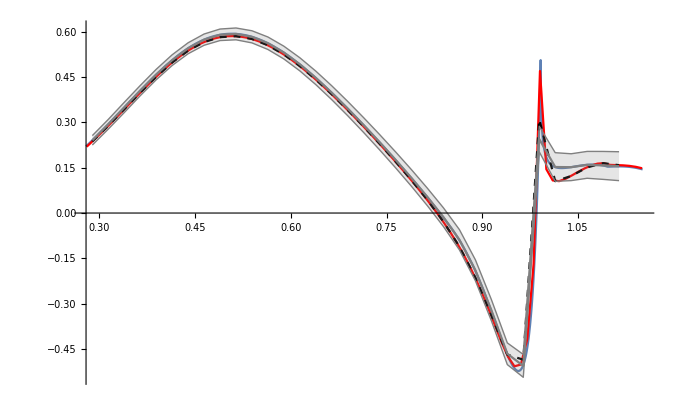

```mathematica
Show[Plot[Re[t00[W^2]/.S0par/.physval],{W,2M,√68 M}],ListPlot[t00RYdat,PlotStyle->Red,Joined->True],ListPlot[t00RYRK,Joined->True,PlotStyle->{Dashed,Black}],ListLinePlot[t00CFDRK,IntervalMarkers->"Bands",PlotStyle->Gray],PlotRange->{0.65,-0.7}]
```

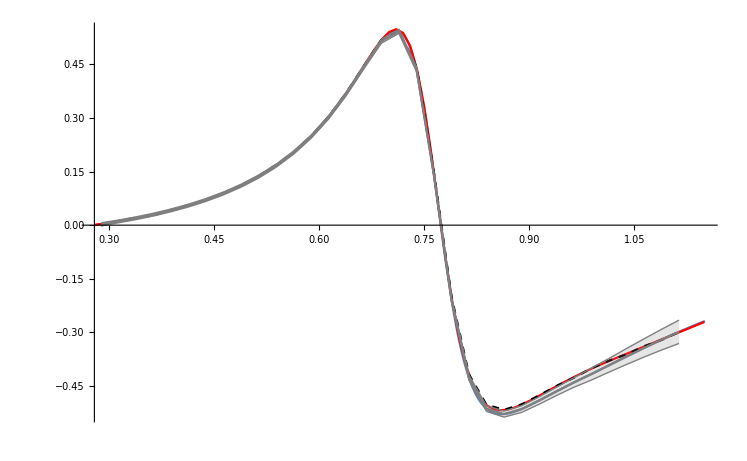

```mathematica
Show[Plot[Re[t11[W^2]/.Ppar/.physval],{W,2M,√68 M}],ListPlot[t11RYdat,PlotStyle->Red,Joined->True],ListPlot[t11RYRK,Joined->True,PlotStyle->{Dashed,Black}],ListLinePlot[t11CFDRK,IntervalMarkers->"Bands",PlotStyle->Gray]]
```

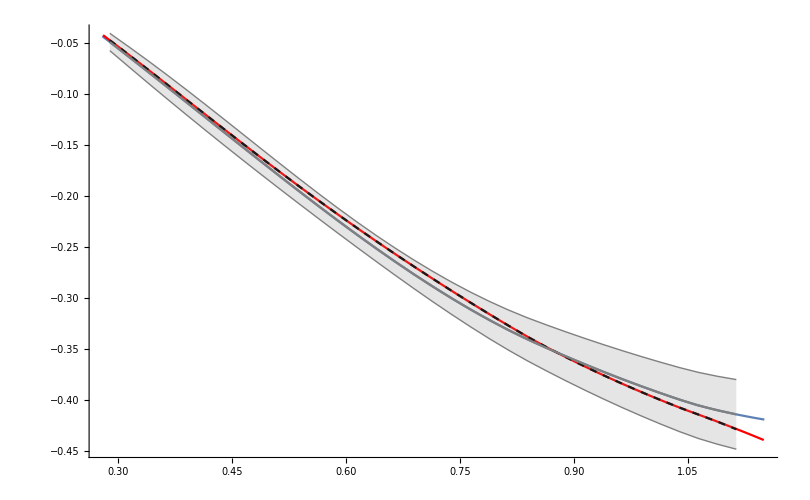

```mathematica
Show[Plot[Re[t20[W^2]/.S2par/.physval],{W,2M,√68 M}],ListPlot[t20RYdat,PlotStyle->Red,Joined->True],ListPlot[t20RYRK,Joined->True,PlotStyle->{Dashed,Black}],ListLinePlot[t20CFDRK,IntervalMarkers->"Bands",PlotStyle->Gray],PlotRange-> All]
```

### Error calculation

#### Computing RY for each parameter variation

```mathematica
nparRYPWA=0;
nparRYRegge=0;
For[k=1,k<=Length[par],k++,If[Δpar[[k,2]]>0,nparRYPWA++]];
For[k=1,k<=Length[reggepar],k++,If[Δreggepar[[k,2]]>0,nparRYRegge++]];
```

```mathematica
nparRY=nparRYPWA+nparRYRegge;
```

```mathematica
{nparRYPWA,nparRYRegge,nparRY}
```

{37,12,49}

```mathematica
t00RYAll=Table[0,{i,1,2nparRY+1}];
t11RYAll=Table[0,{i,1,2nparRY+1}];
t20RYAll=Table[0,{i,1,2nparRY+1}];
```

```mathematica
t00RYAll[[1]]=Monitor[Table[{W,Re[t00RY[W^2,par,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",W}];
t11RYAll[[1]]=Monitor[Table[{W,Re[t11RY[W^2,par,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"11",W}];
t20RYAll[[1]]=Monitor[Table[{W,Re[t20RY[W^2,par,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"20",W}];
```

```mathematica
t00RYPWA0=Monitor[Table[{W,Re[t00RYPWA[W^2,par]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",W}];
t11RYPWA0=Monitor[Table[{W,Re[t11RYPWA[W^2,par]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",W}];
t20RYPWA0=Monitor[Table[{W,Re[t20RYPWA[W^2,par]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",W}];
```

```mathematica
For[k=1;j=1,k<=Length[par],k++,par2=par;
If[Δpar[[k,2]]>0,j++;par2[[k,2]]=par[[k,2]]+Δpar[[k,2]];t00RYAll[[j]]=Monitor[Table[{W,Re[t00RY[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",k,j,W}];
t11RYAll[[j]]=Monitor[Table[{W,Re[t11RY[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"11",k,j,W}];t20RYAll[[j]]=Monitor[Table[{W,Re[t20RY[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"20",k,j,W}];]]
```

```mathematica
For[k=1;j=nparRYPWA+1,k<=Length[reggepar],k++,reggepar2=reggepar;
If[Δreggepar[[k,2]]>0,j++;reggepar2[[k,2]]=reggepar[[k,2]]+Δreggepar[[k,2]];
t00RYRegge=Monitor[Table[{W,Re[tRY00RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",k,j,W}];
t00RYAll[[j]]=Table[{t00RYPWA0[[i,1]],t00RYPWA0[[i,2]]+t00RYRegge[[i,2]]},{i,1,Length[t00RYPWA0]}];
t11RYRegge=Monitor[Table[{W,Re[tRY11RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"11",k,j,W}];
t11RYAll[[j]]=Table[{t11RYPWA0[[i,1]],t11RYPWA0[[i,2]]+t11RYRegge[[i,2]]},{i,1,Length[t11RYPWA0]}];
t20RYRegge=Monitor[Table[{W,Re[tRY20RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"20",k,j,W}];t20RYAll[[j]]=Table[{t20RYPWA0[[i,1]],t20RYPWA0[[i,2]]+t20RYRegge[[i,2]]},{i,1,Length[t20RYPWA0]}];]]
```

```mathematica
For[k=1;j=nparRY+1,k<=Length[par],k++,par2=par;
If[Δpar[[k,2]]>0,j++;par2[[k,2]]=par[[k,2]]-Δpar[[k,2]];t00RYAll[[j]]=Monitor[Table[{W,Re[t00RY[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",k,j,W}];
t11RYAll[[j]]=Monitor[Table[{W,Re[t11RY[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"11",k,j,W}];t20RYAll[[j]]=Monitor[Table[{W,Re[t20RY[W^2,par2,reggepar]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"20",k,j,W}];]]
```

```mathematica
For[k=1;j=nparRY+nparRYPWA+1,k<=Length[reggepar],k++,reggepar2=reggepar;
If[Δreggepar[[k,2]]>0,j++;reggepar2[[k,2]]=reggepar[[k,2]]-Δreggepar[[k,2]];
tRY00Regge=Monitor[Table[{W,Re[tRY00RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",k,j,W}];
t00RYAll[[j]]=Table[{t00RYPWA0[[i,1]],t00RYPWA0[[i,2]]+tRY00Regge[[i,2]]},{i,1,Length[t00RYPWA0]}];
tRY11Regge=Monitor[Table[{W,Re[tRY11RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"11",k,j,W}];
t11RYAll[[j]]=Table[{t11RYPWA0[[i,1]],t11RYPWA0[[i,2]]+tRY11Regge[[i,2]]},{i,1,Length[t11RYPWA0]}];
tRY20Regge=Monitor[Table[{W,Re[tRY20RT[W^2,reggepar2]]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"20",k,j,W}];t20RYAll[[j]]=Table[{t20RYPWA0[[i,1]],t20RYPWA0[[i,2]]+tRY20Regge[[i,2]]},{i,1,Length[t20RYPWA0]}];]]
```

Export["t00RYAll.dat", t00RYAll, "xLS"];

Export["t11RYAll.dat", t11RYAll, "xLS"];

Export["t20RYAll.dat", t20RYAll, "xLS"];

#### Checking with Kaminski : looking for the error

```mathematica
par2=par;
```

```mathematica
par2[[3,2]]=par[[3,2]]+Δpar[[3,2]];
```

```mathematica
ListPlot[{t00RoyAll[[2]],Table[{S0Royerr[[i,1]]/1000,S0Royerr[[i,6]]},{i,1,Length[S0Royerr]}]}]
```

-Graphics-

```mathematica
Show[ListPlot[{t00RoyAll[[1]],t00RoyAll[[2]],t00RoyAll[[3]]},Joined->True],ListPlot[{Table[{S0Royerr[[i,1]]/1000,S0Royerr[[i,2]]},{i,1,Length[S0Royerr]}],Table[{S0Royerr[[i,1]]/1000,S0Royerr[[i,6]]},{i,1,Length[S0Royerr]}],Table[{S0Royerr[[i,1]]/1000,S0Royerr[[i,7]]},{i,1,Length[S0Royerr]}]}]]
```

-Graphics-

#### Computing CFD for each parameter variation

```mathematica
t00CFDAll=Table[0,{i,1,2nparRY+1}];
t11CFDAll=Table[0,{i,1,2nparRY+1}];
t20CFDAll=Table[0,{i,1,2nparRY+1}];
```

```mathematica
t00CFDAll[[1]]=Monitor[Table[{W,Re[t00[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",W}];
t11CFDAll[[1]]=Monitor[Table[{W,Re[t11[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"11",W}];
t20CFDAll[[1]]=Monitor[Table[{W,Re[t20[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"20",W}];
```

```mathematica
For[k=1;j=1,k<=Length[par],k++,par2=par;
If[Δpar[[k,2]]>0,j++;par2[[k,2]]=par[[k,2]]+Δpar[[k,2]];
t00CFDAll[[j]]=Monitor[Table[{W,Re[t00[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",k,j,W}];
t11CFDAll[[j]]=Monitor[Table[{W,Re[t11[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"11",k,j,W}];t20CFDAll[[j]]=Monitor[Table[{W,Re[t20[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"20",k,j,W}];]]
```

```mathematica
For[k=1;j=nparRYPWA+1,k<=Length[reggepar],k++,reggepar2=reggepar;
If[Δreggepar[[k,2]]>0,j++;reggepar2[[k,2]]=reggepar[[k,2]]+Δreggepar[[k,2]];
t00CFDAll[[j]]=Monitor[Table[{W,Re[t00[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",k,j,W}];
t11CFDAll[[j]]=Monitor[Table[{W,Re[t11[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"11",k,j,W}];t20CFDAll[[j]]=Monitor[Table[{W,Re[t20[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"20",k,j,W}];]]
```

```mathematica
For[k=1;j=nparRY+1,k<=Length[par],k++,par2=par;
If[Δpar[[k,2]]>0,j++;par2[[k,2]]=par[[k,2]]-Δpar[[k,2]];
t00CFDAll[[j]]=Monitor[Table[{W,Re[t00[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",k,j,W}];
t11CFDAll[[j]]=Monitor[Table[{W,Re[t11[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"11",k,j,W}];t20CFDAll[[j]]=Monitor[Table[{W,Re[t20[W^2]/.par2/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"20",k,j,W}];]]
```

```mathematica
For[k=1;j=nparRY+nparRYPWA+1,k<=Length[reggepar],k++,reggepar2=reggepar;
If[Δreggepar[[k,2]]>0,j++;reggepar2[[k,2]]=reggepar[[k,2]]-Δreggepar[[k,2]];
t00CFDAll[[j]]=Monitor[Table[{W,Re[t00[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"00",k,j,W}];
t11CFDAll[[j]]=Monitor[Table[{W,Re[t11[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"11",k,j,W}];t20CFDAll[[j]]=Monitor[Table[{W,Re[t20[W^2]/.par/.physval]},{W,2Mp+10^-3,√68 Mp, 0.025}],{"20",k,j,W}];]]
```

#### Importing Data

```mathematica
t00RYAll = Import["RoyAll/t00RYAll.dat", "xLS"];
```

```mathematica
t11RYAll = Import["RoyAll/t11RYAll.dat", "xLS"];
```

```mathematica
t20RYAll = Import["RoyAll/t20RYAll.dat", "xLS"];
```

#### Error bands RY

```mathematica
t00RYΔ=Table[√Sum[If[(t00RYAll[[k,i,2]]-t00RYAll[[1,i,2]])^2>(t00RYAll[[k+nparRY,i,2]]-t00RYAll[[1,i,2]])^2,(t00RYAll[[k,i,2]]-t00RYAll[[1,i,2]])^2,(t00RYAll[[k+nparRY,i,2]]-t00RYAll[[1,i,2]])^2],{k,2,nparRY+1}],{i,1,Length[t00RYAll[[1]]]}];
```

```mathematica
t11RYΔ=Table[√Sum[If[(t11RYAll[[k,i,2]]-t11RYAll[[1,i,2]])^2>(t11RYAll[[k+nparRY,i,2]]-t11RYAll[[1,i,2]])^2,(t11RYAll[[k,i,2]]-t11RYAll[[1,i,2]])^2,(t11RYAll[[k+nparRY,i,2]]-t11RYAll[[1,i,2]])^2],{k,2,nparRY+1}],{i,1,Length[t11RYAll[[1]]]}];
```

```mathematica
t20RYΔ=Table[√Sum[If[(t20RYAll[[k,i,2]]-t20RYAll[[1,i,2]])^2>(t20RYAll[[k+nparRY,i,2]]-t20RYAll[[1,i,2]])^2,(t20RYAll[[k,i,2]]-t20RYAll[[1,i,2]])^2,(t20RYAll[[k+nparRY,i,2]]-t20RYAll[[1,i,2]])^2],{k,2,nparRY+1}],{i,1,Length[t20RYAll[[1]]]}];
```

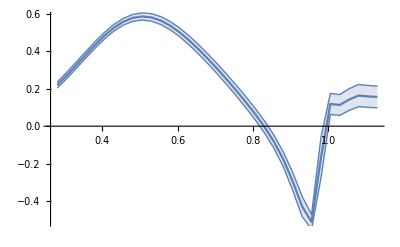

```mathematica
t00RYPlot=ListLinePlot[Table[{t00RYAll[[1,i,1]],t00RYAll[[1,i,2]]±t00RYΔ[[i]]},{i,1,Length[t00RYAll[[1]]]}],IntervalMarkers->"Bands"]
```

```mathematica
t00RYPlotRK=ListLinePlot[Table[{S0RYerr[[i,1]]/1000,S0RYerr[[i,2]]±S0RYerr[[i,3]]},{i,1,Length[S0RYerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

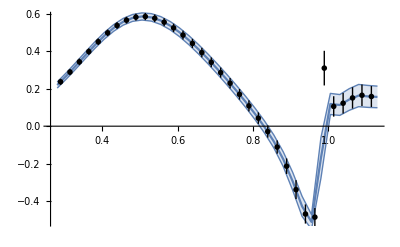

```mathematica
Show[t00RYPlot,t00RYPlotRK]
```

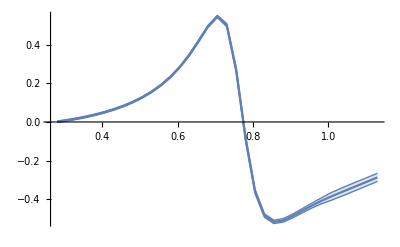

```mathematica
t11RYPlot=ListLinePlot[Table[{t11RYAll[[1,i,1]],t11RYAll[[1,i,2]]±t11RYΔ[[i]]},{i,1,Length[t11RYAll[[1]]]}],IntervalMarkers->"Bands"]
```

```mathematica
t11RYPlotRK=ListLinePlot[Table[{PRYerr[[i,1]]/1000,PRYerr[[i,2]]±PRYerr[[i,3]]},{i,1,Length[PRYerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

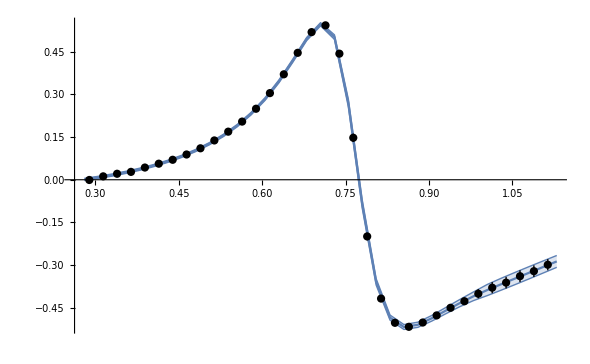

```mathematica
Show[t11RYPlot,t11RYPlotRK]
```

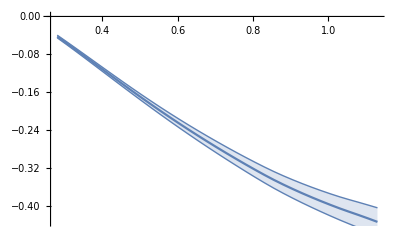

```mathematica
t20RYPlot=ListLinePlot[Table[{t20RYAll[[1,i,1]],t20RYAll[[1,i,2]]±t20RYΔ[[i]]},{i,1,Length[t20RYAll[[1]]]}],IntervalMarkers->"Bands"]
```

```mathematica
t20RYPlotRK=ListLinePlot[Table[{S2RYerr[[i,1]]/1000,S2RYerr[[i,2]]±S2RYerr[[i,3]]},{i,1,Length[S2RYerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

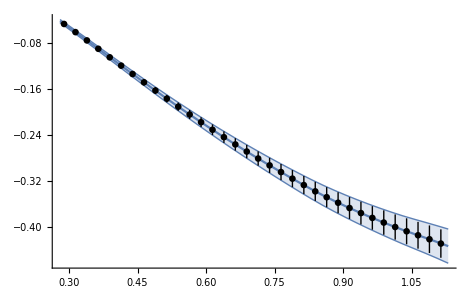

```mathematica
Show[t20RYPlot,t20RYPlotRK,PlotRange-> All]
```

#### Error bands CFD

```mathematica
Δerr[f_,r_,Δr_,n_]:=√(∑_(i=1)^n (D[f, r[[i,1]]])^2 Δr[[i,2]]^2);
```

```mathematica
ΔRet00[s_]:=Re[Δerr[t00[s],S0par,ΔS0par,Length[S0par]]/.par/.physval];
ΔRet11[s_]:=Re[Δerr[t11[s],Ppar,ΔPpar,Length[Ppar]]/.par/.physval];
ΔRet20[s_]:=Re[Δerr[t20[s],S2par,ΔS2par,Length[S2par]]/.par/.physval];
```

```mathematica
t00CFDΔ=Table[√Sum[If[(t00CFDAll[[k,i,2]]-t00CFDAll[[1,i,2]])^2>(t00CFDAll[[k+nparRY,i,2]]-t00CFDAll[[1,i,2]])^2,(t00CFDAll[[k,i,2]]-t00CFDAll[[1,i,2]])^2,(t00CFDAll[[k+nparRY,i,2]]-t00CFDAll[[1,i,2]])^2],{k,2,nparRY+1}],{i,1,Length[t00RYAll[[1]]]}];
```

```mathematica
t11CFDΔ=Table[√Sum[If[(t11CFDAll[[k,i,2]]-t11CFDAll[[1,i,2]])^2>(t11CFDAll[[k+nparRY,i,2]]-t11CFDAll[[1,i,2]])^2,(t11CFDAll[[k,i,2]]-t11CFDAll[[1,i,2]])^2,(t11CFDAll[[k+nparRY,i,2]]-t11CFDAll[[1,i,2]])^2],{k,2,nparRY+1}],{i,1,Length[t11RYAll[[1]]]}];
```

```mathematica
t20CFDΔ=Table[√Sum[If[(t20CFDAll[[k,i,2]]-t20CFDAll[[1,i,2]])^2>(t20CFDAll[[k+nparRY,i,2]]-t20CFDAll[[1,i,2]])^2,(t20CFDAll[[k,i,2]]-t20CFDAll[[1,i,2]])^2,(t20CFDAll[[k+nparRY,i,2]]-t20CFDAll[[1,i,2]])^2],{k,2,nparRY+1}],{i,1,Length[t20RYAll[[1]]]}];
```

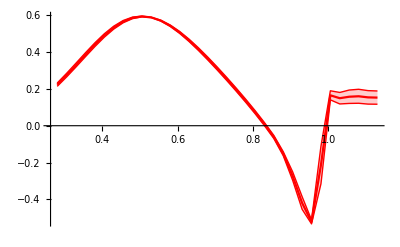

```mathematica
t00CFDPlot=ListLinePlot[Table[{t00CFDAll[[1,i,1]],t00CFDAll[[1,i,2]]±t00CFDΔ[[i]]},{i,1,Length[t00CFDAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Red]
```

```mathematica
t00CFDPlotRK=ListLinePlot[Table[{S0RYerr[[i,1]]/1000,S0RYerr[[i,4]]±S0RYerr[[i,5]]},{i,1,Length[S0RYerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

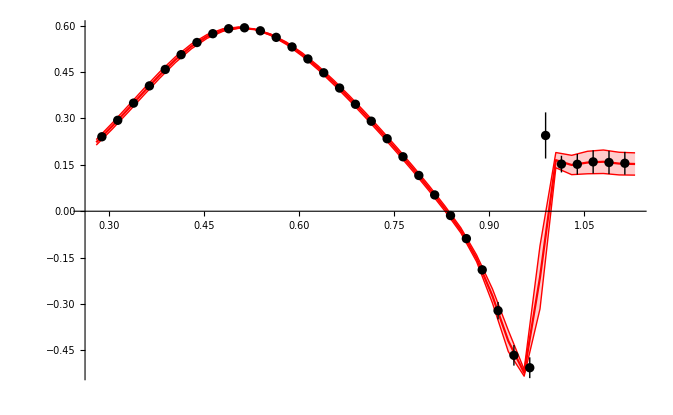

```mathematica
Show[t00CFDPlot,t00CFDPlotRK]
```

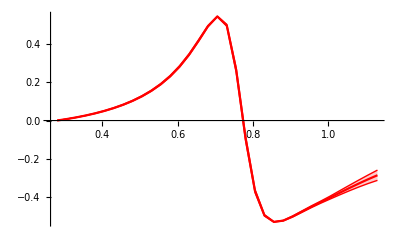

```mathematica
t11CFDPlot=ListLinePlot[Table[{t11CFDAll[[1,i,1]],t11CFDAll[[1,i,2]]±t11CFDΔ[[i]]},{i,1,Length[t11CFDAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Red]
```

```mathematica
t11CFDPlotRK=ListLinePlot[Table[{PRYerr[[i,1]]/1000,PRYerr[[i,4]]±PRYerr[[i,5]]},{i,1,Length[PRYerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

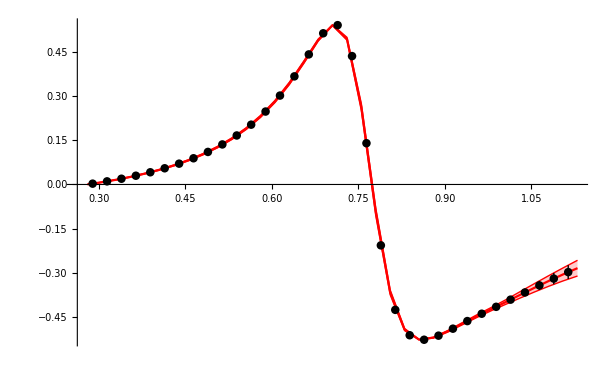

```mathematica
Show[t11CFDPlot,t11CFDPlotRK]
```

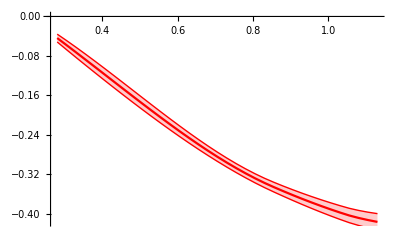

```mathematica
t20CFDPlot=ListLinePlot[Table[{t20CFDAll[[1,i,1]],t20CFDAll[[1,i,2]]±t20CFDΔ[[i]]},{i,1,Length[t20CFDAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Red]
```

```mathematica
t20CFDPlotRK=ListLinePlot[Table[{S2RYerr[[i,1]]/1000,S2RYerr[[i,4]]±S2RYerr[[i,5]]},{i,1,Length[S2RYerr]}],IntervalMarkers->"Bars",PlotStyle->{Black,PointSize[0.01]},Joined->False];
```

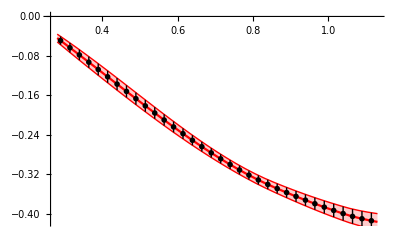

```mathematica
Show[t20CFDPlot,t20CFDPlotRK]
```

```mathematica
t00CFDPlot2=ListLinePlot[Table[{t00RYAll[[1,i,1]],Re[t00[t00RYAll[[1,i,1]]^2]/.par/.physval]±ΔRet00[t00RYAll[[1,i,1]]^2]},{i,1,Length[t00RYAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Green];t11CFDPlot2=ListLinePlot[Table[{t11RYAll[[1,i,1]],Re[t11[t11RYAll[[1,i,1]]^2]/.par/.physval]±ΔRet11[t11RYAll[[1,i,1]]^2]},{i,1,Length[t11RYAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Green];
t20CFDPlot2=ListLinePlot[Table[{t20RYAll[[1,i,1]],Re[t20[t20RYAll[[1,i,1]]^2]/.par/.physval]±ΔRet20[t20RYAll[[1,i,1]]^2]},{i,1,Length[t20RYAll[[1]]]}],IntervalMarkers->"Bands",PlotStyle->Green];
```

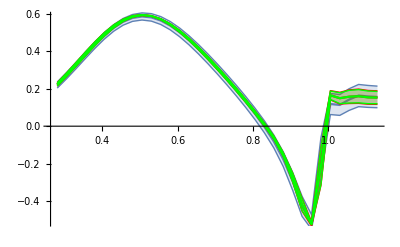

```mathematica
Show[t00RYPlot,t00CFDPlot,t00CFDPlot2]
```

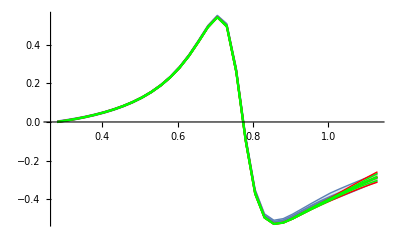

```mathematica
Show[t11RYPlot,t11CFDPlot,t11CFDPlot2]
```

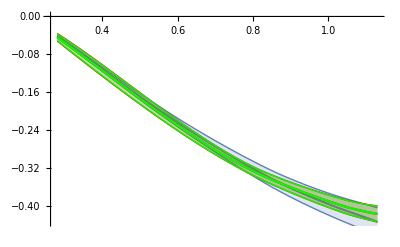

```mathematica
Show[t20RYPlot,t20CFDPlot,t20CFDPlot2]
```

#### Error for the difference

```mathematica
t00RYDiff=Table[Table[{t00RYAll[[k,i,1]],t00RYAll[[k,i,2]]-t00CFDAll[[k,i,2]]},{i,1,Length[t00RYAll[[k]]]}],{k,1,Length[t00RYAll]}];
t11RYDiff=Table[Table[{t11RYAll[[k,i,1]],t11RYAll[[k,i,2]]-t11CFDAll[[k,i,2]]},{i,1,Length[t11RYAll[[k]]]}],{k,1,Length[t11RYAll]}];
t20RYDiff=Table[Table[{t20RYAll[[k,i,1]],t20RYAll[[k,i,2]]-t20CFDAll[[k,i,2]]},{i,1,Length[t20RYAll[[k]]]}],{k,1,Length[t20RYAll]}];
```

```mathematica
t00RYDiffΔ=Table[√Sum[If[(t00RYDiff[[k,i,2]]-t00RYDiff[[1,i,2]])^2>(t00RYDiff[[k+nparRY,i,2]]-t00RYDiff[[1,i,2]])^2,(t00RYDiff[[k,i,2]]-t00RYDiff[[1,i,2]])^2,(t00RYDiff[[k+nparRY,i,2]]-t00RYDiff[[1,i,2]])^2],{k,2,nparRY+1}],{i,1,Length[t00RYDiff[[1]]]}];
```

```mathematica
t11RYDiffΔ=Table[√Sum[If[(t11RYDiff[[k,i,2]]-t11RYDiff[[1,i,2]])^2>(t11RYDiff[[k+nparRY,i,2]]-t11RYDiff[[1,i,2]])^2,(t11RYDiff[[k,i,2]]-t11RYDiff[[1,i,2]])^2,(t11RYDiff[[k+nparRY,i,2]]-t11RYDiff[[1,i,2]])^2],{k,2,nparRY+1}],{i,1,Length[t11RYDiff[[1]]]}];
```

```mathematica
t20RYDiffΔ=Table[√Sum[If[(t20RYDiff[[k,i,2]]-t20RYDiff[[1,i,2]])^2>(t20RYDiff[[k+nparRY,i,2]]-t20RYDiff[[1,i,2]])^2,(t20RYDiff[[k,i,2]]-t20RYDiff[[1,i,2]])^2,(t20RYDiff[[k+nparRY,i,2]]-t20RYDiff[[1,i,2]])^2],{k,2,nparRY+1}],{i,1,Length[t20RYDiff[[1]]]}];
```

```mathematica
t00RYDiffPlot=ListLinePlot[Table[{t00RYDiff[[1,i,1]],t00CFDAll[[1,i,2]]±t00RYDiffΔ[[i]]},{i,1,Length[t00RYAll[[1]]]}],IntervalMarkers->"Bands"];
```

```mathematica
t11RYDiffPlot=ListLinePlot[Table[{t11RYDiff[[1,i,1]],t11CFDAll[[1,i,2]]±t11RYDiffΔ[[i]]},{i,1,Length[t11RYAll[[1]]]}],IntervalMarkers->"Bands"];
```

```mathematica
t20RYDiffPlot=ListLinePlot[Table[{t20RYDiff[[1,i,1]],t20CFDAll[[1,i,2]]±t20RYDiffΔ[[i]]},{i,1,Length[t20RYAll[[1]]]}],IntervalMarkers->"Bands",PlotRange-> {0,-0.6}];
```

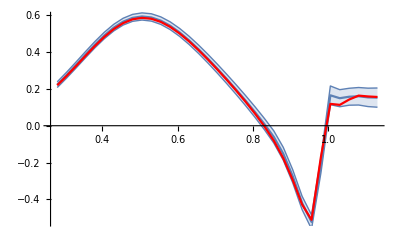

```mathematica
Show[t00RYDiffPlot,ListLinePlot[Table[{t00RYAll[[1,i,1]],t00RYAll[[1,i,2]]},{i,1,Length[t00RYAll[[1]]]}],PlotStyle->Red]]
```

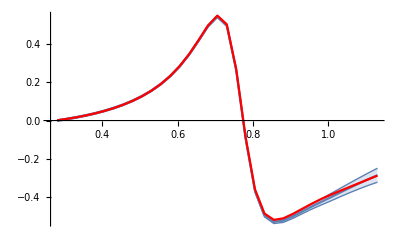

```mathematica
Show[t11RYDiffPlot,ListLinePlot[Table[{t11RYAll[[1,i,1]],t11RYAll[[1,i,2]]},{i,1,Length[t11RYAll[[1]]]}],PlotStyle->Red]]
```

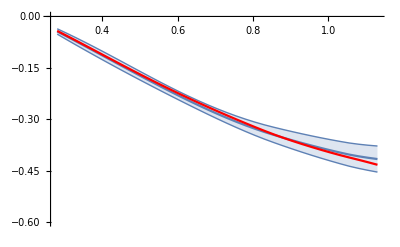

```mathematica
Show[t20RYDiffPlot,ListLinePlot[Table[{t20RYAll[[1,i,1]],t20RYAll[[1,i,2]]},{i,1,Length[t20RYAll[[1]]]}],PlotStyle->Red]]
```